# Welcome to ML/CFT

## Version 1.0.0-alpha

# Initialization

## Global Variables

### Directories

```mathematica
SetDirectory[NotebookDirectory[]]
PathForPlots = "plots/"
PathForRuns = "runs/"
PathForTests = "tests/"
```

/Users/jthaler/clagit/modular-bootstrap

plots/

runs/

tests/

## Defining/Modifying Data Types

## Defining CFT Data

### Components of CFT Data

```mathematica
(* Protect to avoid overwritting*) 
Protect[CFTData,DSD];

(* Essential information about a CFT, namely the central charge and list of Virasoro primaries *)
(* Also has information about maximum delta and variables (if present) *)
NameOf[CFTData[name_,c_,primaries_,cut_,variables_]]:= name
CentralChargeOf[CFTData[name_,c_,primaries_,cut_,variables_]]:= c
PrimariesOf[CFTData[name_,c_,primaries_,cut_,variables_]]:= primaries
MaxDeltaOf[CFTData[name_,c_,primaries_,cut_,variables_]]:= cut
VariablesOf[CFTData[name_,c_,primaries_,cut_,variables_]] := variables

(* Basic derived properties*)
NumberOfPrimariesOf[model_CFTData]:= Length[PrimariesOf[model]]
KeptPrimariesOf[model_CFTData]:= Select[PrimariesOf[model],(DeltaOf[#]<MaxDeltaOf[model])&]
NumberOfKeptPrimariesOf[model_CFTData]:= Length[KeptPrimariesOf[model]]
TotalDegeneracyOfKeptPrimariesOf[model_CFTData]:= Total[DegeneracyOf/@KeptPrimariesOf[model]];
NumberOfVariablesOf[model_CFTData]:= Length[VariablesOf[model]]
```

### Components of a Primary

```mathematica
(* A primary has a dimension, spin (which has to be an non-negative integer), and a degeneracy (which has to be a positive integer) *)
DeltaOf[DSD[Δ_, j_,degen_]]:= Δ
SpinOf[DSD[Δ_, j_,degen_]]:= j
DegeneracyOf[DSD[Δ_, j_,degen_]]:= degen

(* When it is helpful to convert information to a basic list *)
DeltaSpinDegenOf[primary_]:= {DeltaOf[primary],SpinOf[primary],DegeneracyOf[primary]}
```

### Deformed CFT Data

```mathematica
(* We will try to treat deformed CFTs on a similar footing to regular CFT data. *)
Protect[DeformedCFTData];

(* Starting from a base model, the deformation involves a modified central charge and a new cutoff scale *)
BaseModelOf[DeformedCFTData[basemodel_CFTData, newC_, cut_]]:= basemodel
CentralChargeOf[DeformedCFTData[basemodel_CFTData, newC_, cut_]]:=newC
MaxDeltaOf[DeformedCFTData[basemodel_CFTData, newC_, cut_]]:= cut;
```

## Modifying CFT Data

### Helper Function for Scanning Constrained Ranges

```mathematica
(* This is a sigmoid-like function that forces the output to be between min and max.  This is needed because we want to do unconstrained optimization of the CFT parameters. *)
(*SigmoidEsque[x_,min_, max_, α_]:= min + (max-min)*1/(2α)(Log[1+Exp[α (x+1)]]-Log[1+Exp[α (x-1)]])*)
SigmoidEsque[x_,min_, max_]:= min + (max-min)*1/(1+Exp[-x])

(* This is the stiffness of the sigmoid.  In a perfect world, I'll just be able to set this and forget it. *)
(* Not currently using this! *)
(*DefaultValueAlpha = 1;*)
```

### Truncating Models in Delta

```mathematica
(* Cut models off in Delta *)
(* Note that primaries right at the cut off are removed (< instead of <=) *)
TruncateInDeltaOf[CFTData[name_,c_,primaries_,cut_,variables_],maxdelta_]:=Module[{newname, newprimaries},
newname = Row[{name, "; Δ_trunc=", maxdelta}];
newprimaries = Select[primaries, (DeltaOf[#]< maxdelta)&];

(* return value *)
CFTData[newname, c, newprimaries,maxdelta,variables]
]

(* When I want to ensure no stray operators *)
HardTruncateOf[model_CFTData]:= TruncateInDeltaOf[model,MaxDeltaOf[model]];

(* For a deformed model, truncation just changes the max Delta *)
TruncateInDeltaOf[DeformedCFTData[basemodel_CFTData, newC_, cut_],maxdelta_]:= DeformedCFTData[basemodel,newC,maxdelta]
```

### Making Models More Flexible

```mathematica
(* Changing the model name *)
(* This is primarily used for plotting purposes *)
RenameOf[CFTData[name_,c_,primaries_,cut_,variables_], newname_]:= Module[{},
CFTData[newname,c,primaries,cut,variables]
]

(* Making the central charge into a floating parameter *)
(* The central charge is now the variable "FlexCC", restricted to be between the desired min and max *)
FloatCentralChargeOf[CFTData[name_,c_,primaries_,cut_,variables_],mincentralcharge_, maxcentralcharge_]:= Module[{newname},
newname = Row[{name, " with floating c in [",mincentralcharge,",", maxcentralcharge,"]"}];

(* return value *)
CFTData[newname,SigmoidEsque[FlexCC,mincentralcharge,maxcentralcharge], primaries, cut,Join[variables, {FlexCC}]]
]

(* Changing maximum delta.  Note that this does not actually remove any primaries *)
ChangeMaxDeltaOf[CFTData[name_,c_,primaries_,cut_,variables_], newcut_]:= CFTData[name,c,primaries,newcut,variables]

(* This takes a model and replaces the non-saturating primaries (Delta strictly greater than j) with ones where Delta can float, leaving spin and degeneracy unchanged. *)
(* Floating the saturating primaries is delicate, since the associated partition function term has a discontinuity between Delta = j and Delta > j, so we don't allow it in the code. *)
FloatFloatableDeltasOf[CFTData[name_,c_,primaries_,cut_,variables_],maxdelta_]:= Module[{newname, newprimaries, newvariables,addedvariables,iter},
newname = Row[{name, " with floating Δ's up to ",maxdelta}];

newprimaries = {};
addedvariables = {};

For[iter = 1, iter <= Length[primaries], iter++,

If[DeltaOf[primaries[[iter]]]== SpinOf[primaries[[iter]]],

(* Don't change the saturating primaries *)
AppendTo[newprimaries, primaries[[iter]]],

(* But do change the nonsaturating ones... *)
AppendTo[newprimaries, DSD[SigmoidEsque[FlexDelta[iter],SpinOf[primaries[[iter]]],2*maxdelta-SpinOf[primaries[[iter]]]], SpinOf[primaries[[iter]]], DegeneracyOf[primaries[[iter]]]]];
(* ...and store the associated variable*)
AppendTo[addedvariables, FlexDelta[iter]];
]
];
newvariables = Join[variables,addedvariables];

(* return value *)
CFTData[newname, c, newprimaries, maxdelta,newvariables]
]
```

### Fixing Variables of a Model

```mathematica
(* This is how you set the values of the variables in a model using data from the replacement *)
ApplyReplacementTo[model_CFTData, replacement_ReplacementData]:= Module[{rules,name,newc, newprimaries,newvariables,cut},
rules = ReplacementRulesOf[replacement];
name = NameOf[model];
newc = CentralChargeOf[model] /. rules;
newprimaries = PrimariesOf[model] /. rules;
cut = MaxDeltaOf[model];
newvariables =  DeleteElements[VariablesOf[model],VariablesOf[replacement]];

(* return value *)
CFTData[name,newc,newprimaries,cut,newvariables]
]

(* Setting central charge, natch *)
SetCentralChargeOf[CFTData[name_,c_,primaries_,cut_,variables_], newc_]:= Module[{newname},
(* return value *)
CFTData[newname, newc, primaries, cut,variables]
]
```

### Removing/Duplicating Primaries

```mathematica
(* Remove i-th primary, used to check stability of solution *)
RemovePrimaryFrom[model_CFTData, index_]:= Module[{name, c, primaries, cut,variables},
name = "removed";
c = CentralChargeOf[model];
primaries = Delete[PrimariesOf[model], index];
cut = MaxDeltaOf[model];
variables = VariablesOf[model];

(* return value *)
CFTData[name,c,primaries,cut,variables]
]

(* Duplicate i-th primary (effectively doubling its degeneracy), used to check stability of solution *)
DuplicatePrimaryFrom[model_CFTData, index_]:= Module[{name, c, primaries, cut,variables},
name = "duplicated";
c = CentralChargeOf[model];
primaries = Join[PrimariesOf[model], {PrimariesOf[model][[index]]}];
cut = MaxDeltaOf[model];
variables = VariablesOf[model];

(* return value *)
CFTData[name,c,primaries,cut,variables]
]
```

## Manipulating/Generating Taus

### Tau Variables to Protect Globally

```mathematica
(* Global variables related to tau that we don't ever want to set to any values *)
Protect[q,qbar];
Protect[tau1,tau2];
```

### Convert Different Tau Formats

```mathematica
(* Evaluates expressions in q in terms of tau (which is complex) *)
EvaluateAtTau[expression_][τ_]:= Module[{},
expression /. q-> Exp[2π ⅈ(tau1 + ⅈ tau2)]/. qbar-> Exp[-2π ⅈ(tau1 - ⅈ tau2)]/. tau1 -> Re[τ] /. tau2-> Im[τ]
]

(* Changes complex tau to Re/Im components *)
TauOneTwoOf[τ_]:= {Re[τ], Im[τ]}
```

### Impose Tau Restrictions

```mathematica
(* These ranges come from restricting to the fundamental domain, but with an additional cut on tau2 *)
(* Note < instead of <= for tau2max, so values right at the cut are not valid, but we do let tau = i be valid, since it is so commonly used *)
ValidTau[tau2max_][τ_]:= (Re[τ]^2 + Im[τ]^2 >= 1 && Im[τ] < tau2max)
```

### Generate Deterministic List of Tau Values (For Testing)

```mathematica
(* Determininistic tau values are used for testing *)
(* Note that we only look at tau1 > 0, since parity invariance implies that tau1 < 0 doesn't offer new information *)
Clear[DeterministicTauValues]
DeterministicTauValues[tau1width_,tau2width_,tau2max_]:= DeterministicTauValues[tau1width,tau2width,tau2max]=Module[{taus},
(* Flat measure in tau1, peaked toward smaller values of tau2 according to the Jacobian *)
taus = Flatten[Table[τ1+ⅈ(Sqrt[3]/2)/(1 - u2), {τ1,0+ tau1width/2, 1/2, tau1width}, {u2,(-√3+2 tau2max)/(2 tau2max)-tau2width/2, 0, -tau2width}],1];

(* Restrict to fundamental domain and impose max tau2 *)
taus = Select[ taus, ValidTau[tau2max]];

(* return value *)
taus
]
```

### Generate Stochastic List of Tau Values (For Training)

```mathematica
(* Define Tau Sampler Parameters *)
Protect[TauSamplerData];
NumTausOf[TauSamplerData[num_,tau2max_]]:= num
Tau2MaxOf[TauSamplerData[num_,tau2max_]]:= tau2max 

(* Stochastic tau values are used for training *)
Clear[StochasticTauValues]
StochasticTauValues[num_,tau2max_]:=Module[{list,try},
list = {};
Until[Length[list]==num,
try = RandomReal[{0,1/2}]+ⅈ(Sqrt[3]/2)/(1 - RandomReal[{0,1}]);
If[ ValidTau[tau2max][try],AppendTo[list,try]];
];
list
]

(* Calling for stochastic values through the sampler data*)
StochasticTauValues[data_TauSamplerData] := StochasticTauValues[NumTausOf[data],Tau2MaxOf[data] ]
```

## Defining/Modifying Replacements

### Components of a Replacement

```mathematica
(* Because the models have variables, you need to define replacements to set those variables to numerical values *)
Protect[ReplacementData];

(* A replacement has a list of variables (which hopefully match the model), replacement values, and possible uncertainties captured through inverse covariance matrix *)
(* The use of inverse covariance is because that is what can be extracted numerically with reasonably reliability. *)
VariablesOf[ReplacementData[variables_, values_, invcov_]]:= variables
ValuesOf[ReplacementData[variables_, values_,invcov_]]:= values
InverseCovarianceOf[ReplacementData[variables_, values_,invcov_]]:= invcov

(* When you want to use a replacement, you use the standard Mathematica replacement rules.  Not sure if this is the most computationally efficient strategy, but it seems to work. *)
ReplacementRulesOf[ReplacementData[variables_, values_,invcov_]]:= Inner[(#1 -> #2)&, variables, values, List]
```

### Null Replacement

```mathematica
(* If you really don't need to change any variables *)
NullReplacement = ReplacementData[{},{},{}];
```

### Manipulate Replacements

```mathematica
(* The shift is used to apply a gradient update step *)
ShiftReplacementBy[ReplacementData[variables_, values_, invcov_], shift_]:= ReplacementData[variables, values+shift,invcov]
```

### Create Random Replacement for a CFT

```mathematica
(* This is used for stochastic initialization *)
(* Note that all of the parameters are given the same random range, which might not be appropriate for all situations *)
(* Right now, this is not used in the production code. *)
Clear[RandomReplacementFor]
RandomReplacementFor[model_CFTData, randmin_, randmax_]:= Module[{variables, values,invcov},
variables = VariablesOf[model];
values = Table[RandomReal[{randmin,randmax}], {i, 1, Length[variables]}];
invcov = Null;

(* return value *)
ReplacementData[variables, values,invcov]
]
```

### Create Replacement based on Existing CFT

```mathematica
(* This is a dangerous function that doesn't always work the way you think it should, since it assumes that a solution can be found. Use with caution! *)
(* Despite this caution, this is needed when taking a model, making it flexible, and then setting the parameters to the original values. There is probably a more robust way to accomplish this. *)
FixedReplacementFor[flexible_CFTData,fixed_CFTData]:=Module[{name,fixedsolution},
fixedsolution = NSolve[{CentralChargeOf[flexible]==CentralChargeOf[fixed], ( DeltaOf/@ PrimariesOf[flexible])==(DeltaOf/@PrimariesOf[fixed])},VariablesOf[flexible], Reals][[1]];

(* return value *)
 ReplacementData[VariablesOf[flexible], (VariablesOf[flexible]/.fixedsolution ),Null]
]

(* Same as function above, but it doesn't try to solve for the central charge. *)
FixedReplacementNoCCFor[flexible_CFTData,fixed_CFTData]:=Module[{name,fixedsolution},
fixedsolution = NSolve[{( DeltaOf/@ PrimariesOf[flexible])==(DeltaOf/@PrimariesOf[fixed])},VariablesOf[flexible], Reals][[1]];

(* return value *)
 ReplacementData[ VariablesOf[flexible], (VariablesOf[flexible]/.fixedsolution ),Null]
]
```

## Define Optimization Format

### Defining Optimization Data

```mathematica
(* The optimizer output is just a name, a model, and optimization iterations*)
Protect[OptimizerData]
NameOf[OptimizerData[name_,model_CFTData, iterations_]]:= name;
ModelOf[OptimizerData[name_,model_CFTData, iterations_]]:= model;
IterationsOf[OptimizerData[name_, model_CFTData, iterations_]]:= iterations;

(* Derived quantities*)
NumIterationsOf[OptimizerData[name_, model_CFTData, iterations_]]:= Length[iterations];
```

{}

### Defining Iteration Data

```mathematica
(* Each optimizer generates the same type of result: iteration number, loss, and replacement.  I can also store optional auxiliary information, though that might be different per optimizer *)
Protect[IterationData]
IterationNumOf[IterationData[iter_, testloss_, trainloss_,replacement_ReplacementData, aux___]]:= iter;
TestLossOf[IterationData[iter_, testloss_, trainloss_,replacement_ReplacementData, aux___]]:= testloss;
TrainLossOf[IterationData[iter_, testloss_, trainloss_,replacement_ReplacementData, aux___]]:= trainloss;
ReplacementOf[IterationData[iter_, testloss_, trainloss_,replacement_ReplacementData, aux___]]:= replacement;
AuxiliaryInfoOf[IterationData[iter_, testloss_, trainloss_,replacement_ReplacementData, aux___]]:= aux;

(* Getting the final replacement values *)
LastReplacementOf[OptimizerData[name_, model_CFTData, iterations_]]:= ReplacementOf[Last[iterations]]

(* Getting the final loss value *)
LastTestLossOf[OptimizerData[name_, model_CFTData, iterations_]]:= TestLossOf[Last[iterations]]
```

{}

### Convert to Lists of Information

```mathematica
(* Get list of test loss values *)
TestLossVsIterationListOf[OptimizerData[name_, model_CFTData, iterations_]]:= Module[{},
 {IterationNumOf[#],TestLossOf[#]}&/@ iterations
]

(* Get list of test loss values *)
TrainLossVsIterationListOf[OptimizerData[name_, model_CFTData, iterations_]]:= Module[{},
 {IterationNumOf[#],TrainLossOf[#]}&/@ iterations
]

(* Get list of number of singular values; only makes sense for singular value descent *)
SingularValuesVsIterationListOf[OptimizerData[name_, model_CFTData, iterations_]]:= Module[{},
 {IterationNumOf[#],AuxiliaryInfoOf[#][[2]]}&/@ iterations
]

(* Get list of learning rate; only make sense for singular value descent, and likely to be removed *)
LearningRateVsIterationListOf[OptimizerData[name_, model_CFTData, iterations_]]:= Module[{},
 {IterationNumOf[#],AuxiliaryInfoOf[#][[1]]}&/@ iterations
]

(* Get list of central charges, which requires knowing what the model is *)
CentralChargeVsIterationListOf[OptimizerData[name_, model_CFTData, iterations_]]:= Module[{},
{IterationNumOf[#], CentralChargeOf[ApplyReplacementTo[model, ReplacementOf[#]]]}&/@iterations
]
```

### Modifying Optimizer Data

```mathematica
(* Change name of *)
RenameOf[OptimizerData[name_,model_CFTData, iterations_], newname_]:= OptimizerData[newname, model, iterations]

(* Add iteration to*)
AddIterationOf[OptimizerData[name_,model_CFTData, iterations_], newiteration_IterationData]:= OptimizerData[name,model,Append[iterations,newiteration]]
```

## Setting Up Known CFTs

## Nathan’s code: N=1 minimal models (N1MM)

### Define N1MM Models

```mathematica
(* This is Nathan's code to define the N=1 minimal models, slightly rewriten *)

(* Defining Central Charge *)
N1MM CentralCharge[m_]:= 3/2(1-8/(m(m+2)));

(* These are Nathan's helper functions, just adding N1MM prefix to avoid name overlap *)
(* Note that I've commented out functions that don't seem to be used. *)
N1MM pqAllowedRamond[m_]:=Select[Tuples[{Range[m-1],Range[m+1]}],OddQ[Total@#]&];
N1MM pqAllowedNS[m_]:=Select[Tuples[{Range[m-1],Range[m+1]}],EvenQ[Total@#]&]; 
(*N1MM h[p_,q_,m_,ϵ_]:=(((m+2)p-m q)^2-4)/(8m(m+2))+ϵ/16;*)
N1MM FNS[q_,cut_]:=Series[Product[(1+q^(k-1/2))/(1-q^k),{k,1,cut}],{q,0,cut}];
N1MM FR[q_,cut_]:=Series[q^(1/16)Product[(1+q^k)/(1-q^k),{k,1,cut}],{q,0,cut}]; 
(*N1MM PR[q_,k_]:=Coefficient[N1MM FR[q,Ceiling[k+2]],q,k];
N1MM PNS[q_,k_]:=Coefficient[N1MM FNS[q,Ceiling[k+2]],q,k];*)
N1MM a[k_,m_,p_,q_]:=((2m(m+2)k-(m+2)p+m q)^2-4)/(8m(m+2));
N1MM b[k_,m_,p_,q_]:=((2m(m+2)k+(m+2)p+m q)^2-4)/(8m(m+2));
N1MM chNS[pp_,qq_,q_,m_,cut1_,cut2_]:=N1MM FNS[q,cut1]Sum[q^(N1MM a[k,m,pp,qq])-q^(N1MM b[k,m,pp,qq]),{k,-cut2,cut2}];
N1MM chR[pp_,qq_,q_,m_,cut1_,cut2_]:=N1MM FR[q,cut1]Sum[q^(N1MM a[k,m,pp,qq])-q^(N1MM b[k,m,pp,qq]),{k,-cut2,cut2}]; 

(* This is a wrapper around Nathan's code to return the full coset partition function *)
N1MM PartitionFunctionCoset[m_,cut_]:=Module[{c,ramondpq,nspq,charsRq, charsRqb, charsNSq,charsNSqb,nspart,ZCoset,step1,step2,step3},
c = N1MM CentralCharge[m];

ramondpq=N1MM pqAllowedRamond[m];
nspq=N1MM pqAllowedNS[m];

charsRq=Table[Series[N1MM chR[ramondpq[[i,1]],ramondpq[[i,2]],q,m,2cut,2cut],{q,0,cut}],{i,1,Length[ramondpq]}];
charsRqb=charsRq/.q->qb;

charsNSq=Table[Series[N1MM chNS[nspq[[i,1]],nspq[[i,2]],q,m,2cut,2cut],{q,0,cut}],{i,1,Length[nspq]}];
charsNSqb=charsNSq/.q->qb; 

step1 = ExpandAll[PowerExpand[(Normal[1/2 Sum[charsNSq[[i]]charsNSqb[[i]],{i,1,Length[charsNSq]}]])/.{q->q s,qb->q s^-1}]];
step2= Sum[Coefficient[step1,s,i] s^i,{i,-cut,cut}];
step3 = PowerExpand[step2/.{q->q^(1/2)qb^(1/2),s->q^(1/2)qb^(-1/2)}];
nspart=Series[step3,{q,0,cut},{qb,0,cut}];

ZCoset = Series[q^(-c/24)qb^(-c/24)(Normal[nspart]+Normal[1/2 Sum[charsRq[[i]]charsRqb[[i]],{i,1,Length[charsRq]}]])+If[Mod[m,2]==0,1/2,0],{q,0,cut},{qb,0,cut}];
(* return value*)
ZCoset
]

(* This is the reduced parition function, where I strip off some DedekindEtas. *)
N1MM PartitionFunctionCosetReduced[m_,cut_]:= Module[{c,ZCoset,ZCosetreduced, vacuumterm},
c = N1MM CentralCharge[m];

ZCoset = N1MM PartitionFunctionCoset[m,cut];
ZCosetreduced =ZCoset*Series[DedekindEta[Log[q]/(2π ⅈ)],{q,0,cut}]Series[DedekindEta[Log[qb]/(2π ⅈ)],{qb,0,cut}];
(* return value*)
ZCosetreduced
]

(* This code is to remove extra fake primaries from vacuum and conserved currents.  See our various email exchanges. *)
CompensateFor[{j_,j_,degen_}]:=Module[{},
If[j==0, {1,1,degen}, {j+1,j-1,degen}]
]

(* This combines primaries with the same Delta and j, with the summed degeneracy*)
MergePrimaries[primaries_]:= ({#[[1,1]], #[[1,2]],Total[#[[All,3]]]})&/@Gather[primaries,( #1[[1]]==#2[[1]]&& #1[[2]]==#2[[2]])&]

(* This is the core code to get the primaries.  From the reduced coset space, it basically looks for the dimension and spin of the terms, and associates them with primaries.  But be careful about cases where Delta == j!*)
N1MM Primaries[m_,cut_,maxj_]:=Module[{ZCosetreduced, energyspin,c,seriesdata,nmin,nmax,den,degens,spins,deltas,list,primaries,specials,compensators},
c = N1MM CentralCharge[m];

ZCosetreduced = N1MM PartitionFunctionCosetReduced[m,cut];

energyspin=ExpandAll[Simplify[PowerExpand[(Normal[ZCosetreduced]/.{q->q s,qb->q s^-1})]]];

primaries = Flatten[Table[
seriesdata = Series[ExpandAll[Coefficient[energyspin,s,j]*q^((c-1)/12)],{q,0,cut}];
nmin = seriesdata[[4]];
nmax = seriesdata[[5]];
den =  seriesdata[[6]];
deltas = Table[delta,{delta,nmin/den,nmax/den,1/den } ];
spins = Table[j,{delta,nmin/den,nmax/den,1/den }];
degens = PadRight[seriesdata[[3]],nmax-nmin+1];
list = Transpose[{deltas,spins,degens}];
DeleteCases[list,{_,_,0}]
, {j,0,maxj}],1];

(* Find vacuum and conserved currents and remove extra states; hopefully I did this right... *)
specials =Select[primaries, (#[[1]]==#[[2]])&];
compensators = CompensateFor/@specials;

(* Merge primaries with the same Delta and spin, and get rid of primaries with degeneracy zero. *)
primaries =MergePrimaries[ Join[primaries, compensators]];
primaries = DeleteCases[primaries, {_,_,0}];

(* Delete edge cases, since they can cause problems *)
primaries = DeleteCases[primaries, {cut,_,_}];

(* convert to DeltaSpinDegen format *)
Apply[DSD,primaries, 1]
]

(* Given the primaries extracted above, I convert to my model format. *)
Clear[N1MM];
N1MM[m_,cut_]:= N1MM[m,cut] =Module[{name,c, primaries,maxj,variables},
(* Give model a name *)
name = N1MMTitle[m, cut, None] ;

(* Define central charge *)
c =N1MM CentralCharge[m];

(* This is the meat of the code which uses the helper functions above *)
(* TODO:  Figure out if we can remove the -1 restriction *)
maxj = cut-1;
primaries = N1MM Primaries[m,cut,maxj];
variables = {};

(* Output in CFTData Format*)
CFTData[name,c, primaries,cut,variables]
]
```

## Wei’s code: Free Bosons on the Circle Branch (FBCB)

### Defining FBCB Models

```mathematica
(* These are Wei's functions, with FBCB added as a prefix to avoid name conflicts*)
```

```mathematica
FBCB χc1vacηsqaured[q_,qb_]:=(1-q)(1-qb)

FBCB circlebranchprimary[Δmax_,Jmax_,RR_]:=Module[{nmax,mmax,nMAX,mMAX,Zηsqaured},
nMAX=Ceiling[(√2 √Δmax)/RR];
mMAX=Ceiling[√2 RR √Δmax];
Zηsqaured=Table[If[(m^2+n^2 RR^4)/(2 RR^2)<=Δmax&&Abs[m n]<=Jmax,q^(1/4(m/RR+n RR)^2)qb^(1/4(m/RR-n RR)^2),0],{m,-mMAX,mMAX,1},{n,-nMAX,nMAX,1}]//Flatten//Total;
Expand[Zηsqaured-FBCB χc1vacηsqaured[q,qb]]//Expand//#/.q^(a_.)qb^(b_.):>op[Simplify[a+b],Simplify[a-b]]&//#/.{q^(j_.):>opcon[j,j]+op[j+1,j-1],qb^(j_.):>opcon[j,-j]+op[j+1,1-j]}&//Expand//#+opcon[0,0]&
]

Clear[FBCB Primaries]
FBCB Primaries[RR_, cut_,maxj_]:= FBCB Primaries[RR, cut] = Module[{reducedpartitionfunction,reprocessed}, 
reducedpartitionfunction = Simplify[FBCB circlebranchprimary[cut,maxj, RR]];

(* this is a bit of a delicate function that assumes some specific things about the format *)
reprocessed = (List @@ reducedpartitionfunction)/. Times[degen_, op[Delta_,spin_]]:> DSD[Delta,spin,degen]/. Times[degen_, opcon[Delta_,spin_]]:> DSD[Delta,spin,degen]/. op[Delta_,spin_]:> DSD[Delta,spin,1]/. opcon[Delta_,spin_]:> DSD[Delta,spin,1];

(* Remove negative spin states *)
reprocessed = Select[reprocessed, (SpinOf[#]>=0)&];

(* return value *)
reprocessed
]

(* Given the primaries extracted above, I convert to my model format. *)
Clear[FBCB];
FBCB[RR_,cut_]:= FBCB[RR,cut] =Module[{ name,c, primaries,maxj,variables},
(* Give model a name *)
name = FBCBTitle[RR, cut, None];

(* Define central charge, which is 1 for free boson *)
c =1;

(* This is the meat of the code which uses the helper functions above *)
(* minus one on maxj to avoid pathologies*)
maxj = cut-1;
primaries = FBCB Primaries[RR,cut,maxj];
variables = {};

(* Output in CFTData Format*)
CFTData[name,c, primaries,cut,variables]
]
```

## Core Loss/Uncertainty Code

## Defining (Reduced) Partition Function

### Individual Terms in Partition Function

```mathematica
(* These are the q^h qb^hb terms *)
(* "Reduced" since we peel off the DedekindEta terms *)
(* "Symmetrized" since it takes into account j -> -j by parity *)
Clear[ReducedSymmetrizedTerm]
ReducedSymmetrizedTerm[primary_DSD]:= ReducedSymmetrizedTerm[primary]=Module[{Δ,j,degen,term},
Δ = DeltaOf[primary];
j = SpinOf[primary];
degen = DegeneracyOf[primary];

term = If[Δ==j,
If[j==0,
(* vaccum piece*)
(1-q)(1-qbar)
,
(* higher spin conserved currents *)
q^j(1-qbar)+qbar^j(1-q)
],
If[j==0,
(* j = 0 generic case *)
q^(Δ/2)qbar^(Δ/2),
(* j > 0 plus j -> -j *)
(q^((Δ+j)/2)qbar^((Δ-j)/2)+q^((Δ-j)/2)qbar^((Δ+j)/2))],

(* If the "If" statement cannot evaluate (e.g. when it involves a variable), assume that Δ is not equal j, yielding same answer as the previous line*)
If[j==0,
(* j = 0 generic case *)
q^(Δ/2)qbar^(Δ/2),
(* j > 0 plus j -> -j *)
(q^((Δ+j)/2)qbar^((Δ-j)/2)+q^((Δ-j)/2)qbar^((Δ+j)/2))]

];

(* return value *)
degen*term
]
```

### Reduced Partition Function

```mathematica
(* This just gets the sum of parition function terms *)
(* This function is needed for the CFT deformation code *)
Clear[ReducedPartitionTermsOf]
ReducedPartitionTermsOf[model_CFTData]:= ReducedPartitionTermsOf[model] = Module[{terms,cut},
terms = Total[ReducedSymmetrizedTerm[#]&/@PrimariesOf[model]];

(* return value*)
terms
]

(* Multiply the sum of terms by the prefactor needed to define the reduced partition function*)
Clear[ReducedPartitionFunctionOf]
ReducedPartitionFunctionOf[model_CFTData]:= ReducedPartitionFunctionOf[model] = Module[{c,prefactor,terms},
c = CentralChargeOf[model];

(* This prefactor makes sure things have the right modular weight *)
prefactor =Sqrt[tau2]*(q*qbar)^((1-c)/24);

terms = ReducedPartitionTermsOf[model];

(* return value*)
prefactor*terms
]
```

### Full Partition Function (Not currently used by the code)

```mathematica
(* This function is not used by the current code, since we can always work with the reduced partition function. *)
Clear[FullPartitionFunctionOf]
FullPartitionFunctionOf[model_CFTData]:=FullPartitionFunctionOf[model]= Module[{reduced,prefactor},
reduced = ReducedPartitionFunctionOf[model];
prefactor = Sqrt[tau2]*Abs[DedekindEta[tau1+ⅈ*tau2]]^2;

(* return value *)
reduced/prefactor
]
```

## Defining Deformed Partition Function

### Deformed Partition Function

```mathematica
(* Defining form factor that comes from doing the (inverse) Laplace transform with cut on Delta *)
TruncationFormFactor[Δ_, Δmax_, oldC_, newC_]:= If[newC>oldC,Gamma[(newC-oldC)/2, 0, 2π(Δmax-Δ)tau2]/Gamma[(newC-oldC)/2],1]*If[Δmax>Δ,1,0]

(* Defining deformed partition function, which depends on a new central charge and cutoff *)
(* Note that I am overloading ReducedPartitionFunctionOf to try to keep the code a bit lighter *)
ReducedPartitionFunctionOf[deformedmodel_DeformedCFTData]:= ReducedPartitionFunctionOf[deformedmodel] = Module[{basemodel,newC,cut,oldC,oldPartitionTerms,prefactor,terms,dedekind,seriesdata,nmin,nmax,den,deltas,coeffs,pairs},
(* Getting old partition function information*)
basemodel = BaseModelOf[deformedmodel];
oldC = CentralChargeOf[basemodel];
oldPartitionTerms = ReducedPartitionTermsOf[basemodel];

(* Getting deformed information*)
newC = CentralChargeOf[deformedmodel];
cut = MaxDeltaOf[deformedmodel];

(* Applying Dedekind deformation to get pairs of coefficients and delta values *)
dedekind = If[newC>oldC, Normal[Series[(DedekindEta[-(ⅈ (Log[q]))/(2 π)]* DedekindEta[-(ⅈ (Log[qbar]))/(2 π)]  (q *qbar)^(-1/24))^(oldC-newC), {q,0,cut}, {qbar,0,cut}]] ,1];
seriesdata = Series[PowerExpand[oldPartitionTerms*dedekind/. q-> ϵ q /. qbar -> ϵ qbar], {ϵ,0,cut}];
nmin = seriesdata[[4]];
nmax = seriesdata[[5]];
den =  seriesdata[[6]];
deltas = Table[delta,{delta,nmin/den,nmax/den,1/den } ];
coeffs = PadRight[seriesdata[[3]],nmax-nmin+1];
pairs = DeleteCases[Transpose[{coeffs,deltas}], {0,_}];

(* collecting terms*)
terms = Total[(#[[1]]* TruncationFormFactor[#[[2]], cut, oldC,newC])&/@pairs];

(* This prefactor makes sure things have the right modular weight *)
prefactor =Sqrt[tau2]*(q*qbar)^((1-newC)/24)* tau2^((oldC-newC)/2);

(* return value*)
prefactor*terms
]
```

### Truncation Differences

```mathematica
(* This is the difference in partition function between a high and low value of Delta_max.  Only works if the model itself has terms above highCut. *)
Clear[TruncationDifference]
TruncationDifference[model_CFTData, lowCut_]:= TruncationDifference[model, lowCut]=Module[{},
ReducedPartitionFunctionOf[model] - ReducedPartitionFunctionOf[TruncateInDeltaOf[model,lowCut]]
]

(* This is difference in deformed partition function between a high and low value of Delta_max.  Again, only works if the model itself has terms above highCut. *)
TruncationDifference[deformedmodel_DeformedCFTData,  lowCut_]:=TruncationDifference[deformedmodel,lowCut]=Module[{},
ReducedPartitionFunctionOf[deformedmodel] - ReducedPartitionFunctionOf[TruncateInDeltaOf[deformedmodel,lowCut]]
]
```

## Loss Functions

### Objective Numerator

```mathematica
(* This is the numerator inside of the square and does not include uncertainties *)
Clear[ObjectiveNumerator]
ObjectiveNumerator[model_CFTData][τ_]:= Module[{},
EvaluateAtTau[ReducedPartitionFunctionOf[model]][τ] -EvaluateAtTau[ReducedPartitionFunctionOf[model]][-1/τ]
]
```

### Objective Denominators

```mathematica
(* For the naive case, you don't have an error estimate, so the denominator is just *)
Clear[ObjectiveDenominator]
ObjectiveDenominator[model_CFTData,Null][τ_]:= 1

(* If you have a deformed model, this is the objective denominator, which is an estimate of the uncertainty *)
ObjectiveDenominator[model_CFTData, deformedmodel_DeformedCFTData][τ_]:= Module[{lowCut,difference,qmodify},
lowCut = MaxDeltaOf[model];

(* Finding difference with deformed truncation model *)
difference = TruncationDifference[deformedmodel,lowCut];

(* Cancellations happen in tau1, so set tau1 = 0, and only focus on tau2 behavior*)
(*qmodify = difference  /. q-> Exp[-2π tau2] /. qbar-> Exp[-2π tau2] ;*)

(* Trying modulus approach...*)
qmodify = difference  /. q-> Exp[-2π Sqrt[tau1^2 + tau2^2]] /. qbar-> Exp[-2π Sqrt[tau1^2 + tau2^2]] ;

(* Return Value *)
Sqrt[EvaluateAtTau[qmodify][τ]^2+ EvaluateAtTau[qmodify][-1/τ]^2]
]
```

### Objective Function

```mathematica
(* The objective is the ratio of the numerator to the denominator *)
Clear[ObjectiveFunction]
ObjectiveFunction[model_CFTData, referencemodel_][τ_]:=  (ObjectiveNumerator[model][τ])/(ObjectiveDenominator[model, referencemodel][τ])
```

### Loss Function

```mathematica
(* This is the naive loss function associated with a particular set of taus.  One can think of this as a sampled estimate of the full loss where you integrate over taus *)
(* The notation of "bVector" is because this is related to least squares minimization. *)
(* This function also computes the variance/skewness/kurtosis of the terms, as well as some quantiles for visualization purposes *)
Clear[LossStatisticsOnTaus]
LossStatisticsOnTaus[model_CFTData, referencemodel_, taulist_]:=LossStatisticsOnTaus[model, referencemodel,taulist] = Module[{bVector, bVectorSquared},
bVector = Re[ObjectiveFunction[model,referencemodel][#]]&/@ taulist;
bVectorSquared = bVector^2;

(* return value *)
<| "mean" -> Mean[bVectorSquared],
"variance"-> Variance[bVectorSquared],
"skewness"-> Skewness[bVectorSquared],
"kurtosis" -> Kurtosis[bVectorSquared],
"median" -> Quantile[bVectorSquared, 0.5],
"minus2sigma" -> Quantile[bVectorSquared, CDF[NormalDistribution[],-2]],
"minus1sigma" -> Quantile[bVectorSquared, CDF[NormalDistribution[],-1]],
"plus1sigma" -> Quantile[bVectorSquared, CDF[NormalDistribution[],1]],
"plus2sigma" -> Quantile[bVectorSquared, CDF[NormalDistribution[],2]]
|>
]


(* Simplifying Functions *)
Clear[LossMeanOnTaus]
LossMeanOnTaus[model_CFTData, referencemodel_, taulist_]:= LossMeanOnTaus[model,referencemodel, taulist] =  Module[{bVector, bVectorSquared},
bVector = Re[ObjectiveFunction[model,referencemodel][#]]&/@ taulist;
bVectorSquared = bVector^2;

(* return value *)
Mean[bVectorSquared]
]
```

### Calculating Gradients of Objective Function w.r.t. Variables of Model

```mathematica
(* Calculating Single Gradients *)
(* Note that this returns a vector of values *)
(* This is where my strategy of associating the variables with the model shines!  It is very easy to take derivatives, since the model itself knows which derivaties to take! *)
Clear[DerivativesOfObjectiveFunction]
DerivativesOfObjectiveFunction[model_CFTData,referencemodel_][τ_]:= Module[{variables,numvar},
(* Only consider variable of model for now*)
variables = VariablesOf[model];
numvar = Length[variables];

Table[D[ObjectiveFunction[model,referencemodel][τ], variables[[i]]], {i, 1,numvar }]
]

(* Calculating double derivatives *)
(* This is not actually current used in the code, but kept around just in case we might need it some day*)
Clear[DoubleDerivativesOfSquaredObjectiveFunction]
DoubleDerivativesOfSquaredObjectiveFunction[model_CFTData,referencemodel_][τ_]:=Module[{variables,numvar},
(* Only consider variable of model for now*)
variables = VariablesOf[model];
numvar = Length[variables];
Table[D[ObjectiveFunction[model,referencemodel][τ]^2, variables[[i]],variables[[j]]], {i, 1,numvar }, {j, 1,numvar }]
]
```

## Parameter Uncertainties

### Setting Parameter Uncertainties

```mathematica
Clear[ReplacementWithUncertaintiesOnTaus]
ReplacementWithUncertaintiesOnTaus[model_CFTData, referencemodel_, replacement_ReplacementData, taulist_]:=ReplacementWithUncertaintiesOnTaus[model, referencemodel,replacement,taulist] = Module[{doubleDeriv,variables,values,invcov,derivativematrix},
(* Using a cheap estimate of the second derivative from outer product of derivatives. This has the added benefit on ensuring that the approximate Hessian is positive semi-definite, so the covariance matrix is well-behaved. *)

derivativematrix = Re[(DerivativesOfObjectiveFunction[model,referencemodel][#]/. ReplacementRulesOf[replacement])&/@ taulist];

doubleDeriv = 2/Length[taulist]*Transpose[derivativematrix].derivativematrix;
(*doubleDeriv = 2*Mean[Re[(Outer[Times,DerivativesOfObjectiveFunction[model,referencemodel][#],DerivativesOfObjectiveFunction[model,referencemodel][#]]/. ReplacementRulesOf[replacement])]&/@ taulist];*)

variables = VariablesOf[replacement];
values = ValuesOf[replacement];

(* divide by two since loss is chi-squared like*)
invcov = doubleDeriv/2;

ReplacementData[variables, values, invcov]
]
```

### Extracting Different Uncertainty Types

```mathematica
(* Vary one parameter at a time *)
Clear[ProfiledUncertainties]
ProfiledUncertainties[replacement_ReplacementData]:= ProfiledUncertainties[replacement] = Module[{invcov},
invcov = InverseCovarianceOf[replacement];

(* return value *)
1/Sqrt[Diagonal[invcov]]
]

(* Vary two parameters at a time *)
Clear[PairwiseMarginalUncertainties]
PairwiseMarginalUncertainties[replacement_ReplacementData]:= PairwiseMarginalUncertainties[replacement]=Module[{invcov,size},
invcov = InverseCovarianceOf[replacement];
size = Length[invcov];

(* return value *)
Sqrt[Table[Max[Table[PseudoInverse[invcov[[{i,j},{i,j}]]][[1,1]], {j,1,size}]], {i, 1,size}]]
]

(* Vary three parameters at a time *)
Clear[TripletwiseMarginalUncertainties]
TripletwiseMarginalUncertainties[replacement_ReplacementData]:= TripletwiseMarginalUncertainties[replacement]=Module[{invcov,size},
invcov = InverseCovarianceOf[replacement];
size = Length[invcov];

(* return value *)
Sqrt[Table[Max[Table[PseudoInverse[invcov[[{i,j,k},{i,j,k}]]][[1,1]], {j,1,size}, {k,1,size}]], {i, 1,size}]]
]

(* Vary four parameters at a time *)
Clear[QuadrupletwiseMarginalUncertainties]
QuadrupletwiseMarginalUncertainties[replacement_ReplacementData]:= QuadrupletwiseMarginalUncertainties[replacement]=Module[{invcov,size},
invcov = InverseCovarianceOf[replacement];
size = Length[invcov];

(* return value *)
Sqrt[Table[Max[Table[PseudoInverse[invcov[[{i,j,k,l},{i,j,k,l}]]][[1,1]], {j,1,size}, {k,1,size},{l,1,size}]], {i, 1,size}]]
]

(* Vary everything, everywhere, all at once *)
Clear[FullyMarginalUncertainties]
FullyMarginalUncertainties[replacement_ReplacementData]:= FullyMarginalUncertainties[replacement]=Module[{invcov},
invcov = InverseCovarianceOf[replacement];

(* return value *)
Sqrt[Diagonal[PseudoInverse[invcov]]]
]
```

## Core Optimizer Code

## Algorithm Definitions

### Components of Algorithm Data

```mathematica
Protect[AlgorithmData]
(* The hyperparameters of the gradient descent algorithm are the number of iterations, and the learning rate.  In previous versions, I tried increasing/decreasing the learning rate if you had a bad step, but you would really want to do something smarter than that, so I've removed it for simplicity *)
NumberOfIterationsOf[AlgorithmData[numiter_,learnrate_, details_]]:= numiter;
LearnRateOf[AlgorithmData[numiter_,learnrate_, details_]]:= learnrate;
DetailsOf[AlgorithmData[numiter_,learnrate_, details_]]:= details;
```

{}

### Details for Gradient Descent

```mathematica
Protect[GradientDescentData]
(* Gradient Descent has no additional options*)
```

{}

### Details for Singular Value Descent

```mathematica
(* Instead of just looking at one gradient direction, Singular Value Descent looks at all of the singular values for the least squares minimization problem *)
(* Number of singular values used and protection on very small singular values*)
NumSingularValuesOf[SingularValueDescentData[numsv_, maxratio_]]:= numsv;
MaxSingularValueRatioOf[SingularValueDescentData[numsv_, maxratio_]]:= maxratio;
```

### Defaults

```mathematica
BaselineGradientDescent = AlgorithmData[10, 0.1,GradientDescentData[]];
BaselineSingularValueDescent = AlgorithmData[10,0.1, SingularValueDescentData[16, 10^-12]];
```

## Gradient Directions

### Gradient Direction on Taus

```mathematica
(* This is calculating the actual gradient *)
(* The "mMatrix" and "bVector" notation is because this is related to least squares minimization *)
(* The "naiveVector" is the standard gradient, but I do a rescaling of that direction to take into account that the loss can't go negative.  Basically, a step with learning rate 1 (one) would send you right to loss equals zero in the linear approximation.  *)
Clear[GradientDirectionOnTaus];
GradientDirectionOnTaus[model_CFTData, referencemodel_, replacement_ReplacementData, taulist_]:= Module[{ mMatrix,bVector, naiveVector,direction},
mMatrix =(DerivativesOfObjectiveFunction[model,referencemodel][#]/. ReplacementRulesOf[replacement])&/@ taulist;
bVector =  -(ObjectiveFunction[model,referencemodel][#]/. ReplacementRulesOf[replacement])&/@ taulist ;

(* This is the regular gradient *)
naiveVector = Transpose[mMatrix].bVector;

(* This is a rescaling to take into account known properties of the loss not going negative. *)
(* Called a Polyak step in the literature*)
direction = naiveVector * (Transpose[bVector].bVector)/(Transpose[naiveVector].naiveVector);

(* return value *)
Re[direction]
]
```

### Singular Value Direction on Taus

```mathematica
(* Again, the mMatrix/bVector notation is because of its relation to least squares *)
Clear[SingularValueDirectionsOnTaus];
SingularValueDirectionsOnTaus[model_CFTData,referencemodel_, replacement_ReplacementData, settings_SingularValueDescentData,taulist_]:= Module[{ mMatrix,bVector, naiveVector,directions,u,sigma,v,pseudoinv,uTb,numsv,maxratio,numnonzero},
mMatrix = (DerivativesOfObjectiveFunction[model,referencemodel][#]/. ReplacementRulesOf[replacement])&/@ taulist;
bVector =  -(ObjectiveFunction[model,referencemodel][#]/. ReplacementRulesOf[replacement])&/@ taulist ;

numsv = NumSingularValuesOf[settings];
maxratio = MaxSingularValueRatioOf[settings];

(* Do the singular value decomposition *)
{u,sigma, v}=SingularValueDecomposition[mMatrix,numsv, Tolerance->maxratio];
pseudoinv = PseudoInverse[sigma];
uTb = Transpose[u].bVector;
numnonzero= Length[Select[Diagonal[pseudoinv], (#>0)&]];

(* Compute all of the "gradient" directions suggested by each individual singular value, which will be evaluated later. *)
directions = Table[v[[All,i]]*pseudoinv[[i,i]]*uTb[[i]], {i,1,numnonzero}];

(* return value *)
Re[directions]
]
```

## Main Descent Algorithm

### Unified Optimization Algorithm

```mathematica
(* This is the main loop for singular value descent. *)
Clear[OptimizationResultFrom]
OptimizationResultFrom[model_CFTData, referencemodel_, startingreplacement_ReplacementData,testTauList_, sampler_TauSamplerData, alg_AlgorithmData,filename_]:=Module[{iter, numiter,algDetails, mode, numReport, numsv, learnRate, trainTauList,currentReplacement, currentTestLoss,directions,try,svdCount,currentTrainLoss, currentGrad,tryGrad,tryTrainLoss,currentSVDused,intermediateResult,startingTrainLoss},
Monitor[

(* Getting Algorithm Parameters *)
numiter = NumberOfIterationsOf[alg];
learnRate = LearnRateOf[alg];
algDetails = DetailsOf[alg];

(* How often to report, for the time being report always *)
numReport =1;
 
(* Check optimization mode *)
mode = Switch[Head[algDetails],
GradientDescentData, "Grad",
SingularValueDescentData, "Sven",
_, "undefined"];
If[mode == "undefined", Print["Bad mode!"];Return[]];


(* Special setup for singular value descent*)
If[mode == "Sven",
(* number of singular values*)
numsv = NumSingularValuesOf[algDetails];

(* Figuring out the number of singular value directions that I might possibly use*)
svdCount = Min[NumTausOf[sampler],Length[VariablesOf[model]],numsv];
currentSVDused= svdCount;
];


(* If you have previous data already *)
If[FileExistsQ[filename],
(* If you have things already *)
intermediateResult = Get[filename];
currentReplacement = LastReplacementOf[intermediateResult];
currentTestLoss = LastTestLossOf[intermediateResult];
,
(* Getting Validator Taus and computing current validation loss *)
currentReplacement = startingreplacement;
currentTestLoss =LossMeanOnTaus[ApplyReplacementTo[model,currentReplacement],referencemodel , testTauList ];
(* Initialize with starting result *)
intermediateResult =OptimizerData[mode,model,{IterationData[0, currentTestLoss, currentTestLoss, currentReplacement,{learnRate, currentSVDused}]}];
];

(* main iteration loop *)
For[iter = NumIterationsOf[intermediateResult], iter <= numiter, iter++,

(* Getting a new list of sampled taus *)
trainTauList = StochasticTauValues[sampler];

(* Gradient mode *)
If[mode=="Grad",
(* Get a gradient descent direction with the sampled taus, but only one direction *)
directions = GradientDirectionOnTaus[model,referencemodel,currentReplacement,trainTauList];

(* try a gradient update with the full learning rate *)
currentGrad = learnRate*directions ;

(* Shift by the singular values that you decided to keep *)
currentReplacement = ShiftReplacementBy[currentReplacement,  currentGrad];

(* This isn't strictly necessary to compute, but helpful for debugging purposes. *)
currentTrainLoss = LossMeanOnTaus[ApplyReplacementTo[model,currentReplacement], referencemodel,trainTauList];
];

If[mode =="Sven",
(* Getting the possible directions to try *)
directions = SingularValueDirectionsOnTaus[model,referencemodel,currentReplacement,algDetails,trainTauList];

(* Start by not going anywhere.  The use of directions[[1]] is just to get a list of the right length *)
startingTrainLoss = LossMeanOnTaus[ApplyReplacementTo[model,currentReplacement],referencemodel,trainTauList];

currentGrad = 0.0* directions[[1]];

For[try  =1, try <=  Length[directions], try++,
(* For each singular value direction, try to take a step according to the current learning rate. *)
tryGrad = currentGrad+ learnRate* directions[[try]];
tryTrainLoss =  LossMeanOnTaus[ApplyReplacementTo[model,ShiftReplacementBy[currentReplacement, tryGrad]],referencemodel,trainTauList];

(* If successful, keep that step.  If failed, do not consider that step, and do not consider any higher singular values. *)
(* In principle, one could look at higher singular values even after a failure, but they are very noisy.  In the perfectly linear case, all singular values would be used, so the fact that I only use a subset of singular values is because I am testing for deviations from linearity. *)
If[tryTrainLoss < startingTrainLoss (* Note that this isn't the current one, which is a good thing! *),
currentTrainLoss = tryTrainLoss; currentGrad = tryGrad,
currentSVDused= try-1;Break[]
];
];

(* Shift by the singular values that you decided to keep *)
currentReplacement = ShiftReplacementBy[currentReplacement,  currentGrad];

(* Don't have to recompute train loss*)
];

(* ...and append to the results to output *)
If[Mod[iter,numReport]==0,

(* Compute the test loss on the new location. *)
currentTestLoss = LossMeanOnTaus[ApplyReplacementTo[model,currentReplacement],referencemodel,testTauList];

intermediateResult = AddIterationOf[intermediateResult, IterationData[iter,currentTestLoss, currentTrainLoss,currentReplacement,{learnRate, currentSVDused}]];
Put[intermediateResult,filename];
];
];
,
{alg, iter, currentTestLoss,currentTrainLoss,{currentSVDused}}
];

(* Make sure to do one final write out*)
Put[intermediateResult,filename];

(* Show on the screen at the end*)
Print[{alg, iter, currentTestLoss,currentTrainLoss}];

(* return value *)
intermediateResult
]
```

## Plotting, Visualization, and Validation

## Setting Up Output and Default Formatting

### Plotting Defaults

```mathematica
DefaultPlotOptions = Sequence[PlotTheme -> {"Classic", "Frame"},FrameStyle-> Thickness[Small],ImageSize -> 250];
DefaultWidePlotOptions = Sequence[PlotTheme -> {"Classic", "Frame"},FrameStyle-> Thickness[Small],ImageSize -> 400];

ColorForNaiveLoss = ResourceFunction["HexToColor"]["#e41a1c"];
ColorForImprovedLoss = ResourceFunction["HexToColor"]["#377eb8"];

ColorForNegativeValues = ResourceFunction["HexToColor"]["#e41a1c"];
ColorForPositiveValues = ResourceFunction["HexToColor"]["#377eb8"];

ColorForN1MM = ResourceFunction["HexToColor"]["#ff7f00"];
ColorForFBCB = ResourceFunction["HexToColor"]["#984ea3"];
ColorForCampaign = ResourceFunction["HexToColor"]["#4daf4a"];
```

### Pretty Title Macros

```mathematica
N1MMTitle[m_, cut_, tau2_]:= Module[{name},
name = {"N=1 Minimal Model",": "};
If[UnsameQ[m,None], name = Join[name,{Style["m",Italic], "=", m, ", "}]];
If[UnsameQ[cut,None], name = Join[name,{"Δ_max=", cut, ", "}]];
If[UnsameQ[tau2,None], name = Join[name,{"τ_2^max=", tau2, ", "}]];

(* Get rid of extra comma *)
name = Most[name];

(* return value *)
name
]

FBCBTitle[R_, cut_, tau2_]:= Module[{name},
name = {"Free Boson Circle Branch",": "};
If[UnsameQ[R,None], name = Join[name,{"R=", R, ", "}]];
If[UnsameQ[cut,None], name = Join[name,{"Δ_max=", cut, ", "}]];
If[UnsameQ[tau2,None], name = Join[name,{"τ_2^max=", tau2, ", "}]];

(* Get rid of extra comma *)
name = Most[name];

(* return value *)
name
]

NiceTitle[name_]:= Row[Flatten[{name}], Frame-> True,FrameStyle-> None,FrameMargins-> 5 ];
```

## Visualizing CFT Data

### Consolidating Primaries

```mathematica
CombinePrimaryList[list_]:= Module[{delta,spin,degen},
delta = Mean[DeltaOf/@list];
spin = Mean[SpinOf/@list];
degen = Total[DegeneracyOf/@list];

(* return value *)
DSD[delta,spin,degen]
]

MergePrimariesWithResolution[primaries_, resolution_]:= Module[{gathered,combined},
gathered = GatherBy[primaries, {Round[DeltaOf[#], resolution],SpinOf[#]}&];
combined = CombinePrimaryList/@gathered;

(*return value*)
combined
]
```

### Plots of Primaries

```mathematica
(* Make plot of primaries in a model *)
Clear[PlotOf];
PlotOf[model_CFTData, color_,OptionsPattern[{Resolution-> 0,LossValue -> None}]]:= Module[{primarylist,maxdelta,maxdeltaplot,maxspin,maxspinplot, plot1, plot2,plot3,plot10,basestyle,buffersize, resolution, numprimaries, totaldegen,stampstring,lossvalue},
resolution = OptionValue[Resolution];
lossvalue = OptionValue[LossValue];
(* Extracting Information *)
primarylist = DeltaSpinDegenOf/@ KeptPrimariesOf[model];
maxdelta = MaxDeltaOf[model];
buffersize = 0.2;
maxdeltaplot = Max[Max[primarylist[[All,1]]],maxdelta] + buffersize;
maxspin = Max[Max[primarylist[[All,2]]], maxdelta-1];
maxspinplot= maxspin+ buffersize;
basestyle = Sequence[PlotRange-> {{-buffersize,maxdeltaplot}, {-buffersize,maxspinplot}},AspectRatio -> maxspinplot/maxdeltaplot];
(* Adjust for resolution *)
If[resolution>0, primarylist = DeltaSpinDegenOf/@ MergePrimariesWithResolution[KeptPrimariesOf[model],resolution]];

numprimaries = Length[primarylist];
totaldegen = Total[primarylist[[All,3]]];

stampstring = "c="<>ToString[CentralChargeOf[SetPrecision[model,3]]]<>"\nN_prim="<>ToString[numprimaries]<>"\nd_total="<>ToString[totaldegen];
If[resolution>0, stampstring = stampstring <> "\nδΔ="<>ToString[resolution]];
If[lossvalue === None,Null, stampstring = stampstring <> "\nL="<>ToString[ToString[SetPrecision[lossvalue,3],TraditionalForm],TraditionalForm]];

(* Make a plot of primaries, where degeneracy corresponds to the size of the bubble *)
plot1 = BubbleChart[{},
Evaluate[DefaultPlotOptions],
FrameTicks-> {{ Evaluate[Table[i, {i,0,maxspin,1}]],Evaluate[Table[{i,""}, {i,0,maxspin,1}]]}, Automatic},
FrameLabel-> {Δ, j},
RotateLabel->False,
PlotLabel-> NiceTitle[NameOf[model]],
Evaluate[basestyle],
Epilog->{Text[Style[stampstring,10,FontFamily->"Times",TextAlignment->Left],Scaled[{0.1,0.9}],{-1,1}]}
];

(* Show a dashed line at Δ = j *)
plot2 = Plot[{x,0}, {x,0,maxdelta}, Evaluate[DefaultPlotOptions],PlotStyle -> Directive[Dashed, LightGray,Thickness[Large]],PlotRange ->All];
plot3 = ParametricPlot[{maxdelta,t}, {t,0,maxspin+1},Evaluate[DefaultPlotOptions],  PlotStyle ->  Directive[Dashed, LightGray,Thickness[Large]]];
plot10 = BubbleChart[primarylist,
Evaluate[DefaultPlotOptions],
ChartStyle -> color,
FrameLabel-> {"Δ", "j"},
PlotLabel-> NiceTitle[NameOf[model]],
Evaluate[basestyle]];
Show[plot1, plot2,plot3,plot10]
]
```

## Validating CFT Data

### Validating that CFT satisfies consistency criteria

```mathematica
(* This does basic checks of the validity of a model. *)
(* This code has not been fully vetted, and was for initial debugging purposes *)
Clear[Validate];
Validate[model_CFTData, verbose_]:=Module[{isValid,isValidDelta, isValidSpin, isValidDegeneracy,primaries,c},
isValid = True;
primaries = PrimariesOf[model];
c = CentralChargeOf[model];

(* Positive Central Charge *)
If[c>=0,
If[verbose,Print["Success: c >= 0"]],
isValid = False; Print["Fail:  c < 0: ", c]
];

(* Unitarity:  Delta greater or equal to j *)
isValidDelta = True;
Table[
If[ DeltaOf[primaries[[i]]] < SpinOf[primaries[[i]]],
isValid = False;isValidDelta = False; If[verbose,Print["Fail: Δ < j for ",primaries[[i]] ]]];
, {i, 1, Length[primaries]}];
If[verbose && isValidDelta, Print["Success: Δ >= j for all testable primaries"]];

(* T invariance implies integer spin, and we assume j -> -j by parity so no negative spin allowed *)
isValidSpin = True;
Table[
If[Not[IntegerQ[SpinOf[primaries[[i]]]]] || SpinOf[primaries[[i]]] < 0,
isValid = False;isValidSpin = False; If[verbose,Print["Fail: j is not a non-negative integer for ",primaries[[i]] ]]];
, {i, 1, Length[primaries]}];
If[verbose &&isValidSpin, Print["Success: j is a non-negative integer for all testable primaries"]];

(* Degeneracy should be positive integer *)
isValidDegeneracy = True;
Table[
If[Not[IntegerQ[DegeneracyOf[primaries[[i]]]]] || DegeneracyOf[primaries[[i]]] <= 0,
isValid = False;isValidDegeneracy = False; If[verbose,Print["Fail: degeneracy is not a positive integer for ",primaries[[i]] ]]];
, {i, 1, Length[primaries]}];
If[verbose && isValidDegeneracy, Print["Success: degeneracy is a positive integer for all testable primaries"]];

(* return value *)
isValid
]

(* If Verbose isn't specified, assume quiet *)
Validate[model_CFTData]:= Validate[model,False]
```

## Visualizing Tau Values

### Tau Visualization

```mathematica
SFlipped[{x_,y_}]:= {-x/(x^2+y^2), y/(x^2+y^2)}

(* Plotting range of tau values used *)
Clear[TauPlot]
TauPlot[taus_,tau2max_, name_]:=Module[{baseformat,plot1,plot2a,plot2b, plot3,plot4a,plot4b,plot5, plot10,list,buffer,solid,dashed},
buffer = 0.05;
baseformat = Sequence[DefaultPlotOptions,AspectRatio->1,PlotRange-> {{-0.5-buffer,0.5+buffer},{0-3*buffer,tau2max+3*buffer}}];
solid =  Directive[LightGray, Thickness[Large]];
dashed = Directive[Dashing[Small],LightGray, Thickness[Large]];
plot1 = ListPlot[{},
FrameLabel-> {"Re[τ]", "Im[τ]"},
PlotLabel->Row[{name}, Frame-> True,FrameStyle-> None,FrameMargins-> 5 ],
Evaluate[baseformat]
];
plot2a = ParametricPlot[{{t,Sqrt[1-t^2]}, {-t,Sqrt[1-t^2]},{t,tau2max}, SFlipped[{t,tau2max}]}, {t,0,0.5}, PlotStyle -> solid, Evaluate[baseformat]];
plot2b = ParametricPlot[{{t,tau2max}, SFlipped[{t,tau2max}]}, {t,-0.5,0}, PlotStyle -> dashed,Evaluate[baseformat]];
plot3 = ParametricPlot[{0,t}, {t,1/tau2max,tau2max}, PlotStyle -> solid,Evaluate[baseformat]];
plot4a = ParametricPlot[{{-0.5,t},SFlipped[{-0.5,t}]}, {t,Sqrt[1-(0.5)^2],tau2max}, PlotStyle -> dashed,Evaluate[baseformat]];
plot4b = ParametricPlot[{{0.5,t},SFlipped[{0.5,t}]}, {t,Sqrt[1-(0.5)^2],tau2max}, PlotStyle -> solid,Evaluate[baseformat]];
plot5 = ParametricPlot[{{-(2 t^2)/(4+t^2),(4 t)/(4+t^2)},{(2 t^2)/(4+t^2),(4 t)/(4+t^2)}}, {t,0,1/tau2max}, PlotStyle -> dashed,Evaluate[baseformat]];
plot10 = ListPlot[{TauOneTwoOf/@ taus, TauOneTwoOf/@ (-1/taus)}, FrameLabel-> {"Re[τ]", "Im[τ]"},PlotLabel->NiceTitle[name], PlotLegends-> Placed[{"τ values", "-1/τ values"},{Scaled[{0.05,0.95}], {0, 1}}],Evaluate[baseformat], PlotStyle->{ColorForPositiveValues, ColorForNegativeValues}];
Show[plot1,plot2a,plot2b,plot3,plot4a,plot4b,plot5,plot10]
]
```

## Visualizing Uncertainty Information

### Uncertainties Plotting

```mathematica
DeltaUncertaintyPlotOf[model_CFTData, replacement_ReplacementData, color_]:=Module[{numprimaries,profile,pair,triplet,profiledata,pairdata,tripletdata,quadrupletdata,quadruplet, central, profileup, profiledown,pairup, pairdown, tripletup,tripletdown, quadrupletup, quadrupletdown,ccentral, cprofileup, cprofiledown,cpairup, cpairdown, ctripletup,ctripletdown,cquadrupletup, cquadrupletdown,leftnames,rightnames, datatoplot,splitdatatoplot, spin,leftlabels,rightlabels,plot1,plot2,plot3,numpara},

numprimaries = NumberOfPrimariesOf[model]-1;

profile = ProfiledUncertainties[replacement];
pair = PairwiseMarginalUncertainties[replacement];
triplet = TripletwiseMarginalUncertainties[replacement];
quadruplet = QuadrupletwiseMarginalUncertainties[replacement];

(* For plot sorting *)
spin = Rest[SpinOf/@PrimariesOf[ApplyReplacementTo[model,replacement]]];

central = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,replacement]]];
profileup = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+profile]]]];
profiledown = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-profile]]]];
pairup = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+pair]]]];
pairdown = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-pair]]]];
tripletup = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+triplet]]]];
tripletdown = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-triplet]]]];
quadrupletup = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+quadruplet]]]];
quadrupletdown = Rest[DeltaOf/@PrimariesOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-quadruplet]]]];

ccentral = CentralChargeOf[ApplyReplacementTo[model,replacement]];
cprofileup = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+profile]]];
cprofiledown = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-profile]]];
cpairup = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+pair]]];
cpairdown = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-pair]]];
ctripletup = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+triplet]]];
ctripletdown = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-triplet]]];
cquadrupletup = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,+quadruplet]]];
cquadrupletdown = CentralChargeOf[ApplyReplacementTo[model,ShiftReplacementBy[replacement,-quadruplet]]];

datatoplot =Sort[Transpose[{spin,central,(profileup-profiledown)/central, (pairup-pairdown)/central, (tripletup-tripletdown)/central,(quadrupletup-quadrupletdown)/central}]];

(* Get rid of extra operators*)
datatoplot=Select[datatoplot, (#[[2]]<MaxDeltaOf[model])&];

(* Plus 1 because adding in central charge *)
numpara = Length[datatoplot]+1;

splitdatatoplot = Flatten[Join[Join[#, {{"buffer","buffer",0,0,0,0}}]&/@SplitBy[datatoplot, #[[1]]&]],1];

leftnames = If[#[[1]]=="buffer","",("j="<>ToString[#[[1]]])]&/@splitdatatoplot;
rightnames = (If[#[[1]]=="buffer","",If[#[[2]]>MaxDeltaOf[model],"Δ>"<>ToString[MaxDeltaOf[model]],"Δ="<>ToString[SetPrecision[#[[2]],3]]]])&/@splitdatatoplot;

profiledata= Transpose[{splitdatatoplot[[All,3]],-Range[Length[splitdatatoplot]]}];
pairdata = Transpose[{splitdatatoplot[[All,4]],-Range[Length[splitdatatoplot]]}];
tripletdata = Transpose[{splitdatatoplot[[All,5]],-Range[Length[splitdatatoplot]]}];
quadrupletdata = Transpose[{splitdatatoplot[[All,6]],-Range[Length[splitdatatoplot]]}];

leftlabels = Join[{{2,"Paras:",0}}, {{1,"c:"}},Transpose[{-Range[Length[splitdatatoplot]],leftnames}]];
rightlabels = Join[{{2,"of "<> ToString[numpara],0}},{{1,"c="<> ToString[SetPrecision[ccentral,3]]}},Transpose[{-Range[Length[splitdatatoplot]],rightnames}]];

leftlabels = DeleteCases[leftlabels,{_,""}];
rightlabels = DeleteCases[rightlabels,{_,""}];

plot1 = ListLogLinearPlot[Reverse[{profiledata,pairdata ,tripletdata,quadrupletdata}],
PlotStyle -> Reverse[{Darker[color,0.5], color, Lighter[color, 0.5], Lighter[color, 0.8]}],
PlotMarkers -> Reverse[{{"●",Tiny},{"●",Small},{"●",Medium},{"●",Large}}],
Evaluate[DefaultWidePlotOptions],
FrameTicks -> {{leftlabels, rightlabels},{ True,True}},
PlotRange-> {{10^-9, 10^1.5}, {-Length[splitdatatoplot],+3}},
AspectRatio -> 2,
FrameLabel-> { {"",""},{"Fractional Uncertainty on c or Δ",None}},
PlotLabel->NiceTitle[{"Uncertainties: ", NameOf[model]}]
];

plot2 = ListLogLinearPlot[Reverse[{{{(cprofileup-cprofiledown)/ccentral,1}}, 
{{(cpairup-cpairdown)/ccentral,1}},
{{(ctripletup-ctripletdown)/ccentral,1}},{{(cquadrupletup-cquadrupletdown)/ccentral,1}}}],
PlotStyle -> Reverse[{Darker[color,0.5], color, Lighter[color, 0.5] , Lighter[color, 0.8]}],
PlotMarkers -> Reverse[{{"●",Tiny},{"●",Small},{"●",Medium},{"●",Large}}]
];

plot3 = ListLogLinearPlot[Reverse[{{{(cprofileup-cprofiledown)/ccentral,2}}, 
{{(cpairup-cpairdown)/ccentral,2}},
{{(ctripletup-ctripletdown)/ccentral,2}},{{(cquadrupletup-cquadrupletdown)/ccentral,2}}}],
PlotStyle -> {Black,Black,Black,Black},
PlotMarkers -> Reverse[{Style["1",FontFamily->"Times"],Style["2",FontFamily->"Times"],Style["3",FontFamily->"Times"] ,Style["4",FontFamily->"Times"]}]
];

(* return value *)
Show[plot1, plot2, plot3]
]
```

## Visualizing Optimizer Information

### Plotting Results from an Association

```mathematica
(* Extracting Data Points*)
GetPointsFrom[association_,xval_, yval_]:=Module[{points},
points = association["points"];
Values[#[[{Key[xval], Key[yval]}]]]&/@points
]

(* No longer used, but was a nice function to quickly make plots*)
Clear[PlotAssociationOf];
PlotAssociationOf[title_,xval_, yval_, datasets_, options___]:=Module[{data,names,plot1},
(* extracting data*)
data = GetPointsFrom[#,xval, yval]&/@datasets;
names = #["name"]&/@datasets;

(* Plotting*)
plot1 = ListPlot[data,
Evaluate[DefaultPlotOptions],
FrameLabel-> {xval, yval},
PlotLabel-> title,
AspectRatio -> 0.8,
PlotLegends -> names,
PlotRange -> All,
options];
Show[plot1]
]

(* No longer used, but was a nice function to quickly make plots*)
Clear[PlotLogAssociationOf];
PlotLogAssociationOf[title_,xval_, yval_, datasets_, options___]:=Module[{data,names,plot1},

(* extracting data*)
data = GetPointsFrom[#,xval, yval]&/@datasets;
names = #["name"]&/@datasets;

(* Plotting*)
plot1 = ListLogPlot[data,
Evaluate[DefaultPlotOptions],
FrameLabel-> {xval, yval},
PlotLabel-> title,
AspectRatio -> 0.8,
PlotLegends -> names,
PlotRange -> All,
options];
Show[plot1]
]

(* Plotting 50/68/95 ranges *)
PlotMedianRangeFrom[title_,xval_, yval_,dataset_, basecolor_,options___]:= Module[{rawdata,plottingdata,names,plot1},
(* extracting data*)
rawdata = GetPointsFrom[dataset,xval, "statistics"];

plottingdata["plus2sigma"] = {#[[1]], #[[2]]["plus2sigma"]}&/@rawdata;
plottingdata["plus1sigma"] = {#[[1]], #[[2]]["plus1sigma"]}&/@rawdata;
plottingdata["median"] = {#[[1]], #[[2]]["median"]}&/@rawdata;
plottingdata["minus1sigma"] = {#[[1]], #[[2]]["minus1sigma"]}&/@rawdata;
plottingdata["minus2sigma"] = {#[[1]], #[[2]]["minus2sigma"]}&/@rawdata;

plot1 = ListLogPlot[{plottingdata["plus2sigma"],plottingdata["plus1sigma"],plottingdata["median"],plottingdata["minus1sigma"],plottingdata["minus2sigma"]},
Evaluate[DefaultPlotOptions],
FrameLabel-> {xval, yval},
PlotStyle-> {None,None,Directive[basecolor,Thickness[Large]],None,None},
PlotLabel-> NiceTitle[title],
AspectRatio -> 0.8, 
PlotRange -> All,
Joined->True,
Filling -> {1->{{2},Lighter[basecolor,0.75]}, 2->{{3},Lighter[basecolor,0.5]}, 3->{{4},Lighter[basecolor,0.5]}, 4->{{5},Lighter[basecolor,0.75]}},
options];
Show[plot1]
]
```

### Plotting Optimizer Output

```mathematica
Clear[PlotLossVersusIterationOf];
PlotLossVersusIterationOf[title_,colors_,{optimizerdatas__OptimizerData}, options___]:=
Module[{lossversusiterdata,plot1,plot2,plot2p5,plot3,basestyle, names},
basestyle = DefaultPlotOptions;
(* extracting data*)
lossversusiterdata= TestLossVsIterationListOf/@{optimizerdatas};
names = NameOf/@ {optimizerdatas};

(* Plotting*)
plot1 = ListLogPlot[lossversusiterdata,
Evaluate[basestyle], Frame-> True, FrameLabel-> {"Iteration", "Loss"},PlotStyle-> Evaluate[Directive[Thickness[Large],#]&/@colors],Joined-> True,
PlotLabel-> NiceTitle[title], AspectRatio -> 2, (*PlotLegends ->  Placed[LineLegend[names, LegendFunction->(Framed[#,FrameStyle->None,Background->Opacity[0.9,White],FrameMargins -> 3]&)],{Scaled[{1,1}], {1, 1}}],*) options];
plot2 = LogPlot[{4, 9,16}, {x,0,2*Max[lossversusiterdata[[All,All,1]]]}, PlotStyle->None, Filling-> {1-> {Bottom,GrayLevel[0.85]}, 2-> {{1}, GrayLevel[0.9]}, 3-> {{2}, GrayLevel[0.95]}}, PlotRange-> {10^-18,0}];
plot2p5 = LogPlot[{1}, {x,0,2*Max[lossversusiterdata[[All,All,1]]]}, PlotStyle->Directive[Thickness[Large],GrayLevel[0.5],Dashed ], PlotRange-> {10^-18,0}];
plot3 = ListLogPlot[lossversusiterdata,
Evaluate[basestyle], Frame-> True, FrameLabel-> {"Iteration", "Loss"},PlotStyle-> Evaluate[Directive[Thickness[Large],#]&/@colors],Joined-> True,
PlotLabel-> NiceTitle[title], AspectRatio -> 2, PlotLegends ->  Placed[LineLegend[names, LegendFunction->(Framed[#,FrameStyle->None,Background->Opacity[0.9,White],FrameMargins -> 3]&)],{Scaled[{1,1}], {1, 1}}], options];
Show[plot1,plot2,plot2p5,plot3]
]

Clear[PlotBothLossesVersusIterationOf]
PlotBothLossesVersusIterationOf[title_,colors_,{optimizerdatas__OptimizerData}, losstarget_]:=Module[{lossversusiterdata,trainlossversusiterdata,plot1,plot2,basestyle, names},
basestyle = DefaultPlotOptions;

(* extracting data*)
lossversusiterdata= TestLossVsIterationListOf/@{optimizerdatas};
trainlossversusiterdata= TrainLossVsIterationListOf/@{optimizerdatas};
names = NameOf/@ {optimizerdatas};

(* Plotting*)
plot1 = ListLogPlot[Join[lossversusiterdata,trainlossversusiterdata],
Evaluate[basestyle], Frame-> True, FrameLabel-> {"Iteration", "Loss"},PlotStyle-> colors,Joined-> True,
PlotLabel-> NiceTitle[title], AspectRatio -> 1.2, PlotLegends ->  Placed[names,{Scaled[{0.95,0.95}], {1, 1}}]];
plot2 = LogPlot[losstarget, {x,0,Max[lossversusiterdata[[All,All,1]]]}, PlotStyle->Directive[Dashed,LightGray,Thickness[Large]]];
Show[plot1,plot2]
]


Clear[PlotSingularValuesVersusIterationOf];
PlotSingularValuesVersusIterationOf[title_,colors_,{optimizerdatas__OptimizerData}]:=Module[{basestyle,lossversusiterdata,names,plot1},
basestyle = DefaultPlotOptions;

(* extracting data*)
lossversusiterdata= SingularValuesVsIterationListOf/@{optimizerdatas};
names = NameOf/@ {optimizerdatas};

(* Plotting*)
plot1 = ListPlot[lossversusiterdata, Evaluate[basestyle], Frame-> True, FrameLabel-> {"Iteration", "Number of Singular Values"},
PlotLabel-> NiceTitle[title], AspectRatio -> 0.8, PlotLegends -> names,PlotStyle-> colors,Joined -> True];
Show[plot1]
]

Clear[PlotLearningRateVersusIterationOf];
PlotLearningRateVersusIterationOf[title_,{optimizerdatas__OptimizerData}, losstarget_]:=Module[{lossversusiterdata,names,plot1,plot2},
(* extracting data*)
lossversusiterdata= LearningRateVsIterationListOf/@{optimizerdatas};
names = NameOf/@ {optimizerdatas};

(* Plotting*)
plot1 = ListLogPlot[lossversusiterdata, Frame-> True, FrameLabel-> {"Iteration", "Learning Rate"},
PlotLabel-> NiceTitle[title], AspectRatio -> 0.8, PlotLegends -> names];
plot2 = LogLogPlot[losstarget, {x,0,lossversusiterdata[[-1,-1,1]]}, PlotStyle->LightGray];
Show[plot1,plot2]
]

Clear[PlotCentralChargeVersusIterationOf];
PlotCentralChargeVersusIterationOf[title_,{optimizerdatas__OptimizerData}, model_CFTData,cctarget_]:= Module[{ccversusiterdata,names,plot1,plot2},
(* extracting data*)
ccversusiterdata= CentralChargeVsIterationListOf[#,model]&/@{optimizerdatas};
names = NameOf/@ {optimizerdatas};

(* Plotting*)
plot1 = ListLogPlot[ccversusiterdata, Frame-> True, FrameLabel-> {"Iteration", "Loss"},
PlotLabel-> NiceTitle[title], AspectRatio -> 0.8, PlotLegends -> names];
plot2 = LogPlot[cctarget, {x,0,ccversusiterdata[[-1,-1,1]]}, PlotStyle->LightGray];
Show[plot1,plot2]
]
```

## Default Values

## Default CFT Values

### Maximum Delta Defaults

```mathematica
DefaultMaxDelta = 4;
DefaultMaxDeltaForReference = 6;
```

### Default N1MM Models

```mathematica
DefaultMValue = 5;
DefaultN1MMModel = N1MM[DefaultMValue,DefaultMaxDelta]
```

CFTData[{N=1 Minimal Model,: ,m,=,5,, ,Δ_max=,4},81/70,{DSD[0,0,1],DSD[3/35,0,1],DSD[29/280,0,1],DSD[9/56,0,1],DSD[8/35,0,1],DSD[3/7,0,1],DSD[27/40,0,1],DSD[269/280,0,1],DSD[38/35,0,1],DSD[43/35,0,1],DSD[73/56,0,1],DSD[10/7,0,1],DSD[9/5,0,1],DSD[589/280,0,1],DSD[16/7,0,1],DSD[14/5,0,1],DSD[829/280,0,1],DSD[3,0,1],DSD[108/35,0,1],DSD[113/35,0,1],DSD[23/7,0,1],DSD[185/56,0,1],DSD[31/8,0,1],DSD[309/280,1,1],DSD[549/280,1,1],DSD[73/35,1,1],DSD[78/35,1,1],DSD[129/56,1,1],DSD[869/280,1,1],DSD[1109/280,1,1],DSD[589/280,2,1],DSD[78/35,2,1],DSD[829/280,2,1],DSD[113/35,2,1],DSD[24/7,2,1],DSD[108/35,3,1],DSD[869/280,3,1],DSD[177/56,3,1],DSD[113/35,3,1],DSD[147/40,3,1],DSD[1109/280,3,1]},4,{}]

### Default FBCB Model

```mathematica
DefaultRValue = Sqrt[2];
DefaultFBCBModel = FBCB[DefaultRValue,DefaultMaxDeltaForReference]
```

CFTData[{Free Boson Circle Branch,: ,R=,√2,, ,Δ_max=,6},1,{DSD[1/4,0,2],DSD[1,0,4],DSD[5/4,1,2],DSD[2,0,1],DSD[9/4,0,2],DSD[3,1,2],DSD[13/4,3,2],DSD[4,0,4],DSD[17/4,2,2],DSD[5,4,4],DSD[0,0,1],DSD[1,1,1],DSD[2,2,2]},6,{}]

### Default Reference Model

```mathematica
DefaultDeltaOffset = 2;
DefaultReferenceModelFor[model_CFTData]:= DeformedCFTData[
FBCB[DefaultRValue,MaxDeltaOf[model]+DefaultDeltaOffset],
CentralChargeOf[model],
MaxDeltaOf[model]+DefaultDeltaOffset
];
```

## Default Tau Values

### Tau2 Max

```mathematica
DefaultTau2Max = 6;
```

### Coarse Deterministic

```mathematica
DefaultCoarseTau1Width = 0.06;
DefaultCoarseTau2Width = 0.06;

DefaultCoarseDeterministicTaus = DeterministicTauValues[DefaultCoarseTau1Width,DefaultCoarseTau2Width,DefaultTau2Max];
Length[DefaultCoarseDeterministicTaus]
DefaultCoarseDeterministicTausFor[deltamax_]:= DeterministicTauValues[DefaultCoarseTau1Width,DefaultCoarseTau2Width,deltamax+2]
```

101

### Fine Deterministic

```mathematica
DefaultFineTau1Width = 0.02;
DefaultFineTau2Width = 0.02;

DefaultFineDeterministicTaus = DeterministicTauValues[DefaultFineTau1Width,DefaultFineTau2Width,DefaultTau2Max];
Length[DefaultFineDeterministicTaus]
DefaultFineDeterministicTausFor[deltamax_]:= DeterministicTauValues[DefaultFineTau1Width,DefaultFineTau2Width,deltamax+2]
```

952

### Very Fine Deterministic

```mathematica
DefaultVeryFineTau1Width = 0.006;
DefaultVeryFineTau2Width = 0.006;

DefaultVeryFineDeterministicTaus = DeterministicTauValues[DefaultVeryFineTau1Width,DefaultVeryFineTau2Width,DefaultTau2Max];
Length[DefaultVeryFineDeterministicTaus]
```

10540

### Stochastic

```mathematica
DefaultExtraSmallTauSampler = TauSamplerData[4,DefaultTau2Max];
DefaultSmallTauSampler = TauSamplerData[8,DefaultTau2Max];
DefaultMediumTauSampler = TauSamplerData[16,DefaultTau2Max];
DefaultLargeTauSampler = TauSamplerData[32,DefaultTau2Max];
DefaultExtraLargeTauSampler = TauSamplerData[64,DefaultTau2Max];

DefaultMediumTauSamplerFor[deltamax_] = TauSamplerData[16,deltamax+2];
DefaultLargeTauSamplerFor[deltamax_] = TauSamplerData[32,deltamax+2];
DefaultExtraLargeTauSamplerFor[deltamax_] = TauSamplerData[64,deltamax+2];
```

## Campaign Workflow

### Defining Generic Workflow Before Optimization

```mathematica
(* Starting Information *)
MyCampaignStartingModel[name_]:= ApplyReplacementTo[MyCampaignFlexibleModel[name], MyCampaignStartingReplacement[name]]
MyCampaignStartingPlot[name_]:= PlotOf[RenameOf[MyCampaignStartingModel[name], "Spectrum Prior to Optimization: "<>PrettyNameOf[name]],ColorOf[name], LossValue-> MyCampaignStartingLoss[name]]
MyCampaignStartingLoss[name_]:= LossMeanOnTaus[MyCampaignStartingModel[name],MyCampaignReferenceModel[name], MyCampaignDeterministicTaus[name]];
```

### Defining Generic Workflow For Optimization

```mathematica
(* Optimization *)
MyCampaignFilename[name_]:= PathForRuns<>name<>".m"
RunOptimizationFor[name_]:= OptimizationResultFrom[
MyCampaignFlexibleModel[name],
MyCampaignReferenceModel[name],
MyCampaignStartingReplacement[name],
MyCampaignDeterministicTaus[name], 
MyCampaignTauSamplerData[name], 
MyCampaignAlgorithm[name],
MyCampaignFilename[name]
];
```

### Defining Generic Workflow Post Optimization

```mathematica
(* Retreiving Result from File, which has the model definition in it *)
Clear[MyCampaignResult]
MyCampaignResult[name_]:=MyCampaignResult[name]=Get[MyCampaignFilename[name]]

MyCampaignStoredFlexibleModel[name_]:= ModelOf[MyCampaignResult[name]];
MyCampaignEndingReplacement[name_]:= LastReplacementOf[MyCampaignResult[name]]
MyCampaignEndingModel[name_]:= ApplyReplacementTo[MyCampaignStoredFlexibleModel[name], MyCampaignEndingReplacement[name]]
MyCampaignEndingPlot[name_]:=PlotOf[RenameOf[MyCampaignEndingModel[name], Row[{"Spectrum After Optimization: ",PrettyNameOf[name]}]],ColorOf[name],Resolution-> 0.15, LossValue -> MyCampaignEndingLossRefined[name]]
MyCampaignEndingPlotAlt[name_]:=PlotOf[RenameOf[MyCampaignEndingModel[name], Row[{"Spectrum After Optimization: ",AltPrettyNameOf[name]}]],ColorOf[name],Resolution-> 0.15, LossValue -> MyCampaignEndingLossRefined[name]]
MyCampaignEndingLoss[name_]:= LastTestLossOf[MyCampaignResult[name]]
MyCampaignEndingLossRefined[name_]:= LossMeanOnTaus[HardTruncateOf[MyCampaignEndingModel[name]],MyCampaignReferenceModel[name], MyCampaignRefinedDeterministicTaus[name]]

MyCampaignBestIteration[name_]:= First[SortBy[IterationsOf[MyCampaignResult[name]], TestLossOf]];
MyCampaignBestReplacement[name_]:= ReplacementOf[MyCampaignBestIteration[name]];
MyCampaignBestModel[name_]:= ApplyReplacementTo[MyCampaignStoredFlexibleModel[name], MyCampaignBestReplacement[name]];
MyCampaignBestLoss[name_]:=TestLossOf[MyCampaignBestIteration[name]]
MyCampaignBestLossRefined[name_]:=LossMeanOnTaus[HardTruncateOf[MyCampaignBestModel[name]],MyCampaignReferenceModel[name], MyCampaignRefinedDeterministicTaus[name]];
MyCampaignBestLossRefinedWithAltMax[name_,altmax_]:= Module[{truncmodel},
truncmodel = TruncateInDeltaOf[MyCampaignBestModel[name],altmax];
LossMeanOnTaus[truncmodel,DefaultReferenceModelFor[truncmodel], DefaultFineDeterministicTausFor[altmax]]
];


MyCampaignBestPlot[name_]:=PlotOf[RenameOf[MyCampaignBestModel[name], Row[{"Spectrum After Optimization: ",PrettyNameOf[name]}]],LossColorOf[MyCampaignBestLossRefined[name]],Resolution-> 0.15, LossValue -> MyCampaignBestLossRefined[name]]

(* Uncertainty Analysis*)
MyCampaignCCFlexibleModel[name_]:= RenameOf[FloatCentralChargeOf[MyCampaignFlexibleModel[name],1.0,2*CentralChargeOf[MyCampaignEndingModel[name]]],PrettyNameOf[name]];
MyCampaignCCReplacement[name_]:= FixedReplacementFor[MyCampaignCCFlexibleModel[name],MyCampaignEndingModel[name]];
MyCampaignUncertaintyReplacement[name_]:=ReplacementWithUncertaintiesOnTaus[MyCampaignCCFlexibleModel[name], MyCampaignReferenceModel[name],MyCampaignCCReplacement[name], MyCampaignRefinedDeterministicTaus[name]];
MyCampaignDeltaUncertaintyPlot[name_]:= DeltaUncertaintyPlotOf[MyCampaignCCFlexibleModel[name],MyCampaignUncertaintyReplacement[name], ColorForCampaign]
```

# Internal Testing

## Testing Code

## Vacuum Only Model

```mathematica
(* Defining Vacuum Model *)
Clear[VacuumModel];
VacuumModel[c_] := VacuumModel[c] = CFTData["Vacuum: c="<>ToString[c], c, {DSD[0,0,1]},DefaultMaxDelta,{}];

(* Example Vacuum model *)
MyVacuumModel = VacuumModel[1.0];
MyReferenceModel = DefaultReferenceModelFor[MyVacuumModel];
Validate[MyVacuumModel]
PlotOf[MyVacuumModel, ColorForNegativeValues]

(* Get coarse statistics *)
MyNaiveVacuumStatistics = LossStatisticsOnTaus[MyVacuumModel,Null,DefaultCoarseDeterministicTaus]
MyImprovedVacuumStatistics = LossStatisticsOnTaus[MyVacuumModel,MyReferenceModel,DefaultCoarseDeterministicTaus]

(* Get fine statistics *)
MyNaiveVacuumStatistics = LossStatisticsOnTaus[MyVacuumModel,Null,DefaultFineDeterministicTaus]
MyImprovedVacuumStatistics = LossStatisticsOnTaus[MyVacuumModel,MyReferenceModel,DefaultFineDeterministicTaus]
```

True

-Graphics-

<|mean→0.859299,variance→1.37497,skewness→1.60839,kurtosis→4.53586,median→0.280911,minus2sigma→0.000484681,minus1sigma→0.0174258,plus1sigma→1.60266,plus2sigma→3.99321|>

<|mean→6.51183×10^15,variance→2.76792×10^32,skewness→2.7846,kurtosis→9.61277,median→2.28268×10^11,minus2sigma→5732.83,minus1sigma→1.93924×10^6,plus1sigma→8.68995×10^15,plus2sigma→6.81794×10^16|>

<|mean→0.863251,variance→1.42617,skewness→1.72207,kurtosis→5.15687,median→0.291235,minus2sigma→0.000282653,minus1sigma→0.0174258,plus1sigma→1.85213,plus2sigma→4.74045|>

<|mean→6.26898×10^15,variance→2.42306×10^32,skewness→2.68057,kurtosis→9.10777,median→1.46574×10^11,minus2sigma→2225.32,minus1sigma→722766.,plus1sigma→8.68995×10^15,plus2sigma→6.04624×10^16|>

## Checking Truncation

```mathematica
(* N1MM Model *)
MyMValue = 5;
MyN1MM = N1MM[MyMValue,DefaultMaxDeltaForReference];
MyReferenceModel = DeformedCFTData[FBCB[DefaultRValue,DefaultMaxDeltaForReference],CentralChargeOf[MyN1MM],DefaultMaxDeltaForReference];

MyTruncationComparison = 
{EvaluateAtTau[Abs[TruncationDifference[MyReferenceModel,DefaultMaxDelta]]][ⅈ Abs[#]],
EvaluateAtTau[Abs[TruncationDifference[MyN1MM,DefaultMaxDelta]]][#]}&/@DefaultFineDeterministicTaus;
MyTruncationComparisonFlipped =
{EvaluateAtTau[Abs[TruncationDifference[MyReferenceModel,DefaultMaxDelta]]][ⅈ Abs[-1/#]],
EvaluateAtTau[Abs[TruncationDifference[MyN1MM,DefaultMaxDelta]]][-1/#]}&/@DefaultFineDeterministicTaus;
```

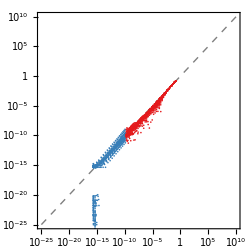

tests/truncation_comparison.pdf

```mathematica
PLOT1 = LogLogPlot[x,{x,10^-25,10^10}, AspectRatio -> 1, PlotStyle -> Directive[Gray,Dashed], Frame -> True, Evaluate[DefaultPlotOptions]];
PLOT2 = ListLogLogPlot[{MyTruncationComparison,MyTruncationComparisonFlipped}, AspectRatio -> 1, PlotRange -> All, Frame -> True, PlotStyle-> {ColorForPositiveValues,ColorForNegativeValues}];
Show[PLOT1,PLOT2]
Export[PathForTests<>"truncation_comparison.pdf",%]
```

## Checking Robustness of N1MM Primaries

```mathematica
(* Example Model *)
MyN1MM = DefaultN1MMModel;
MyReferenceModel = DefaultReferenceModelFor[DefaultN1MMModel];

(* Get statistics *)
MyN1MMStatistics = LossStatisticsOnTaus[MyN1MM,MyReferenceModel,DefaultCoarseDeterministicTaus]
```

<|mean→0.60201,variance→0.750058,skewness→4.89523,kurtosis→36.0929,median→0.36996,minus2sigma→0.000127596,minus1sigma→0.0414383,plus1sigma→1.02841,plus2sigma→2.39722|>

```mathematica
MyNumPrimaries = NumberOfPrimariesOf[MyN1MM];
MyRemoveAndDuplicateTable = Monitor[Table[
{i,
PrimariesOf[MyN1MM][[i]],
LossMeanOnTaus[RemovePrimaryFrom[MyN1MM,i],MyReferenceModel,DefaultCoarseDeterministicTaus],
LossMeanOnTaus[DuplicatePrimaryFrom[MyN1MM,i],MyReferenceModel,DefaultCoarseDeterministicTaus]
}
, {i, 1, MyNumPrimaries}],{i,MyNumPrimaries}];

MyRemoveAndDuplicateTable//MatrixForm
```

(1 | DSD[0,0,1] | 1.43671×10^15 | 1.43671×10^15
2 | DSD[3/35,0,1] | 5.58141×10^12 | 5.58141×10^12
3 | DSD[29/280,0,1] | 3.20337×10^12 | 3.20337×10^12
4 | DSD[9/56,0,1] | 9.28896×10^13 | 9.28896×10^13
5 | DSD[8/35,0,1] | 1.69315×10^14 | 1.69315×10^14
6 | DSD[3/7,0,1] | 9.41539×10^13 | 9.41539×10^13
7 | DSD[27/40,0,1] | 1.46721×10^13 | 1.46721×10^13
8 | DSD[269/280,0,1] | 1.07402×10^12 | 1.07402×10^12
9 | DSD[38/35,0,1] | 3.18113×10^11 | 3.18113×10^11
10 | DSD[43/35,0,1] | 7.66179×10^10 | 7.6618×10^10
11 | DSD[73/56,0,1] | 3.58974×10^10 | 3.58975×10^10
12 | DSD[10/7,0,1] | 1.00162×10^10 | 1.00162×10^10
13 | DSD[9/5,0,1] | 2.11449×10^8 | 2.11458×10^8
14 | DSD[589/280,0,1] | 8.65808×10^6 | 8.65999×10^6
15 | DSD[16/7,0,1] | 1.26086×10^6 | 1.26161×10^6
16 | DSD[14/5,0,1] | 5391.8 | 5441.81
17 | DSD[829/280,0,1] | 978.505 | 999.635
18 | DSD[3,0,1] | 644.585 | 661.674
19 | DSD[108/35,0,1] | 259.152 | 269.878
20 | DSD[113/35,0,1] | 56.7328 | 61.616
21 | DSD[23/7,0,1] | 30.9518 | 34.4995
22 | DSD[185/56,0,1] | 25.6291 | 28.8374
23 | DSD[31/8,0,1] | 0.636652 | 0.712292
24 | DSD[309/280,1,1] | 3.83035×10^11 | 3.83035×10^11
25 | DSD[549/280,1,1] | 5.85465×10^7 | 5.85384×10^7
26 | DSD[73/35,1,1] | 1.58154×10^7 | 1.58111×10^7
27 | DSD[78/35,1,1] | 3.53007×10^6 | 3.528×10^6
28 | DSD[129/56,1,1] | 1.60435×10^6 | 1.60294×10^6
29 | DSD[869/280,1,1] | 359.743 | 336.891
30 | DSD[1109/280,1,1] | 0.845028 | 0.460211
31 | DSD[589/280,2,1] | 1.2916×10^7 | 1.29163×10^7
32 | DSD[78/35,2,1] | 3.34288×10^6 | 3.3431×10^6
33 | DSD[829/280,2,1] | 1290.83 | 1299.69
34 | DSD[113/35,2,1] | 76.0498 | 78.1568
35 | DSD[24/7,2,1] | 9.80057 | 10.4055
36 | DSD[108/35,3,1] | 543.294 | 557.43
37 | DSD[869/280,3,1] | 448.568 | 461.314
38 | DSD[177/56,3,1] | 243.074 | 252.207
39 | DSD[113/35,3,1] | 117.553 | 123.668
40 | DSD[147/40,3,1] | 1.55916 | 1.8492
41 | DSD[1109/280,3,1] | 0.680166 | 0.645478)

## Checking Minimization of N1MM For How Much Distortion

```mathematica
MyMValue = 5;
MyMaxDelta = 4;
MyFixedN1MM = N1MM[MyMValue,MyMaxDelta];
MyReferenceModel = DefaultReferenceModelFor[MyFixedN1MM];

MyFlexibleModel = FloatFloatableDeltasOf[MyFixedN1MM,DefaultMaxDelta];
MyFlexibleModel = RenameOf[MyFlexibleModel, N1MMTitle[MyMValue,MyMaxDelta, DefaultTau2Max]];

MyStartingReplacement = FixedReplacementFor[MyFlexibleModel,MyFixedN1MM];


MyDeterministicTaus = DefaultCoarseDeterministicTaus;
MyTauSamplerData = DefaultLargeTauSampler;
MySingularValueDescent = AlgorithmData[300,0.1, SingularValueDescentData[12,10^-12]];

MySVFilename= "stored_sv_n1mm_optimization.m"
```

stored_sv_n1mm_optimization.m

```mathematica
OptimizationResultFrom[
MyFlexibleModel,
MyReferenceModel,
MyStartingReplacement,
MyDeterministicTaus, 
MyTauSamplerData, 
MySingularValueDescent,
MySVFilename]
```

OptimizationResultFrom[MyFlexibleModel,DeformedCFTData[CFTData[{Free Boson Circle Branch,: ,R=,√2,, ,Δ_max=,6},1,{DSD[1/4,0,2],DSD[1,0,4],DSD[5/4,1,2],DSD[2,0,1],DSD[9/4,0,2],DSD[3,1,2],DSD[13/4,3,2],DSD[4,0,4],DSD[17/4,2,2],DSD[5,4,4],DSD[0,0,1],DSD[1,1,1],DSD[2,2,2]},6,{}],81/70,6],MyStartingReplacement,MyDeterministicTaus,MyTauSamplerData,MySingularValueDescent,MySVFilename]

```mathematica
MyStartingModel= ApplyReplacementTo[MyFlexibleModel, MyStartingReplacement]

MySVResult=Get[MySVFilename];
MySVEndingLoss= LastTestLossOf[MySVResult]
MySVEndingReplacement= LastReplacementOf[MySVResult];
MySVEndingModel= ApplyReplacementTo[MyFlexibleModel, MySVEndingReplacement]

start = DeltaOf/@PrimariesOf[MyStartingModel];
end = DeltaOf/@PrimariesOf[MySVEndingModel];
ListPlot[(2*Abs[start - end])/(start+end), PlotRange ->All]
```

ApplyReplacementTo[MyFlexibleModel,MyStartingReplacement]

Get::stream: MySVFilename is not a string, SocketObject, InputStream[ ] or OutputStream[ ].

LastTestLossOf[$Failed]

ApplyReplacementTo[MyFlexibleModel,LastReplacementOf[$Failed]]

ListPlot::lpn: (2. Abs[PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,MyStartingReplacement]]]-1. PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,LastReplacementOf[«1»]]]]])/(PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,MyStartingReplacement]]]+PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,LastReplacementOf[$Failed]]]]) is not a list of numbers or pairs of numbers.

ListPlot[(2 Abs[PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,MyStartingReplacement]]]-PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,LastReplacementOf[$Failed]]]]])/(PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,MyStartingReplacement]]]+PrimariesOf[DeltaOf[ApplyReplacementTo[MyFlexibleModel,LastReplacementOf[$Failed]]]]),PlotRange→All]

## Additional Plots

### Colloquium Plots

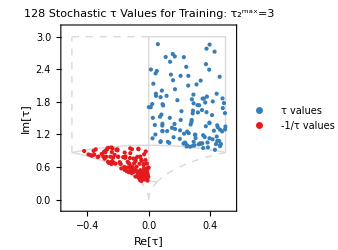

tests/tau_extra_extra_large_stochastic.pdf

```mathematica
MyTau2Max = 3;
MyExtraExtraLargeStochasticTaus = StochasticTauValues[TauSamplerData[128,MyTau2Max]];
MyExtraExtraLargeStochasticPlot= TauPlot[MyExtraExtraLargeStochasticTaus,MyTau2Max, ToString[Length[MyExtraExtraLargeStochasticTaus]]<>" Stochastic τ Values for Training: τ_2^max="<>ToString[MyTau2Max]]
Export[PathForTests<>"tau_extra_extra_large_stochastic.pdf",MyExtraExtraLargeStochasticPlot]
```

# Basic Paper Plots

## For Paper: Basic Visualizations

## Example CFT Spectra

### N=1 Minimal Models

```mathematica
MyNumEntries = 5;
MyMValues = {5,6,7,8,9};
MyFilenames = {"n1mm_spectrum_m5.pdf","n1mm_spectrum_m6.pdf","n1mm_spectrum_m7.pdf","n1mm_spectrum_m8.pdf","n1mm_spectrum_m9.pdf"};
MyColors = ({#,Darker[#,0.1],Darker[#,0.2],Darker[#,0.3],Darker[#,0.4]})&[ColorForN1MM]

MyModels = Table[N1MM[MyMValues[[i]],DefaultMaxDelta], {i,1, MyNumEntries}];
MyPlots = Table[PlotOf[
MyModels[[i]],
MyColors[[i]],
LossValue-> LossMeanOnTaus[MyModels[[i]],DefaultReferenceModelFor[MyModels[[i]]],DefaultFineDeterministicTaus]
], {i,1,MyNumEntries}];
MyPlots[[1]]
Table[Export[PathForPlots<>MyFilenames[[i]],MyPlots[[i]]], {i,1,MyNumEntries}]
```

{RGBColor[1., 0.4980392156862745, 0.],RGBColor[0.9, 0.44823529411764707, 0.],RGBColor[0.8, 0.3984313725490196, 0.],RGBColor[0.7, 0.34862745098039216, 0.],RGBColor[0.6, 0.2988235294117647, 0.]}

-Graphics-

{plots/n1mm_spectrum_m5.pdf,plots/n1mm_spectrum_m6.pdf,plots/n1mm_spectrum_m7.pdf,plots/n1mm_spectrum_m8.pdf,plots/n1mm_spectrum_m9.pdf}

### FBCB

```mathematica
MyNumEntries = 4;
MyRValues = {1,Sqrt[2],Sqrt[3],2};
MyFilenames = {"fbcb_spectrum_rsqrt1.pdf","fbcb_spectrum_rsqrt2.pdf","fbcb_spectrum_rsqrt3.pdf","fbcb_spectrum_rsqrt4.pdf"};
MyColors = ({Lighter[#,0.15],#,Darker[#,0.15],Darker[#,0.3]})&[ColorForFBCB]

MyModels = Table[FBCB[MyRValues[[i]],DefaultMaxDeltaForReference], {i,1, MyNumEntries}];
MyPlots = Table[PlotOf[MyModels[[i]],MyColors[[i]]], {i,1,MyNumEntries}];
MyPlots[[2]]
Table[Export[PathForPlots<>MyFilenames[[i]],MyPlots[[i]]], {i,1,MyNumEntries}]
```

{RGBColor[0.6566666666666666, 0.41000000000000003, 0.6933333333333332],RGBColor[0.596078431372549, 0.3058823529411765, 0.6392156862745098],RGBColor[0.5066666666666667, 0.26, 0.5433333333333333],RGBColor[0.4172549019607843, 0.21411764705882355, 0.44745098039215686]}

-Graphics-

{plots/fbcb_spectrum_rsqrt1.pdf,plots/fbcb_spectrum_rsqrt2.pdf,plots/fbcb_spectrum_rsqrt3.pdf,plots/fbcb_spectrum_rsqrt4.pdf}

## Tau Ranges

### Baseline Tau Values and Visualization

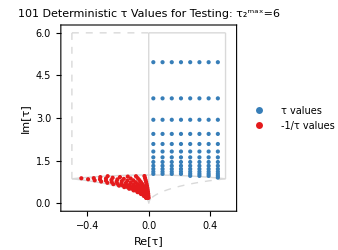
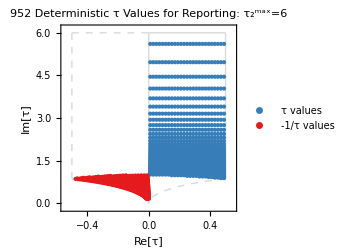
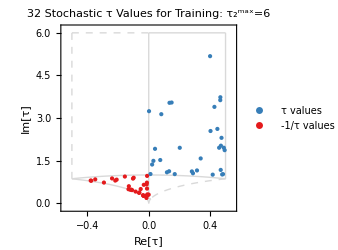

plots/tau_coarse_deterministic.pdf

plots/tau_fine_deterministic.pdf

plots/tau_large_stochastic.pdf

```mathematica
MyCoarseDeterministicPlot = TauPlot[DefaultCoarseDeterministicTaus,DefaultTau2Max, ToString[Length[DefaultCoarseDeterministicTaus]]<>" Deterministic τ Values for Testing: τ_2^max="<>ToString[DefaultTau2Max]];

MyFineDeterministicPlot = TauPlot[DefaultFineDeterministicTaus,DefaultTau2Max, ToString[Length[DefaultFineDeterministicTaus]]<>" Deterministic τ Values for Reporting: τ_2^max="<>ToString[DefaultTau2Max]];

MyLargeStochasticTaus = StochasticTauValues[DefaultLargeTauSampler];
MyLargeStochasticPlot= TauPlot[MyLargeStochasticTaus,DefaultTau2Max, ToString[Length[MyLargeStochasticTaus]]<>" Stochastic τ Values for Training: τ_2^max="<>ToString[DefaultTau2Max]];

{MyCoarseDeterministicPlot,MyFineDeterministicPlot,MyLargeStochasticPlot}

Export[PathForPlots<>"tau_coarse_deterministic.pdf",MyCoarseDeterministicPlot]
Export[PathForPlots<>"tau_fine_deterministic.pdf",MyFineDeterministicPlot]
Export[PathForPlots<>"tau_large_stochastic.pdf",MyLargeStochasticPlot]
```

## For Paper: Method Validation with N1MM

## Impact of Reference Model

### Table of Loss Values as a function of R

```mathematica
(* These are formatted to make a latex table *)
RSquaredList = {1,2,3,4}
RNameOf[1] = "\\hline$R=1$";
RNameOf[2]= "$\\boldsymbol{R=\\sqrt{2}}$";
RNameOf[3]= "$R=\\sqrt{3}$";
RNameOf[4]= "$R=2$";
RNameOf[5]= "$R=\\sqrt{5}$";

MList = {5,6,7,8,9}
MNameOf[5] = "$m=5$";
MNameOf[6] = "$m=6$";
MNameOf[7] = "$m=7$";
MNameOf[8] = "$m=8$";
MNameOf[9] = "$m=9$";

MyN1MMAltReference[rvalue_,m_,cut_] :=  DeformedCFTData[FBCB[rvalue,cut+DefaultDeltaOffset],CentralChargeOf[N1MM[m,cut]] ,cut+DefaultDeltaOffset];

MyRScanTable = Monitor[Join[{Join[{""},MNameOf/@MList]},
Table[Join[{RNameOf[rsquared]},(If[rsquared==2,"$\\mathbf{","$"]<>(ToString[SetPrecision[
monitor = {#,rsquared};LossMeanOnTaus[N1MM[#,DefaultMaxDelta],MyN1MMAltReference[Sqrt[rsquared],#,DefaultMaxDelta],DefaultFineDeterministicTaus]
,3]]<>If[rsquared==2,"}$","$"])&/@MList)], {rsquared,RSquaredList}]
]//MatrixForm,
monitor]
Export[PathForPlots<>"n1mm_m_vs_r_table.tex",%,"Table","FieldSeparators"->" & ","LineSeparators"->" \\\\\n"]
```

{1,2,3,4}

{5,6,7,8,9}

( | $m=5$ | $m=6$ | $m=7$ | $m=8$ | $m=9$
\hline$R=1$ | $0.851$ | $1.16$ | $1.29$ | $1.40$ | $1.65$
$\boldsymbol{R=\sqrt{2}}$ | $\mathbf{0.649}$ | $\mathbf{0.904}$ | $\mathbf{1.02}$ | $\mathbf{1.12}$ | $\mathbf{1.32}$
$R=\sqrt{3}$ | $1.58$ | $1.89$ | $2.03$ | $2.13$ | $2.48$
$R=2$ | $0.777$ | $1.03$ | $1.14$ | $1.24$ | $1.46$)

plots/n1mm_m_vs_r_table.tex

## Statistical Check

### Weight Distributions

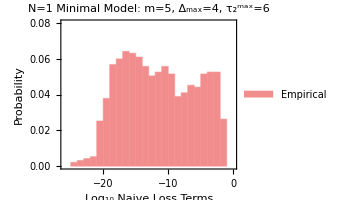

plots/n1mm_loss_histo_naive.pdf

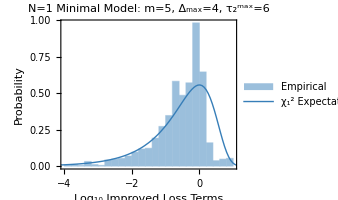

plots/n1mm_loss_histo_improved.pdf

```mathematica
MyRawLossesNaive =Log[10,Re[ObjectiveFunction[DefaultN1MMModel,Null][#]]^2] &/@ DefaultFineDeterministicTaus;
MyRawLossesImproved = Log[10,Re[ObjectiveFunction[DefaultN1MMModel,DefaultReferenceModelFor[DefaultN1MMModel]][#]]^2] &/@ DefaultFineDeterministicTaus;

MyBaseStyle = Sequence[DefaultPlotOptions, AspectRatio -> 0.8,ImageSize -> 300, PlotLabel->NiceTitle[N1MMTitle[DefaultMValue,DefaultMaxDelta, DefaultTau2Max]]];

(* Naive *)
Histogram[MyRawLossesNaive,{-26,0,1},"PDF", 
Evaluate[MyBaseStyle],
FrameLabel-> {"Log_10 Naive Loss Terms","Probability"},ChartStyle->Lighter[ColorForNaiveLoss,0.5],
ChartLegends-> Placed[{"  Empirical"},{Scaled[{0.25,0.89}], {0, 1}}],
PlotRange -> {0,0.08}]
Export[PathForPlots<>"n1mm_loss_histo_naive.pdf",%]


(* Improved *)
plot1 = Histogram[MyRawLossesImproved, {-4,1,0.2},"PDF",
Evaluate[MyBaseStyle],
FrameLabel-> {"Log_10 Improved Loss Terms","Probability"},
ChartStyle->Lighter[ColorForImprovedLoss,0.5],
ChartLegends-> Placed[{"  Empirical"},{Scaled[{0.25,0.89}], {0, 1}}]
];
plot2 = Plot[(2^(-1/2+a/2) 5^(a/2) ⅇ^(-2^(-1+a) 5^a) Log[10])/(√π), {a,-100,100},
PlotRange -> All,
Evaluate[MyBaseStyle],
PlotStyle->Directive[ColorForImprovedLoss,Thickness[Large]],
PlotLegends-> Placed[{"χ_1^2 Expectation"},{Scaled[{0.05,0.85}], {0, 1}}]
];
Show[plot1,plot2]

Export[PathForPlots<>"n1mm_loss_histo_improved.pdf",%]
```

## Hyperparameter Scans

### Cut Scan

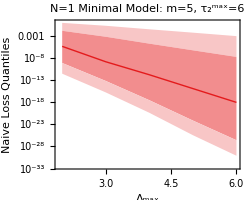

plots/n1mm_cut_scan_naive.pdf

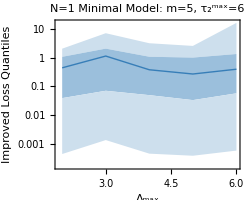

plots/n1mm_cut_scan_improved.pdf

```mathematica
MyMValue = 5;
MyCutList = {2,3,4,5,6};

MyN1MMCutScanNaive:=MyN1MMCutScanNaive=<|
"points"-> ((<|"Δ_max"-> #,"statistics"-> (LossStatisticsOnTaus[N1MM[MyMValue,#],Null,DefaultFineDeterministicTaus])|>)&/@MyCutList)
|>;

PlotMedianRangeFrom[ N1MMTitle[MyMValue,None, DefaultTau2Max],"Δ_max", "Naive Loss Quantiles", MyN1MMCutScanNaive, ColorForNaiveLoss]
Export[PathForPlots<>"n1mm_cut_scan_naive.pdf",%]

MyN1MMCutScanImproved:= MyN1MMCutScanImproved=<|
"points"-> ((<|"Δ_max"-> #,"statistics"-> (LossStatisticsOnTaus[N1MM[MyMValue,#],DefaultReferenceModelFor[N1MM[MyMValue,#]],DefaultFineDeterministicTaus])|>)&/@MyCutList)
|>;

PlotMedianRangeFrom[N1MMTitle[MyMValue,None, DefaultTau2Max],"Δ_max", "Improved Loss Quantiles",MyN1MMCutScanImproved,ColorForImprovedLoss]
Export[PathForPlots<>"n1mm_cut_scan_improved.pdf",%]
```

### Tau2 Scan

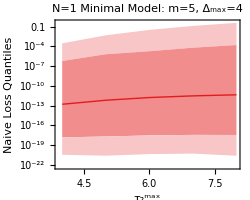

plots/n1mm_tau2_scan_naive.pdf

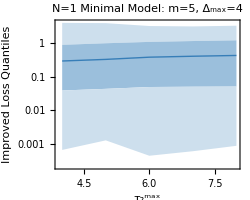

plots/n1mm_tau2_scan_improved.pdf

```mathematica
MyTau2MaxList = {4,5,6,7,8};
MyFineDeterministicTaus[tau2max_]:= DeterministicTauValues[DefaultFineTau1Width, DefaultFineTau2Width,tau2max]

MyN1MMTau2ScanNaive:=MyN1MMTau2ScanNaive=<|
"points"-> ((<|"τ_2^max"-> #,"statistics"-> (LossStatisticsOnTaus[DefaultN1MMModel,Null,MyFineDeterministicTaus[#]])|>)&/@MyTau2MaxList)
|>;

PlotMedianRangeFrom[ N1MMTitle[MyMValue,DefaultMaxDelta, None],"τ_2^max", "Naive Loss Quantiles", MyN1MMTau2ScanNaive, ColorForNaiveLoss]
Export[PathForPlots<>"n1mm_tau2_scan_naive.pdf",%]

MyN1MMTau2ScanImproved:= MyN1MMTau2ScanImproved=<|
"points"-> ((<|"τ_2^max"-> #,"statistics"-> (LossStatisticsOnTaus[DefaultN1MMModel,DefaultReferenceModelFor[DefaultN1MMModel],MyFineDeterministicTaus[#]])|>)&/@MyTau2MaxList)
|>;

PlotMedianRangeFrom[N1MMTitle[MyMValue,DefaultMaxDelta, None],"τ_2^max", "Improved Loss Quantiles",MyN1MMTau2ScanImproved, ColorForImprovedLoss]
Export[PathForPlots<>"n1mm_tau2_scan_improved.pdf",%]
```

### M Scan (Not currently shown in paper)

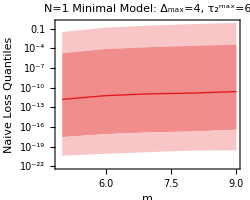

tests/n1mm_m_scan_naive.pdf

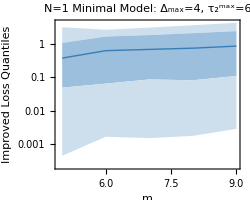

tests/n1mm_m_scan_improved.pdf

```mathematica
MyMList = {5,6,7,8,9};

MyN1MMMScanNaive:=MyN1MMMScanNaive=<|
"points"-> ((<|Style["m",Italic]-> #,"statistics"-> (LossStatisticsOnTaus[N1MM[#,DefaultMaxDelta],Null,DefaultFineDeterministicTaus])|>)&/@MyMList)
|>;

PlotMedianRangeFrom[ N1MMTitle[None,DefaultMaxDelta, DefaultTau2Max],Style["m",Italic], "Naive Loss Quantiles", MyN1MMMScanNaive, ColorForNaiveLoss]
Export[PathForTests<>"n1mm_m_scan_naive.pdf",%]

MyN1MMMScanImproved:=MyN1MMMScanImproved=<|
"points"-> ((<|Style["m",Italic]-> #,"statistics"-> (LossStatisticsOnTaus[N1MM[#,DefaultMaxDelta],DefaultReferenceModelFor[N1MM[#,DefaultMaxDelta]],DefaultFineDeterministicTaus])|>)&/@MyMList)
|>;

PlotMedianRangeFrom[ N1MMTitle[None,DefaultMaxDelta, DefaultTau2Max],Style["m",Italic], "Improved Loss Quantiles", MyN1MMMScanImproved, ColorForImprovedLoss]
Export[PathForTests<>"n1mm_m_scan_improved.pdf",%]
```

## Uncertainty Analysis

-Graphics-

Getting inverse covariance (this takes a long time)...

Doing profiled...

Doing pairwise...

Doing tripletwise...

Doing quadrupletwise...

General::munfl: Exp[-846.245] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(8.12174×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2320.35] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

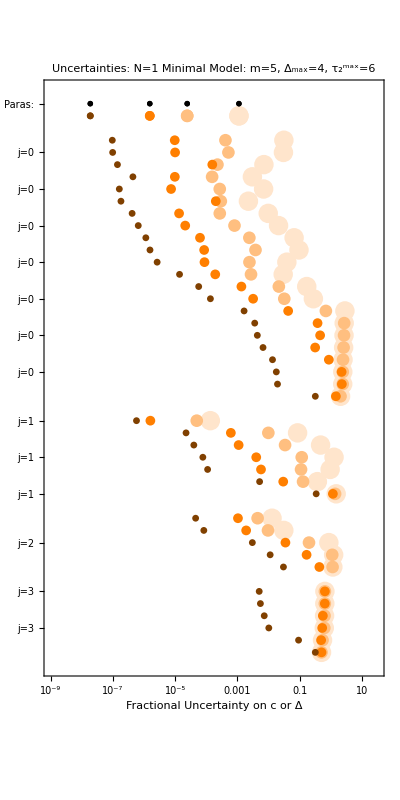

plots/n1mm_uncertainty.pdf

```mathematica
MyMValue = 5;
MyMaxDelta = 4;
MyFixedN1MM = N1MM[MyMValue,MyMaxDelta];
MyReferenceModel = DefaultReferenceModelFor[MyFixedN1MM];

MyMinCC = 1;
MyMaxCC = 81/70*2;
MyFlexibleN1MM = FloatFloatableDeltasOf[FloatCentralChargeOf[MyFixedN1MM,MyMinCC,MyMaxCC],DefaultMaxDelta];
MyFlexibleN1MM = RenameOf[MyFlexibleN1MM, N1MMTitle[MyMValue,MyMaxDelta, DefaultTau2Max]];

(* Pretending like model is the outcome of minimization*)
MyEndingReplacement = FixedReplacementFor[MyFlexibleN1MM,MyFixedN1MM];
MyEndingModel = ApplyReplacementTo[MyFixedN1MM,MyEndingReplacement];
PlotOf[MyEndingModel, ColorForN1MM]

(* Find uncertainties and plot them*)
Print["Getting inverse covariance (this takes a long time)..."]
MyUncertaintyReplacement = ReplacementWithUncertaintiesOnTaus[MyFlexibleN1MM, MyReferenceModel, MyEndingReplacement, DefaultFineDeterministicTaus];

Print["Doing profiled..."]
ProfiledUncertainties[MyUncertaintyReplacement];

Print["Doing pairwise..."]
PairwiseMarginalUncertainties[MyUncertaintyReplacement];

Print["Doing tripletwise..."]
TripletwiseMarginalUncertainties[MyUncertaintyReplacement];

Print["Doing quadrupletwise..."]
QuadrupletwiseMarginalUncertainties[MyUncertaintyReplacement];

DeltaUncertaintyPlotOf[MyFlexibleN1MM,MyUncertaintyReplacement, ColorForN1MM]
Export[PathForPlots<>"n1mm_uncertainty.pdf",%]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.59909×10^14,-2.59747×10^14,-2.52422×10^14,-1.75449×10^14,-5.36345×10^13,1.47887×10^14,1.26485×10^14,5.28284×10^13,3.27893×10^13,1.82203×10^13,1.31967×10^13,«20»,-8.15943×10^9,-4.12682×10^8,-1.0295×10^8,-3.51536×10^7,3.96182×10^7,4.30616×10^7,4.75884×10^7,4.51798×10^7,8.99114×10^6,2.16226×10^6},«39»,{«1»}} may contain significant numerical errors.

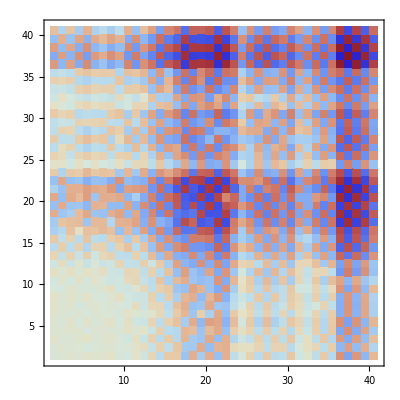

tests/inverse_covariance_visualization.pdf

```mathematica
ListDensityPlot[(Sign[#]*Log[Abs[#]])&/@Inverse[InverseCovarianceOf[MyUncertaintyReplacement]], ColorFunction -> "ThermometerColors",InterpolationOrder->0]
Export[PathForTests<>"inverse_covariance_visualization.pdf",%]
```

# Optimization Campaigns

## For Paper: Optimization Campaign (Baseline Models)

## Setting Up Optimization Campaign

### Optimization Settings and Starting Models

```mathematica
(* These values will certainly need to be adjusted *)
MyNumEpochs = 300;
MyLearningRate = 0.1;
MyMaxSVRatio = 10^-12;

(* Defaults have Tau2Max of 6*)
MyCampaignDeterministicTaus[_] := DefaultCoarseDeterministicTaus;
MyCampaignRefinedDeterministicTaus[_] := DefaultFineDeterministicTaus;
MyCampaignTauSamplerData[_] := DefaultLargeTauSampler;

(* Starting Models*)
MyMaxDelta = 4;
MySpinValues = {0,1,2,3};
MyNumSpin[0] = 24;
MyNumSpin[1] = 18;
MyNumSpin[2] = 12;
MyNumSpin[3] = 6;

MyPrimaries = Flatten[
{{DSD[0, 0,1]},
Table[Table[
DSD[SigmoidEsque[FlexDelta[s,i],s,2*MyMaxDelta - s], s,1],
 {i,1,MyNumSpin[s]}], {s,MySpinValues }]
}];
MyVariables = Flatten[Table[Table[FlexDelta[s,i], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];
(*MyInitialValues = Flatten[Table[Table[3.0*(-1 + i/MyNumSpin[s]), {i,0,MyNumSpin[s]-1}], {s,MySpinValues }]];*)
MyInitialValues = Flatten[Table[Table[Log[(i/(MyNumSpin[s]+1))/(2-i/(MyNumSpin[s]+1))], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];


MyNumCampaign=11;
MyCampaignPrefix = "hunt_";
MyCampaignShortNames = {"c109_grad","c109_sv1","c109_sv2","c109_sv4","c109_sv8","c109_sv16","c109_sv32","c105_sv16","c107_sv16","c111_sv16","c113_sv16"};
MyCampaignCentralCharges = {1.09,1.09,1.09,1.09,1.09,1.09,1.09,1.05,1.07,1.11, 1.13};
MyCampaignSingularValues = {0,1,2,4,8,16,32,16,16,16,16};
MyRValue = Sqrt[2];

PrettyNameOf[MyCampaignPrefix<>"c109_grad"]="Grad. Descent";
PrettyNameOf[MyCampaignPrefix<>"c109_sv1"]="Sven: k_SV=1";
PrettyNameOf[MyCampaignPrefix<>"c109_sv2"]="Sven: k_SV=2";
PrettyNameOf[MyCampaignPrefix<>"c109_sv4"]="Sven: k_SV=4";
PrettyNameOf[MyCampaignPrefix<>"c109_sv8"]="Sven: k_SV=8";
PrettyNameOf[MyCampaignPrefix<>"c109_sv32"]="Sven: k_SV=32";
AltPrettyNameOf[MyCampaignPrefix<>"c109_sv16"]="Sven: k_SV=16";
PrettyNameOf[MyCampaignPrefix<>"c105_sv16"] ="c=1.05 Candidate";
PrettyNameOf[MyCampaignPrefix<>"c107_sv16"]="c=1.07 Candidate";
PrettyNameOf[MyCampaignPrefix<>"c109_sv16"]="c=1.09 Candidate";
PrettyNameOf[MyCampaignPrefix<>"c111_sv16"]="c=1.11 Candidate";
PrettyNameOf[MyCampaignPrefix<>"c113_sv16"]="c=1.13 Candidate";

ColorOf[MyCampaignPrefix<>"c105_sv16"] =Lighter[ColorForCampaign,0.7];
ColorOf[MyCampaignPrefix<>"c107_sv16"]= Lighter[ColorForCampaign,0.35];
ColorOf[MyCampaignPrefix<>"c109_sv16"]= ColorForCampaign;
ColorOf[MyCampaignPrefix<>"c111_sv16"]= Darker[ColorForCampaign,0.35];
ColorOf[MyCampaignPrefix<>"c113_sv16"]= Darker[ColorForCampaign,0.7];

ColorOf[MyCampaignPrefix<>"c109_grad"]= ColorForNaiveLoss;
ColorOf[MyCampaignPrefix<>"c109_sv1"]= Lighter[Blend[{ColorForCampaign,ColorForImprovedLoss},1],0.8];
ColorOf[MyCampaignPrefix<>"c109_sv2"]= Lighter[Blend[{ColorForCampaign,ColorForImprovedLoss},0.75],0.6];
ColorOf[MyCampaignPrefix<>"c109_sv4"]= Lighter[Blend[{ColorForCampaign,ColorForImprovedLoss},0.5],0.4];
ColorOf[MyCampaignPrefix<>"c109_sv8"]= Lighter[Blend[{ColorForCampaign,ColorForImprovedLoss},0.25],0.2];
AltColorOf[MyCampaignPrefix<>"c109_sv16"]= ColorForCampaign;
ColorOf[MyCampaignPrefix<>"c109_sv32"]= Blue;


(* Things that have to be defined model specifically *)
MyCampaignNames = {};
For[i = 1, i <= MyNumCampaign, i++,
MyLongName = MyCampaignPrefix<>MyCampaignShortNames[[i]];
AppendTo[MyCampaignNames, MyLongName];
MyCampaignFlexibleModel[MyLongName] = CFTData[MyLongName,MyCampaignCentralCharges[[i]],MyPrimaries, MyMaxDelta, MyVariables];
MyCampaignReferenceModel[MyLongName] = DefaultReferenceModelFor[MyCampaignFlexibleModel[MyLongName]];
MyCampaignStartingReplacement[MyLongName] = ReplacementData[MyVariables,MyInitialValues,{}];

(* No validation step for this *)
MyCampaignAlgorithmDetails[MyLongName] = If[MyCampaignSingularValues[[i]]==0,GradientDescentData[], SingularValueDescentData[MyCampaignSingularValues[[i]],MyMaxSVRatio]];
MyCampaignAlgorithm[MyLongName] =AlgorithmData[MyNumEpochs,MyLearningRate,MyCampaignAlgorithmDetails[MyLongName]];
]

(* Outputting names to make sure they look right*)
MyCampaignNames
MyCampaignDefaultName= MyCampaignNames[[6]]
```

{hunt_c109_grad,hunt_c109_sv1,hunt_c109_sv2,hunt_c109_sv4,hunt_c109_sv8,hunt_c109_sv16,hunt_c109_sv32,hunt_c105_sv16,hunt_c107_sv16,hunt_c111_sv16,hunt_c113_sv16}

hunt_c109_sv16

### Plotting Starting Model

```mathematica
Validate[MyCampaignStartingModel[#]]&/@MyCampaignNames
(*MyCampaignStartingLoss/@ MyCampaignNames*)

(* Output Starting Spectrum*)
MyCampaignStartingPlot[MyCampaignDefaultName]
Export[PathForPlots<>MyCampaignDefaultName<>"_starting_plot.pdf",%]
```

{True,True,True,True,True,True,True,True,True,True,True}

-Graphics-

plots/hunt_c109_sv16_starting_plot.pdf

### Checking For Existing Files

```mathematica
{Unset[MyCampaignResult[#]];#,FileExistsQ[MyCampaignFilename[#]], NumIterationsOf[MyCampaignResult[#]]}&/@MyCampaignNames
```

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[hunt_c109_grad] not found.

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[hunt_c109_sv1] not found.

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[hunt_c109_sv2] not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{{hunt_c109_grad,True,301},{hunt_c109_sv1,True,301},{hunt_c109_sv2,True,301},{hunt_c109_sv4,True,301},{hunt_c109_sv8,True,301},{hunt_c109_sv16,True,301},{hunt_c109_sv32,True,301},{hunt_c105_sv16,True,301},{hunt_c107_sv16,True,301},{hunt_c111_sv16,True,301},{hunt_c113_sv16,True,301}}

## Running Optimization

### Running Optimization

```mathematica
(* The core optimization is here! *)
MyRemainingNames = Select[MyCampaignNames,(Not[FileExistsQ[MyCampaignFilename[#]]]||NumIterationsOf[MyCampaignResult[#]]<MyNumEpochs)&];
(*The core optimization is here!*)
ParallelTable[
RunOptimizationFor[MyRemainingNames[[i]]];
,{i,1,Length[MyRemainingNames]}
]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of A front end is not available; certain operations require a front end. will be suppressed during this calculation.

{AlgorithmData[300,0.1,GradientDescentData[]],301,1.80653×10^10,4.00019×10^10}

{AlgorithmData[300,0.1,SingularValueDescentData[1,1/1000000000000]],301,3.99021×10^12,3.28791×10^12}

{AlgorithmData[300,0.1,SingularValueDescentData[2,1/1000000000000]],301,6.14103×10^8,1.31807×10^9}

{AlgorithmData[300,0.1,SingularValueDescentData[4,1/1000000000000]],301,221796.,122111.}

{AlgorithmData[300,0.1,SingularValueDescentData[8,1/1000000000000]],301,488.956,180.304}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.188761,0.137759}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.254396,0.866472}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.290536,0.0327193}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.596404,0.461565}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.0840064,0.0151086}

{AlgorithmData[300,0.1,SingularValueDescentData[32,1/1000000000000]],301,0.63731,1.69301}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Analysis of Results

### Reading In Stored Information and Processing

```mathematica
(* In case the file has updated *)
Unset[MyCampaignResult[#]]&/@MyCampaignNames;
MyCampaignResult/@MyCampaignNames;

(* Make sure model definition is the same*)
(* Because the names can be different, have to guard against that*)
(RenameOf[MyCampaignStoredFlexibleModel[#],#]== MyCampaignFlexibleModel[#])&/@ MyCampaignNames

(* Check that losses went down*)
MyCampaignEndingLoss/@MyCampaignNames
MyCampaignEndingLossRefined/@MyCampaignNames

(* Outputting Final Spectrum*)
MyCampaignEndingPlot[MyCampaignDefaultName]
Export[PathForPlots<>#<>"_ending_plot.pdf",MyCampaignEndingPlot[#]]&/@ MyCampaignNames
Export[PathForPlots<>#<>"_ending_plot_alt.pdf",MyCampaignEndingPlotAlt[#]]&[MyCampaignDefaultName]
```

{True,True,True,True,True,True,True,True,True,True,True}

{1.80653×10^10,3.99021×10^12,6.14103×10^8,221796.,488.956,0.254396,0.63731,0.596404,0.0840064,0.290536,0.188761}

{1.74051×10^10,4.79316×10^12,9.47624×10^8,224724.,1511.87,0.51028,3.14972,0.878485,0.394959,2.24395,1.79648}

-Graphics-

{plots/hunt_c109_grad_ending_plot.pdf,plots/hunt_c109_sv1_ending_plot.pdf,plots/hunt_c109_sv2_ending_plot.pdf,plots/hunt_c109_sv4_ending_plot.pdf,plots/hunt_c109_sv8_ending_plot.pdf,plots/hunt_c109_sv16_ending_plot.pdf,plots/hunt_c109_sv32_ending_plot.pdf,plots/hunt_c105_sv16_ending_plot.pdf,plots/hunt_c107_sv16_ending_plot.pdf,plots/hunt_c111_sv16_ending_plot.pdf,plots/hunt_c113_sv16_ending_plot.pdf}

plots/hunt_c109_sv16_ending_plot_alt.pdf

### Loss Function Evolution

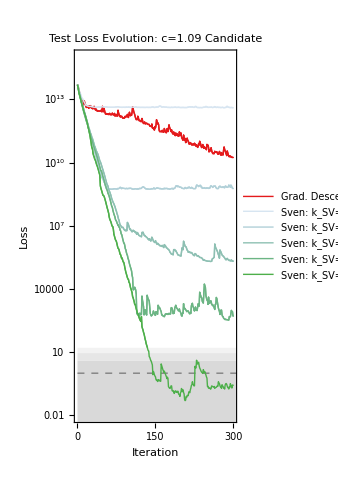

plots/hunt_c109_loss_vs_iter.pdf

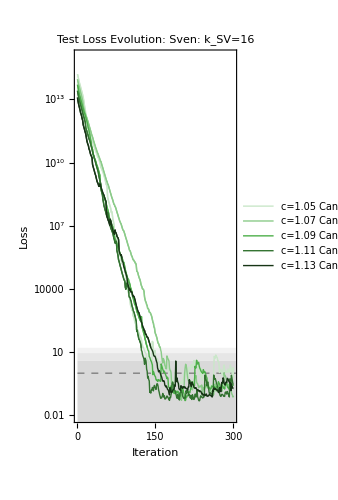

plots/hunt_sv16_loss_vs_iter.pdf

```mathematica
PlotLossVersusIterationOf["Test Loss Evolution: c=1.09 Candidate", 
{ColorOf[MyCampaignPrefix<>"c109_grad"],
ColorOf[MyCampaignPrefix<>"c109_sv1"],
ColorOf[MyCampaignPrefix<>"c109_sv2"],
ColorOf[MyCampaignPrefix<>"c109_sv4"],
ColorOf[MyCampaignPrefix<>"c109_sv8"],
ColorOf[MyCampaignPrefix<>"c109_sv16"](*,
ColorOf[MyCampaignPrefix<>"c109_sv32"]*)
},
{RenameOf[MyCampaignResult[#], PrettyNameOf[#]]&[MyCampaignPrefix<>"c109_grad"],
RenameOf[MyCampaignResult[#], PrettyNameOf[#]]&[MyCampaignPrefix<>"c109_sv1"],
RenameOf[MyCampaignResult[#], PrettyNameOf[#]]&[MyCampaignPrefix<>"c109_sv2"],
RenameOf[MyCampaignResult[#], PrettyNameOf[#]]&[MyCampaignPrefix<>"c109_sv4"],
RenameOf[MyCampaignResult[#], PrettyNameOf[#]]&[MyCampaignPrefix<>"c109_sv8"],
RenameOf[MyCampaignResult[#], AltPrettyNameOf[#]]&[MyCampaignPrefix<>"c109_sv16"] (*,
RenameOf[MyCampaignResult[#], PrettyNameOf[#]]&[MyCampaignPrefix<>"c109_sv32"]*)
}
,PlotRange ->{{0,MyNumEpochs}, {10^-2, 10^15}}]
Export[PathForPlots<>MyCampaignPrefix<>"c109_loss_vs_iter.pdf",%]

PlotLossVersusIterationOf["Test Loss Evolution: Sven: k_SV=16",ColorOf/@MyCampaignNames[[{8,9,6,10,11}]], RenameOf[MyCampaignResult[#],PrettyNameOf[#]]&/@MyCampaignNames[[{8,9,6,10,11}]],PlotRange ->{{0,MyNumEpochs}, {10^-2, 10^15}}]
Export[PathForPlots<>MyCampaignPrefix<>"sv16_loss_vs_iter.pdf",%]

(* These are just for validation *)
(*PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: c=1.09 Candidate", {ColorForNaiveLoss,ColorForImprovedLoss},{MyCampaignGradResult[#],MyCampaignSVResult[#]},1.0]&[MyCampaignDefaultName]

PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: Singular Value Descent",ColorOf/@MyCampaignNames, RenameOf[MyCampaignSVResult[#],PrettyNameOf[#]]&/@MyCampaignNames,1]*)
```

### Uncertainty Analysis

```mathematica
Timing[MyCampaignDeltaUncertaintyPlot[MyCampaignDefaultName]]
```

$Aborted

General::munfl: Exp[-743.287] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-793.047] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-786.88] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

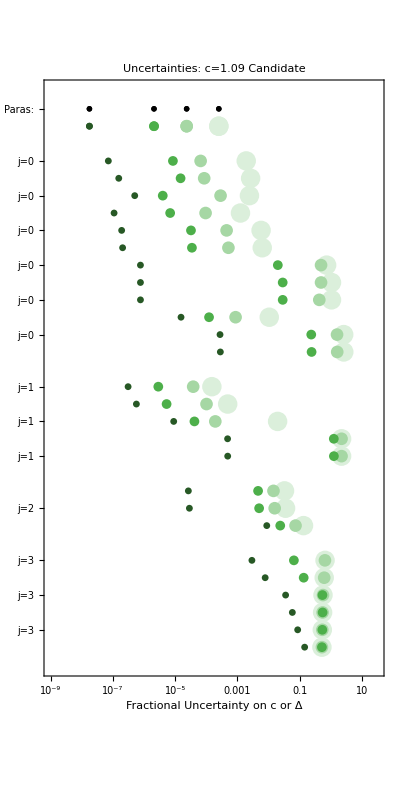

General::munfl: Exp[-7175.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7175.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4577.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ParallelMap[Export[PathForPlots<>#<>"_uncertainty.pdf",MyCampaignDeltaUncertaintyPlot[#]]&, MyCampaignNames[[{8,9,6,10,11}]]]
```

### Additional Diagnostic Plots

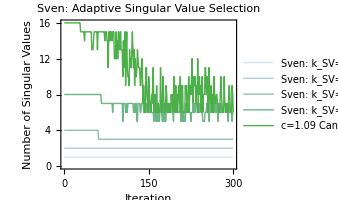

```mathematica
PlotSingularValuesVersusIterationOf["Sven:  Adaptive Singular Value Selection",
ColorOf/@ MyCampaignNames[[{2,3,4,5,6}]],RenameOf[MyCampaignResult[#], PrettyNameOf[#]]&/@MyCampaignNames[[{2,3,4,5,6}]]]
Export[PathForTests<>"singular_value_count.pdf",%]
```

### Final Loss Value Table

```mathematica
(* These are formatted to make a latex table *)
RSquaredList = {1,2,3,4}
RNameOf[1] = "\\hline$R=1$";
RNameOf[2]= "$\\boldsymbol{R=\\sqrt{2}}$";
RNameOf[3]= "$R=\\sqrt{3}$";
RNameOf[4]= "$R=2$";
RNameOf[5]= "$R=\\sqrt{5}$";

CList = {MyCampaignPrefix<>"c105_sv16",MyCampaignPrefix<>"c107_sv16",MyCampaignPrefix<>"c109_sv16",MyCampaignPrefix<>"c111_sv16",MyCampaignPrefix<>"c113_sv16"}
CNameOf[MyCampaignPrefix<>"c105_sv16"] = "$c=1.05$";
CNameOf[MyCampaignPrefix<>"c107_sv16"] = "$c=1.07$";
CNameOf[MyCampaignPrefix<>"c109_sv16"] = "$c=1.09$";
CNameOf[MyCampaignPrefix<>"c111_sv16"] = "$c=1.11$";
CNameOf[MyCampaignPrefix<>"c113_sv16"] = "$c=1.13$";

MyCampaignAltReference[rvalue_,name_,cut_] :=  DeformedCFTData[FBCB[rvalue,cut+DefaultDeltaOffset],CentralChargeOf[MyCampaignEndingModel[name]] ,cut+DefaultDeltaOffset];

MyRScanTable = Monitor[Join[{Join[{""},CNameOf/@CList]},
Table[Join[{RNameOf[rsquared]},(If[rsquared==2,"$\\mathbf{","$"]<>(ToString[SetPrecision[
monitor = {#,rsquared};LossMeanOnTaus[HardTruncateOf[MyCampaignEndingModel[#]],MyCampaignAltReference[Sqrt[rsquared],#,DefaultMaxDelta],DefaultFineDeterministicTaus]
,3]]<>If[rsquared==2,"}$","$"])&/@CList)], {rsquared,RSquaredList}]
]//MatrixForm,
monitor]
Export[PathForPlots<>MyCampaignPrefix<>"m_vs_c_table.tex",%,"Table","FieldSeparators"->" & ","LineSeparators"->" \\\\\n"]
```

{1,2,3,4}

{campaign_2026_february_13_base_c105_sv16,campaign_2026_february_13_base_c107_sv16,campaign_2026_february_13_base_c109_sv16,campaign_2026_february_13_base_c111_sv16,campaign_2026_february_13_base_c113_sv16}

( | $c=1.05$ | $c=1.07$ | $c=1.09$ | $c=1.11$ | $c=1.13$
\hline$R=1$ | $1.19$ | $0.528$ | $0.680$ | $3.02$ | $2.39$
$\boldsymbol{R=\sqrt{2}}$ | $\mathbf{0.878}$ | $\mathbf{0.395}$ | $\mathbf{0.510}$ | $\mathbf{2.24}$ | $\mathbf{1.80}$
$R=\sqrt{3}$ | $3.39$ | $1.30$ | $1.61$ | $6.64$ | $5.11$
$R=2$ | $1.14$ | $0.513$ | $0.649$ | $2.78$ | $2.18$)

campaign_2026_february_13_base_m_vs_c_table.tex

## For Paper: Optimization Campaign (Survey)

## Setting Up Optimization Campaign

### Optimization Settings & Starting Models

```mathematica
(* Defaults have Tau2Max of 6*)
MyCampaignDeterministicTaus[_] := DefaultCoarseDeterministicTaus;
MyCampaignRefinedDeterministicTaus[_] := DefaultFineDeterministicTaus;
MyCampaignTauSamplerData[_] := DefaultLargeTauSampler;

(* These values will certainly need to be adjusted *)
MyNumEpochs = 300;
MyLearningRate = 0.1;
MyMaxSVRatio = 10^-12;

MyMaxDelta = 4;
MySpinValues = {0,1,2,3};
MyNumSpin[0] = 24;
MyNumSpin[1] = 18;
MyNumSpin[2] = 12;
MyNumSpin[3] = 6;

Clear[MyPrimaries]
MyPrimaries[pseudogap_] := Flatten[
{{DSD[0, 0,1]},{DSD[pseudogap, 0,1]},
Table[Table[
DSD[SigmoidEsque[FlexDelta[s,i],Max[s,pseudogap],2*MyMaxDelta - Max[s,pseudogap]], s,1],
 {i,1,MyNumSpin[s]}], {s,MySpinValues }]
}];
MyVariables = Flatten[Table[Table[FlexDelta[s,i], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];
MyInitialValues = Flatten[Table[Table[Log[(i/(MyNumSpin[s]+1))/(2-i/(MyNumSpin[s]+1))], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];

MyCampaignPrefix = "survey_max4_sv16_";
MyCampaignSingularValue = 16;
MyRValue = Sqrt[2];
MyCampaignCentralCharges =Table[i,{i,1.0,1.20,0.02}]  (* change to 0.01 for final run*);
MyCampaignDeltaGaps =  Rest[Table[i,{i,0.0,0.6,0.04}] ] (* change to 0.02 for final run *);

(* Things that have to be defined model specifically *)
MyCampaignNames = {};
For[cc = 1, cc <= Length[MyCampaignCentralCharges], cc++,
For[dg = 1, dg <= Length[MyCampaignDeltaGaps], dg++,
ThisCC = MyCampaignCentralCharges[[cc]];
ThisDG = MyCampaignDeltaGaps[[dg]];
MyLongName = MyCampaignPrefix <>"c"<>ToString[Round[ThisCC*100]]<>"_dg"<>ToString[Round[ThisDG*100]];
AppendTo[MyCampaignNames, MyLongName];
PrettyNameOf[MyLongName] = "c="<>ToString[SetAccuracy[ThisCC,3]]<>", Δ_gap="<>ToString[SetAccuracy[ThisDG,3]];
ColorOf[MyLongName] = If[ThisCC/6+1/3>ThisDG,Lighter[ColorForPositiveValues,1.5*(ThisCC/6+1/3-ThisDG)],Lighter[ColorForNegativeValues,-1.5*(ThisCC/6+1/3-ThisDG)]];
MyCampaignPrimaries[MyLongName] = MyPrimaries[ThisDG];
MyCampaignFlexibleModel[MyLongName] = CFTData[MyLongName,ThisCC,MyCampaignPrimaries[MyLongName], MyMaxDelta, MyVariables];
MyCampaignReferenceModel[MyLongName] = DefaultReferenceModelFor[MyCampaignFlexibleModel[MyLongName]];
MyCampaignStartingReplacement[MyLongName] = ReplacementData[MyVariables,MyInitialValues,{}];

MyCampaignAlgorithmDetails[MyLongName] = If[MyCampaignSingularValue==0,GradientDescentData[], SingularValueDescentData[MyCampaignSingularValue,MyMaxSVRatio]];
MyCampaignAlgorithm[MyLongName] =AlgorithmData[MyNumEpochs,MyLearningRate,MyCampaignAlgorithmDetails[MyLongName]];
]
]

highYESthresh = Log[10,4];
mediumYESthresh = Log[10,9];
lowYESthresh = Log[10,16];
weakNOthresh = Log[10,10^3];
intermediateNOthresh = Log[10,10^7];
LossColorOf[loss_]:= Which[
Log[10,loss] < highYESthresh, Lighter[ColorForPositiveValues,0],
Log[10,loss] < mediumYESthresh, Lighter[ColorForPositiveValues,0.4],
Log[10,loss] < lowYESthresh,Lighter[ColorForPositiveValues,0.8],
Log[10,loss] < weakNOthresh,Lighter[ColorForNegativeValues,0.8],
Log[10,loss] < intermediateNOthresh,Lighter[ColorForNegativeValues,0.4],
True,Lighter[ColorForNegativeValues,0]
]


(* Outputting names to make sure they look right*)
MyCampaignNames
ColorOf/@MyCampaignNames
MyCampaignDefaultName= MyCampaignNames[[1]]
```

{survey_max4_sv16_c100_dg4,survey_max4_sv16_c100_dg8,survey_max4_sv16_c100_dg12,survey_max4_sv16_c100_dg16,survey_max4_sv16_c100_dg20,survey_max4_sv16_c100_dg24,survey_max4_sv16_c100_dg28,survey_max4_sv16_c100_dg32,survey_max4_sv16_c100_dg36,survey_max4_sv16_c100_dg40,survey_max4_sv16_c100_dg44,survey_max4_sv16_c100_dg48,survey_max4_sv16_c100_dg52,survey_max4_sv16_c100_dg56,survey_max4_sv16_c100_dg60,survey_max4_sv16_c102_dg4,survey_max4_sv16_c102_dg8,survey_max4_sv16_c102_dg12,survey_max4_sv16_c102_dg16,survey_max4_sv16_c102_dg20,survey_max4_sv16_c102_dg24,survey_max4_sv16_c102_dg28,survey_max4_sv16_c102_dg32,survey_max4_sv16_c102_dg36,survey_max4_sv16_c102_dg40,survey_max4_sv16_c102_dg44,survey_max4_sv16_c102_dg48,survey_max4_sv16_c102_dg52,survey_max4_sv16_c102_dg56,survey_max4_sv16_c102_dg60,survey_max4_sv16_c104_dg4,survey_max4_sv16_c104_dg8,survey_max4_sv16_c104_dg12,survey_max4_sv16_c104_dg16,survey_max4_sv16_c104_dg20,survey_max4_sv16_c104_dg24,survey_max4_sv16_c104_dg28,survey_max4_sv16_c104_dg32,survey_max4_sv16_c104_dg36,survey_max4_sv16_c104_dg40,survey_max4_sv16_c104_dg44,survey_max4_sv16_c104_dg48,survey_max4_sv16_c104_dg52,survey_max4_sv16_c104_dg56,survey_max4_sv16_c104_dg60,survey_max4_sv16_c106_dg4,survey_max4_sv16_c106_dg8,survey_max4_sv16_c106_dg12,survey_max4_sv16_c106_dg16,survey_max4_sv16_c106_dg20,survey_max4_sv16_c106_dg24,survey_max4_sv16_c106_dg28,survey_max4_sv16_c106_dg32,survey_max4_sv16_c106_dg36,survey_max4_sv16_c106_dg40,survey_max4_sv16_c106_dg44,survey_max4_sv16_c106_dg48,survey_max4_sv16_c106_dg52,survey_max4_sv16_c106_dg56,survey_max4_sv16_c106_dg60,survey_max4_sv16_c108_dg4,survey_max4_sv16_c108_dg8,survey_max4_sv16_c108_dg12,survey_max4_sv16_c108_dg16,survey_max4_sv16_c108_dg20,survey_max4_sv16_c108_dg24,survey_max4_sv16_c108_dg28,survey_max4_sv16_c108_dg32,survey_max4_sv16_c108_dg36,survey_max4_sv16_c108_dg40,survey_max4_sv16_c108_dg44,survey_max4_sv16_c108_dg48,survey_max4_sv16_c108_dg52,survey_max4_sv16_c108_dg56,survey_max4_sv16_c108_dg60,survey_max4_sv16_c110_dg4,survey_max4_sv16_c110_dg8,survey_max4_sv16_c110_dg12,survey_max4_sv16_c110_dg16,survey_max4_sv16_c110_dg20,survey_max4_sv16_c110_dg24,survey_max4_sv16_c110_dg28,survey_max4_sv16_c110_dg32,survey_max4_sv16_c110_dg36,survey_max4_sv16_c110_dg40,survey_max4_sv16_c110_dg44,survey_max4_sv16_c110_dg48,survey_max4_sv16_c110_dg52,survey_max4_sv16_c110_dg56,survey_max4_sv16_c110_dg60,survey_max4_sv16_c112_dg4,survey_max4_sv16_c112_dg8,survey_max4_sv16_c112_dg12,survey_max4_sv16_c112_dg16,survey_max4_sv16_c112_dg20,survey_max4_sv16_c112_dg24,survey_max4_sv16_c112_dg28,survey_max4_sv16_c112_dg32,survey_max4_sv16_c112_dg36,survey_max4_sv16_c112_dg40,survey_max4_sv16_c112_dg44,survey_max4_sv16_c112_dg48,survey_max4_sv16_c112_dg52,survey_max4_sv16_c112_dg56,survey_max4_sv16_c112_dg60,survey_max4_sv16_c114_dg4,survey_max4_sv16_c114_dg8,survey_max4_sv16_c114_dg12,survey_max4_sv16_c114_dg16,survey_max4_sv16_c114_dg20,survey_max4_sv16_c114_dg24,survey_max4_sv16_c114_dg28,survey_max4_sv16_c114_dg32,survey_max4_sv16_c114_dg36,survey_max4_sv16_c114_dg40,survey_max4_sv16_c114_dg44,survey_max4_sv16_c114_dg48,survey_max4_sv16_c114_dg52,survey_max4_sv16_c114_dg56,survey_max4_sv16_c114_dg60,survey_max4_sv16_c116_dg4,survey_max4_sv16_c116_dg8,survey_max4_sv16_c116_dg12,survey_max4_sv16_c116_dg16,survey_max4_sv16_c116_dg20,survey_max4_sv16_c116_dg24,survey_max4_sv16_c116_dg28,survey_max4_sv16_c116_dg32,survey_max4_sv16_c116_dg36,survey_max4_sv16_c116_dg40,survey_max4_sv16_c116_dg44,survey_max4_sv16_c116_dg48,survey_max4_sv16_c116_dg52,survey_max4_sv16_c116_dg56,survey_max4_sv16_c116_dg60,survey_max4_sv16_c118_dg4,survey_max4_sv16_c118_dg8,survey_max4_sv16_c118_dg12,survey_max4_sv16_c118_dg16,survey_max4_sv16_c118_dg20,survey_max4_sv16_c118_dg24,survey_max4_sv16_c118_dg28,survey_max4_sv16_c118_dg32,survey_max4_sv16_c118_dg36,survey_max4_sv16_c118_dg40,survey_max4_sv16_c118_dg44,survey_max4_sv16_c118_dg48,survey_max4_sv16_c118_dg52,survey_max4_sv16_c118_dg56,survey_max4_sv16_c118_dg60,survey_max4_sv16_c120_dg4,survey_max4_sv16_c120_dg8,survey_max4_sv16_c120_dg12,survey_max4_sv16_c120_dg16,survey_max4_sv16_c120_dg20,survey_max4_sv16_c120_dg24,survey_max4_sv16_c120_dg28,survey_max4_sv16_c120_dg32,survey_max4_sv16_c120_dg36,survey_max4_sv16_c120_dg40,survey_max4_sv16_c120_dg44,survey_max4_sv16_c120_dg48,survey_max4_sv16_c120_dg52,survey_max4_sv16_c120_dg56,survey_max4_sv16_c120_dg60}

{RGBColor[0.7568627450980393, 0.8431764705882353, 0.9136862745098039],RGBColor[0.7098039215686275, 0.8128235294117647, 0.8969803921568628],RGBColor[0.6627450980392158, 0.7824705882352941, 0.8802745098039216],RGBColor[0.615686274509804, 0.7521176470588236, 0.8635686274509804],RGBColor[0.5686274509803921, 0.721764705882353, 0.8468627450980392],RGBColor[0.5215686274509804, 0.6914117647058824, 0.830156862745098],RGBColor[0.4745098039215686, 0.6610588235294118, 0.8134509803921568],RGBColor[0.4274509803921569, 0.6307058823529412, 0.7967450980392157],RGBColor[0.38039215686274513, 0.6003529411764706, 0.7800392156862745],RGBColor[0.3333333333333333, 0.57, 0.7633333333333333],RGBColor[0.28627450980392155, 0.5396470588235295, 0.7466274509803922],RGBColor[0.23921568627450984, 0.5092941176470589, 0.729921568627451],RGBColor[0.8972941176470588, 0.12890196078431376, 0.13650980392156864],RGBColor[0.9036470588235294, 0.18278431372549028, 0.18992156862745105],RGBColor[0.9099999999999999, 0.23666666666666664, 0.2433333333333333],RGBColor[0.7607843137254902, 0.8457058823529412, 0.915078431372549],RGBColor[0.7137254901960783, 0.8153529411764705, 0.8983725490196078],RGBColor[0.6666666666666666, 0.785, 0.8816666666666666],RGBColor[0.6196078431372548, 0.7546470588235293, 0.8649607843137255],RGBColor[0.5725490196078431, 0.7242941176470589, 0.8482549019607843],RGBColor[0.5254901960784314, 0.6939411764705883, 0.8315490196078431],RGBColor[0.4784313725490195, 0.6635882352941176, 0.814843137254902],RGBColor[0.43137254901960775, 0.633235294117647, 0.7981372549019607],RGBColor[0.38431372549019605, 0.6028823529411764, 0.7814313725490196],RGBColor[0.3372549019607843, 0.5725294117647058, 0.7647254901960784],RGBColor[0.2901960784313725, 0.5421764705882353, 0.7480196078431373],RGBColor[0.24313725490196078, 0.5118235294117647, 0.731313725490196],RGBColor[0.8967647058823529, 0.12441176470588242, 0.13205882352941184],RGBColor[0.9031176470588235, 0.17829411764705894, 0.18547058823529422],RGBColor[0.909470588235294, 0.23217647058823532, 0.2388823529411765],RGBColor[0.7647058823529411, 0.8482352941176471, 0.9164705882352941],RGBColor[0.7176470588235293, 0.8178823529411764, 0.8997647058823529],RGBColor[0.6705882352941175, 0.7875294117647058, 0.8830588235294117],RGBColor[0.6235294117647058, 0.7571764705882352, 0.8663529411764705],RGBColor[0.576470588235294, 0.7268235294117646, 0.8496470588235293],RGBColor[0.5294117647058822, 0.6964705882352941, 0.8329411764705882],RGBColor[0.4823529411764705, 0.6661176470588235, 0.8162352941176471],RGBColor[0.4352941176470588, 0.6357647058823529, 0.7995294117647058],RGBColor[0.388235294117647, 0.6054117647058823, 0.7828235294117647],RGBColor[0.3411764705882352, 0.5750588235294117, 0.7661176470588235],RGBColor[0.2941176470588235, 0.5447058823529412, 0.7494117647058823],RGBColor[0.24705882352941172, 0.5143529411764706, 0.7327058823529411],RGBColor[0.896235294117647, 0.1199215686274511, 0.127607843137255],RGBColor[0.9025882352941176, 0.17380392156862762, 0.18101960784313742],RGBColor[0.9089411764705881, 0.227686274509804, 0.23443137254901966],RGBColor[0.7686274509803922, 0.850764705882353, 0.9178627450980392],RGBColor[0.7215686274509804, 0.8204117647058824, 0.901156862745098],RGBColor[0.6745098039215686, 0.7900588235294117, 0.8844509803921569],RGBColor[0.6274509803921567, 0.7597058823529411, 0.8677450980392156],RGBColor[0.580392156862745, 0.7293529411764705, 0.8510392156862745],RGBColor[0.5333333333333333, 0.6990000000000001, 0.8343333333333334],RGBColor[0.48627450980392156, 0.6686470588235294, 0.8176274509803921],RGBColor[0.43921568627450985, 0.6382941176470589, 0.800921568627451],RGBColor[0.3921568627450981, 0.6079411764705883, 0.7842156862745098],RGBColor[0.34509803921568627, 0.5775882352941176, 0.7675098039215686],RGBColor[0.2980392156862745, 0.547235294117647, 0.7508039215686274],RGBColor[0.2509803921568628, 0.5168823529411765, 0.7340980392156863],RGBColor[0.8957058823529411, 0.11543137254901963, 0.12315686274509804],RGBColor[0.9020588235294117, 0.16931372549019613, 0.17656862745098045],RGBColor[0.9084117647058823, 0.2231960784313725, 0.2299803921568627],RGBColor[0.7725490196078431, 0.8532941176470588, 0.9192549019607843],RGBColor[0.7254901960784313, 0.8229411764705882, 0.9025490196078431],RGBColor[0.6784313725490196, 0.7925882352941176, 0.8858431372549019],RGBColor[0.6313725490196078, 0.762235294117647, 0.8691372549019608],RGBColor[0.5843137254901961, 0.7318823529411764, 0.8524313725490196],RGBColor[0.5372549019607843, 0.7015294117647058, 0.8357254901960784],RGBColor[0.4901960784313725, 0.6711764705882353, 0.8190196078431372],RGBColor[0.4431372549019607, 0.6408235294117647, 0.8023137254901961],RGBColor[0.396078431372549, 0.6104705882352941, 0.7856078431372548],RGBColor[0.3490196078431372, 0.5801176470588235, 0.7689019607843137],RGBColor[0.30196078431372547, 0.5497647058823529, 0.7521960784313725],RGBColor[0.2549019607843137, 0.5194117647058824, 0.7354901960784314],RGBColor[0.8951764705882352, 0.11094117647058829, 0.11870588235294123],RGBColor[0.9015294117647058, 0.1648235294117648, 0.17211764705882363],RGBColor[0.9078823529411764, 0.2187058823529412, 0.22552941176470587],RGBColor[0.7764705882352941, 0.8558235294117646, 0.9206470588235294],RGBColor[0.7294117647058823, 0.8254705882352941, 0.9039411764705882],RGBColor[0.6823529411764706, 0.7951176470588235, 0.887235294117647],RGBColor[0.6352941176470588, 0.7647647058823529, 0.8705294117647059],RGBColor[0.588235294117647, 0.7344117647058823, 0.8538235294117646],RGBColor[0.5411764705882353, 0.7040588235294117, 0.8371176470588235],RGBColor[0.49411764705882344, 0.6737058823529412, 0.8204117647058823],RGBColor[0.44705882352941173, 0.6433529411764706, 0.8037058823529412],RGBColor[0.39999999999999997, 0.613, 0.7869999999999999],RGBColor[0.35294117647058815, 0.5826470588235294, 0.7702941176470588],RGBColor[0.3058823529411764, 0.5522941176470588, 0.7535882352941176],RGBColor[0.2588235294117647, 0.5219411764705882, 0.7368823529411764],RGBColor[0.8946470588235294, 0.10645098039215696, 0.11425490196078442],RGBColor[0.9009999999999999, 0.1603333333333335, 0.16766666666666682],RGBColor[0.9073529411764706, 0.21421568627450985, 0.22107843137254907],RGBColor[0.7803921568627452, 0.8583529411764707, 0.9220392156862746],RGBColor[0.7333333333333334, 0.8280000000000001, 0.9053333333333333],RGBColor[0.6862745098039217, 0.7976470588235295, 0.8886274509803922],RGBColor[0.6392156862745099, 0.7672941176470589, 0.871921568627451],RGBColor[0.592156862745098, 0.7369411764705882, 0.8552156862745098],RGBColor[0.5450980392156863, 0.7065882352941176, 0.8385098039215686],RGBColor[0.4980392156862745, 0.676235294117647, 0.8218039215686275],RGBColor[0.4509803921568628, 0.6458823529411765, 0.8050980392156862],RGBColor[0.40392156862745104, 0.6155294117647059, 0.7883921568627451],RGBColor[0.3568627450980392, 0.5851764705882353, 0.7716862745098039],RGBColor[0.30980392156862746, 0.5548235294117647, 0.7549803921568627],RGBColor[0.26274509803921575, 0.5244705882352941, 0.7382745098039216],RGBColor[0.8941176470588235, 0.10196078431372549, 0.10980392156862745],RGBColor[0.900470588235294, 0.155843137254902, 0.16321568627450986],RGBColor[0.9068235294117647, 0.2097254901960784, 0.2166274509803921],RGBColor[0.7843137254901961, 0.8608823529411764, 0.9234313725490196],RGBColor[0.7372549019607842, 0.8305294117647058, 0.9067254901960784],RGBColor[0.6901960784313725, 0.8001764705882353, 0.8900196078431373],RGBColor[0.6431372549019607, 0.7698235294117647, 0.873313725490196],RGBColor[0.596078431372549, 0.7394705882352941, 0.8566078431372549],RGBColor[0.5490196078431373, 0.7091176470588235, 0.8399019607843137],RGBColor[0.5019607843137255, 0.6787647058823529, 0.8231960784313725],RGBColor[0.45490196078431366, 0.6484117647058824, 0.8064901960784313],RGBColor[0.40784313725490196, 0.6180588235294118, 0.7897843137254902],RGBColor[0.36078431372549014, 0.5877058823529412, 0.773078431372549],RGBColor[0.3137254901960784, 0.5573529411764706, 0.7563725490196078],RGBColor[0.26666666666666666, 0.527, 0.7396666666666667],RGBColor[0.21960784313725487, 0.4966470588235294, 0.7229607843137255],RGBColor[0.8999411764705881, 0.1513529411764707, 0.15876470588235303],RGBColor[0.9062941176470588, 0.20523529411764704, 0.21217647058823527],RGBColor[0.788235294117647, 0.8634117647058823, 0.9248235294117647],RGBColor[0.7411764705882352, 0.8330588235294117, 0.9081176470588235],RGBColor[0.6941176470588234, 0.8027058823529412, 0.8914117647058823],RGBColor[0.6470588235294116, 0.7723529411764705, 0.8747058823529411],RGBColor[0.5999999999999999, 0.742, 0.858],RGBColor[0.5529411764705882, 0.7116470588235294, 0.8412941176470587],RGBColor[0.5058823529411763, 0.6812941176470588, 0.8245882352941176],RGBColor[0.4588235294117647, 0.6509411764705882, 0.8078823529411765],RGBColor[0.4117647058823529, 0.6205882352941177, 0.7911764705882353],RGBColor[0.3647058823529411, 0.590235294117647, 0.7744705882352941],RGBColor[0.31764705882352934, 0.5598823529411765, 0.7577647058823529],RGBColor[0.27058823529411763, 0.5295294117647059, 0.7410588235294118],RGBColor[0.2235294117647058, 0.4991764705882353, 0.7243529411764705],RGBColor[0.8994117647058824, 0.14686274509803934, 0.1543137254901962],RGBColor[0.9057647058823529, 0.20074509803921572, 0.20772549019607847],RGBColor[0.7921568627450981, 0.8659411764705883, 0.9262156862745098],RGBColor[0.7450980392156863, 0.8355882352941176, 0.9095098039215687],RGBColor[0.6980392156862745, 0.805235294117647, 0.8928039215686274],RGBColor[0.6509803921568627, 0.7748823529411765, 0.8760980392156863],RGBColor[0.6039215686274509, 0.7445294117647059, 0.8593921568627451],RGBColor[0.5568627450980392, 0.7141764705882353, 0.8426862745098039],RGBColor[0.5098039215686274, 0.6838235294117647, 0.8259803921568627],RGBColor[0.46274509803921576, 0.6534705882352941, 0.8092745098039216],RGBColor[0.415686274509804, 0.6231176470588236, 0.7925686274509804],RGBColor[0.3686274509803922, 0.592764705882353, 0.7758627450980392],RGBColor[0.3215686274509804, 0.5624117647058824, 0.7591568627450981],RGBColor[0.2745098039215687, 0.5320588235294118, 0.7424509803921568],RGBColor[0.2274509803921569, 0.5017058823529412, 0.7257450980392157],RGBColor[0.8988823529411764, 0.14237254901960789, 0.14986274509803924],RGBColor[0.905235294117647, 0.19625490196078424, 0.2032745098039215],RGBColor[0.796078431372549, 0.8684705882352941, 0.9276078431372549],RGBColor[0.7490196078431373, 0.8381176470588235, 0.9109019607843137],RGBColor[0.7019607843137254, 0.8077647058823529, 0.8941960784313725],RGBColor[0.6549019607843137, 0.7774117647058824, 0.8774901960784314],RGBColor[0.607843137254902, 0.7470588235294118, 0.8607843137254902],RGBColor[0.5607843137254902, 0.7167058823529412, 0.844078431372549],RGBColor[0.5137254901960784, 0.6863529411764706, 0.8273725490196078],RGBColor[0.4666666666666666, 0.656, 0.8106666666666666],RGBColor[0.4196078431372549, 0.6256470588235294, 0.7939607843137255],RGBColor[0.3725490196078431, 0.5952941176470589, 0.7772549019607843],RGBColor[0.3254901960784314, 0.5649411764705883, 0.7605490196078432],RGBColor[0.2784313725490196, 0.5345882352941177, 0.7438431372549019],RGBColor[0.23137254901960783, 0.5042352941176471, 0.7271372549019608],RGBColor[0.8983529411764706, 0.13788235294117654, 0.14541176470588243],RGBColor[0.9047058823529411, 0.19176470588235292, 0.19882352941176468]}

survey_max4_sv16_c100_dg4

### Plotting Starting Model

```mathematica
Validate[MyCampaignStartingModel[#]]&/@MyCampaignNames
(*MyCampaignStartingLoss/@ MyCampaignNames*)

(* Output Starting Spectrum*)
ColorOf[MyCampaignPrefix<>"c108_dg28"] = ColorForPositiveValues
MyCampaignStartingPlot[MyCampaignPrefix<>"c108_dg28"]
Export[PathForPlots<>#<>"_starting_plot.pdf",MyCampaignStartingPlot[#]]&[MyCampaignPrefix<>"c108_dg28"]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

RGBColor[0.21568627450980393, 0.49411764705882355, 0.7215686274509804]

-Graphics-

plots/survey_max4_sv16_c108_dg28_starting_plot.pdf

### Checking For Existing Files

```mathematica
{Unset[MyCampaignResult[#]];#,FileExistsQ[MyCampaignFilename[#]], NumIterationsOf[MyCampaignResult[#]]}&/@MyCampaignNames
```

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[survey_max4_sv16_c100_dg4] not found.

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[survey_max4_sv16_c100_dg8] not found.

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[survey_max4_sv16_c100_dg12] not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{{survey_max4_sv16_c100_dg4,True,301},{survey_max4_sv16_c100_dg8,True,301},{survey_max4_sv16_c100_dg12,True,301},{survey_max4_sv16_c100_dg16,True,301},{survey_max4_sv16_c100_dg20,True,301},{survey_max4_sv16_c100_dg24,True,301},{survey_max4_sv16_c100_dg28,True,301},{survey_max4_sv16_c100_dg32,True,301},{survey_max4_sv16_c100_dg36,True,301},{survey_max4_sv16_c100_dg40,True,301},{survey_max4_sv16_c100_dg44,True,301},{survey_max4_sv16_c100_dg48,True,301},{survey_max4_sv16_c100_dg52,True,301},{survey_max4_sv16_c100_dg56,True,301},{survey_max4_sv16_c100_dg60,True,301},{survey_max4_sv16_c102_dg4,True,301},{survey_max4_sv16_c102_dg8,True,301},{survey_max4_sv16_c102_dg12,True,301},{survey_max4_sv16_c102_dg16,True,301},{survey_max4_sv16_c102_dg20,True,301},{survey_max4_sv16_c102_dg24,True,301},{survey_max4_sv16_c102_dg28,True,301},{survey_max4_sv16_c102_dg32,True,301},{survey_max4_sv16_c102_dg36,True,301},{survey_max4_sv16_c102_dg40,True,301},{survey_max4_sv16_c102_dg44,True,301},{survey_max4_sv16_c102_dg48,True,301},{survey_max4_sv16_c102_dg52,True,301},{survey_max4_sv16_c102_dg56,True,301},{survey_max4_sv16_c102_dg60,True,301},{survey_max4_sv16_c104_dg4,True,301},{survey_max4_sv16_c104_dg8,True,301},{survey_max4_sv16_c104_dg12,True,301},{survey_max4_sv16_c104_dg16,True,301},{survey_max4_sv16_c104_dg20,True,301},{survey_max4_sv16_c104_dg24,True,301},{survey_max4_sv16_c104_dg28,True,301},{survey_max4_sv16_c104_dg32,True,301},{survey_max4_sv16_c104_dg36,True,301},{survey_max4_sv16_c104_dg40,True,301},{survey_max4_sv16_c104_dg44,True,301},{survey_max4_sv16_c104_dg48,True,301},{survey_max4_sv16_c104_dg52,True,301},{survey_max4_sv16_c104_dg56,True,301},{survey_max4_sv16_c104_dg60,True,301},{survey_max4_sv16_c106_dg4,True,301},{survey_max4_sv16_c106_dg8,True,301},{survey_max4_sv16_c106_dg12,True,301},{survey_max4_sv16_c106_dg16,True,301},{survey_max4_sv16_c106_dg20,True,301},{survey_max4_sv16_c106_dg24,True,301},{survey_max4_sv16_c106_dg28,True,301},{survey_max4_sv16_c106_dg32,True,301},{survey_max4_sv16_c106_dg36,True,301},{survey_max4_sv16_c106_dg40,True,301},{survey_max4_sv16_c106_dg44,True,301},{survey_max4_sv16_c106_dg48,True,301},{survey_max4_sv16_c106_dg52,True,301},{survey_max4_sv16_c106_dg56,True,301},{survey_max4_sv16_c106_dg60,True,301},{survey_max4_sv16_c108_dg4,True,301},{survey_max4_sv16_c108_dg8,True,301},{survey_max4_sv16_c108_dg12,True,301},{survey_max4_sv16_c108_dg16,True,301},{survey_max4_sv16_c108_dg20,True,301},{survey_max4_sv16_c108_dg24,True,301},{survey_max4_sv16_c108_dg28,True,301},{survey_max4_sv16_c108_dg32,True,301},{survey_max4_sv16_c108_dg36,True,301},{survey_max4_sv16_c108_dg40,True,301},{survey_max4_sv16_c108_dg44,True,301},{survey_max4_sv16_c108_dg48,True,301},{survey_max4_sv16_c108_dg52,True,301},{survey_max4_sv16_c108_dg56,True,301},{survey_max4_sv16_c108_dg60,True,301},{survey_max4_sv16_c110_dg4,True,301},{survey_max4_sv16_c110_dg8,True,301},{survey_max4_sv16_c110_dg12,True,301},{survey_max4_sv16_c110_dg16,True,301},{survey_max4_sv16_c110_dg20,True,301},{survey_max4_sv16_c110_dg24,True,301},{survey_max4_sv16_c110_dg28,True,301},{survey_max4_sv16_c110_dg32,True,301},{survey_max4_sv16_c110_dg36,True,301},{survey_max4_sv16_c110_dg40,True,301},{survey_max4_sv16_c110_dg44,True,301},{survey_max4_sv16_c110_dg48,True,301},{survey_max4_sv16_c110_dg52,True,301},{survey_max4_sv16_c110_dg56,True,301},{survey_max4_sv16_c110_dg60,True,301},{survey_max4_sv16_c112_dg4,True,301},{survey_max4_sv16_c112_dg8,True,301},{survey_max4_sv16_c112_dg12,True,301},{survey_max4_sv16_c112_dg16,True,301},{survey_max4_sv16_c112_dg20,True,301},{survey_max4_sv16_c112_dg24,True,301},{survey_max4_sv16_c112_dg28,True,301},{survey_max4_sv16_c112_dg32,True,301},{survey_max4_sv16_c112_dg36,True,301},{survey_max4_sv16_c112_dg40,True,301},{survey_max4_sv16_c112_dg44,True,301},{survey_max4_sv16_c112_dg48,True,301},{survey_max4_sv16_c112_dg52,True,301},{survey_max4_sv16_c112_dg56,True,301},{survey_max4_sv16_c112_dg60,True,301},{survey_max4_sv16_c114_dg4,True,301},{survey_max4_sv16_c114_dg8,True,300},{survey_max4_sv16_c114_dg12,True,301},{survey_max4_sv16_c114_dg16,True,301},{survey_max4_sv16_c114_dg20,True,301},{survey_max4_sv16_c114_dg24,True,301},{survey_max4_sv16_c114_dg28,True,301},{survey_max4_sv16_c114_dg32,True,301},{survey_max4_sv16_c114_dg36,True,301},{survey_max4_sv16_c114_dg40,True,301},{survey_max4_sv16_c114_dg44,True,301},{survey_max4_sv16_c114_dg48,True,301},{survey_max4_sv16_c114_dg52,True,301},{survey_max4_sv16_c114_dg56,True,301},{survey_max4_sv16_c114_dg60,True,301},{survey_max4_sv16_c116_dg4,True,301},{survey_max4_sv16_c116_dg8,True,301},{survey_max4_sv16_c116_dg12,True,301},{survey_max4_sv16_c116_dg16,True,301},{survey_max4_sv16_c116_dg20,True,301},{survey_max4_sv16_c116_dg24,True,301},{survey_max4_sv16_c116_dg28,True,301},{survey_max4_sv16_c116_dg32,True,301},{survey_max4_sv16_c116_dg36,True,301},{survey_max4_sv16_c116_dg40,True,301},{survey_max4_sv16_c116_dg44,True,301},{survey_max4_sv16_c116_dg48,True,301},{survey_max4_sv16_c116_dg52,True,301},{survey_max4_sv16_c116_dg56,True,301},{survey_max4_sv16_c116_dg60,True,301},{survey_max4_sv16_c118_dg4,True,301},{survey_max4_sv16_c118_dg8,True,301},{survey_max4_sv16_c118_dg12,True,301},{survey_max4_sv16_c118_dg16,True,301},{survey_max4_sv16_c118_dg20,True,301},{survey_max4_sv16_c118_dg24,True,301},{survey_max4_sv16_c118_dg28,True,301},{survey_max4_sv16_c118_dg32,True,301},{survey_max4_sv16_c118_dg36,True,301},{survey_max4_sv16_c118_dg40,True,301},{survey_max4_sv16_c118_dg44,True,301},{survey_max4_sv16_c118_dg48,True,301},{survey_max4_sv16_c118_dg52,True,301},{survey_max4_sv16_c118_dg56,True,301},{survey_max4_sv16_c118_dg60,True,301},{survey_max4_sv16_c120_dg4,True,301},{survey_max4_sv16_c120_dg8,True,301},{survey_max4_sv16_c120_dg12,True,301},{survey_max4_sv16_c120_dg16,True,301},{survey_max4_sv16_c120_dg20,True,301},{survey_max4_sv16_c120_dg24,True,301},{survey_max4_sv16_c120_dg28,True,301},{survey_max4_sv16_c120_dg32,True,301},{survey_max4_sv16_c120_dg36,True,301},{survey_max4_sv16_c120_dg40,True,301},{survey_max4_sv16_c120_dg44,True,301},{survey_max4_sv16_c120_dg48,True,301},{survey_max4_sv16_c120_dg52,True,301},{survey_max4_sv16_c120_dg56,True,301},{survey_max4_sv16_c120_dg60,True,301}}

## Running Optimization (Will pick up from where it left off if file present)

### Running Optimization

```mathematica
MyRemainingNames = Select[MyCampaignNames,(Not[FileExistsQ[MyCampaignFilename[#]]]||NumIterationsOf[MyCampaignResult[#]]<MyNumEpochs)&];
(*The core optimization is here!*)
ParallelTable[
RunOptimizationFor[MyRemainingNames[[i]]];
,{i,1,Length[MyRemainingNames]}
]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of A front end is not available; certain operations require a front end. will be suppressed during this calculation.

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.0113659,0.024776}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.182538,0.274469}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.610918,1.50012}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,1.93706,1.8184}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,12.0931,3.41786}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,10.4756,1.88784}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,8.05671,3.84527}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,2.5571,2.42851}

{Null,Null,Null,Null,Null,Null,Null,Null}

## Analysis of Results

### Loss Function Evolution

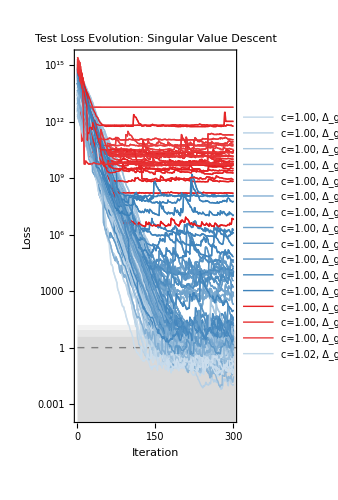

```mathematica
PlotLossVersusIterationOf["Test Loss Evolution: Singular Value Descent",ColorOf/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], RenameOf[MyCampaignResult[#],PrettyNameOf[#]]&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], PlotRange ->Automatic(*{{0,Automatic}, {10^-2, 10^17}}*)]
(*Export[MyCampaignPrefix<>"all_loss_vs_iter.pdf",%]*)

(* These are just for validation *)
(*PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: c=1.09 Candidate", {ColorForNaiveLoss,ColorForImprovedLoss},{MyCampaignGradResult[#],MyCampaignSVResult[#]},1.0]&[MyCampaignDefaultName]

PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: Singular Value Descent",ColorOf/@MyCampaignNames, RenameOf[MyCampaignSVResult[#],PrettyNameOf[#]]&/@MyCampaignNames,1]*)
```

### Computing Refined Losses

```mathematica
Monitor[{currentname = #;MyCampaignBestLossRefined[#]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
```

General::munfl: Exp[-813.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-323508.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-144077.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Plotting

General::munfl: Exp[-813.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-323508.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-144077.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

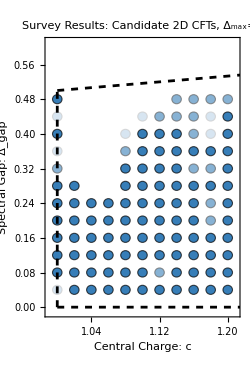

plots/survey_deltamax4_yes_candidate_cfts.pdf

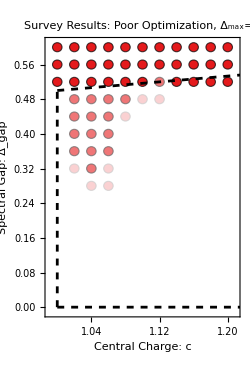

plots/survey_deltamax4_no_candidate_cfts.pdf

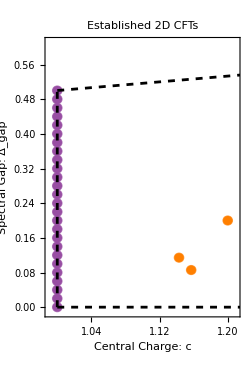

plots/summary_known_cfts.pdf

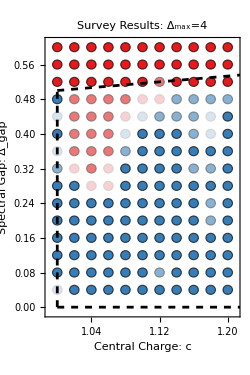

plots/summary_deltamax4_yesno_candidate_cfts.pdf

```mathematica
largeNumber = 10000;

DATA = Monitor[{CentralChargeOf[MyCampaignBestModel[#]],
Sort[DeltaOf/@PrimariesOf[MyCampaignBestModel[#]]][[2]],If[NumIterationsOf[MyCampaignResult[#]]>=MyNumEpochs || Log[10,MyCampaignBestLoss[#]] < lowYESthresh,currentname = #;Log[10,MyCampaignBestLossRefined[#]],largeNumber + NumIterationsOf[MyCampaignResult[#]]/MyNumEpochs]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
defaultsize = 1/16;
highYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(#[[3]]<=highYESthresh)&];
mediumYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(highYESthresh<#[[3]]<=mediumYESthresh)&];
lowYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(mediumYESthresh<#[[3]]<=lowYESthresh)&];
weakNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(lowYESthresh<#[[3]]<=weakNOthresh)&];
intermediateNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(weakNOthresh<#[[3]]<=intermediateNOthresh)&];
strongNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(intermediateNOthresh<#[[3]]<largeNumber)&];
UNKNOWN = {#[[1]],#[[2]],defaultsize/3}&/@Select[DATA,(largeNumber<= #[[3]])&];

N1MMexamples = {CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]], defaultsize}&/@{N1MM[5,MyMaxDelta],N1MM[6,MyMaxDelta],N1MM[7,MyMaxDelta],N1MM[8,MyMaxDelta]};

FBCBexamples = Join[{{1,0,defaultsize}},{CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]],defaultsize}&/@Table[FBCB[1/Sqrt[x],MyMaxDelta],{x,0.04,1,.04}]];

ADDexample = {(*Z5 parafermion*){8/7,4/35,defaultsize},(*Ising x tricritical Ising*){6/5,1/5,defaultsize},(*Z6 parafermion*){5/4,1/12,defaultsize}};
BOUNDS =  {{1, 0,1},{1.2,0.6,1}};

PLOT0 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[Lighter[ColorForPositiveValues,0],EdgeForm[GrayLevel[0]]],
Directive[Lighter[ColorForPositiveValues,0.4],EdgeForm[GrayLevel[0.4]]],Directive[Lighter[ColorForPositiveValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.4],EdgeForm[GrayLevel[0.4]]],
Directive[Lighter[ColorForNegativeValues,0.0],EdgeForm[GrayLevel[0.0]]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Survey Results: Δ_max=4"],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT1 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[Lighter[ColorForPositiveValues,0],EdgeForm[GrayLevel[0]]],
Directive[Lighter[ColorForPositiveValues,0.4],EdgeForm[GrayLevel[0.4]]],Directive[Lighter[ColorForPositiveValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Survey Results: Candidate 2D CFTs, Δ_max=4"],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT2 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[Lighter[ColorForNegativeValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.4],EdgeForm[GrayLevel[0.4]]],
Directive[Lighter[ColorForNegativeValues,0.0],EdgeForm[GrayLevel[0.0]]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Survey Results: Poor Optimization, Δ_max=4"],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT3 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
ColorForN1MM,
ColorForN1MM,
ColorForFBCB},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Established 2D CFTs"],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];

PLOT4= Plot[{c/6+1/3,0}, {c,1,10}, PlotStyle -> Directive[Black,Dashed]];
PLOT5= ParametricPlot[{1,d}, {d,0,0.5}, PlotStyle -> Directive[Black,Dashed]];


Show[PLOT1,PLOT4,PLOT5]
Export[PathForPlots<>"survey_deltamax4_yes_candidate_cfts.pdf",%]
Show[PLOT2,PLOT4,PLOT5]
Export[PathForPlots<>"survey_deltamax4_no_candidate_cfts.pdf",%]
Show[PLOT3,PLOT4,PLOT5]
Export[PathForPlots<>"summary_known_cfts.pdf",%]
Show[PLOT0,PLOT4,PLOT5]
Export[PathForPlots<>"summary_deltamax4_yesno_candidate_cfts.pdf",%]
```

6

(ⅇ^(-2^(-1+a) 5^a ν) (2^(-1+a) 5^a ν)^(ν/2) Log[10])/Gamma[ν/2]

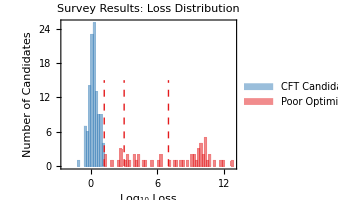

plots/survey_deltamax4_loss_distribution.pdf

```mathematica
nbin = 6
binwidth = Log[10,16]/nbin;
plot1 = Histogram[{
Select[DATA[[All,3]], (#<lowYESthresh)&],
Select[DATA[[All,3]], (lowYESthresh<=#<weakNOthresh)&],
Select[DATA[[All,3]], (weakNOthresh<=#<intermediateNOthresh)&],
Select[DATA[[All,3]], (intermediateNOthresh<=#)&]
}, 
{-binwidth* nbin*2,13,binwidth}, 
ChartStyle-> {ColorForPositiveValues,ColorForNegativeValues,ColorForNegativeValues,ColorForNegativeValues}, Evaluate[DefaultPlotOptions], AspectRatio-> 0.8,PlotRange -> {0,25},
PlotLabel->NiceTitle["Survey Results: Loss Distribution"], FrameLabel-> {"Log_10 Loss","Number of Candidates"},ChartLegends-> Placed[{"  CFT Candidates","  Poor Optimization"},{Scaled[{0.72,0.84}], {1, 1}}]];
plot2 = ParametricPlot[{(*{0,t},{Log[10,4],t}*),{lowYESthresh,t},{weakNOthresh,t},{intermediateNOthresh,t}}, {t,0,15}, PlotStyle-> Directive[Dashed, ColorForNegativeValues,Thickness[Medium]]];
D[GammaRegularized[ν/2,0,2^(-1+a) 5^a ν], a]//Simplify
plot3 =  Plot[{((ⅇ^(-2^(-1+a) 5^a ν) (2^(-1+a) 5^a ν)^(ν/2) Log[10])/Gamma[ν/2]/. ν -> 5)*Length[Select[DATA[[All,3]], (#<0)&]]/0.6083748237289106*binwidth}, {a,-10,Log[10,9]}, PlotRange -> {0,50}, PlotStyle -> {Directive[ColorForPositiveValues,Thickness[Large]]}, Evaluate[DefaultPlotOptions],PlotLegends-> Placed[{"χ_3^2/3 Expectation"},{Scaled[{0.93,0.96}], {1, 1}}]];
Show[plot1,plot2]
Export[PathForPlots<>"survey_deltamax4_loss_distribution.pdf",%]
```

### Highlighting Specific Models

```mathematica
MyCampaignBestPlot[MyCampaignPrefix<>"c108_dg32"]
Export[PathForPlots<>"survey_deltamax4_yes_high_example.pdf",%]
MyCampaignBestPlot[MyCampaignPrefix<>"c108_dg36"]
Export[PathForPlots<>"survey_deltamax4_yes_medium_example.pdf",%]
MyCampaignBestPlot[MyCampaignPrefix<>"c108_dg40"]
Export[PathForPlots<>"survey_deltamax4_yes_low_example.pdf",%]
MyCampaignBestPlot[MyCampaignPrefix<>"c108_dg44"]
Export[PathForPlots<>"survey_deltamax4_no_low_example.pdf",%]
MyCampaignBestPlot[MyCampaignPrefix<>"c108_dg48"]
Export[PathForPlots<>"survey_deltamax4_no_medium_example.pdf",%]
MyCampaignBestPlot[MyCampaignPrefix<>"c108_dg52"]
Export[PathForPlots<>"survey_deltamax4_no_high_example.pdf",%]
```

-Graphics-

plots/survey_deltamax4_yes_high_example.pdf

-Graphics-

plots/survey_deltamax4_yes_medium_example.pdf

-Graphics-

plots/survey_deltamax4_yes_low_example.pdf

-Graphics-

plots/survey_deltamax4_no_low_example.pdf

-Graphics-

plots/survey_deltamax4_no_medium_example.pdf

-Graphics-

plots/survey_deltamax4_no_high_example.pdf

### Plotting With Lower Cuts (Delta_max = 3)

General::munfl: Exp[-813.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-323508.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-144077.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

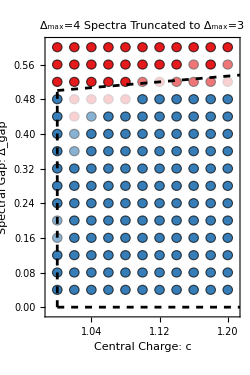

plots/survey_deltamax4_trunc3.pdf

```mathematica
highYESthresh = Log[10,4];
mediumYESthresh = Log[10,9];
lowYESthresh = Log[10,16];
weakNOthresh = Log[10,10^3];
intermediateNOthresh = Log[10,10^5];

largeNumber = 10000;
NewDeltaMax = 3;
DATA = Monitor[{CentralChargeOf[MyCampaignBestModel[#]],
Sort[DeltaOf/@PrimariesOf[MyCampaignBestModel[#]]][[2]],If[NumIterationsOf[MyCampaignResult[#]]>=MyNumEpochs || Log[10,MyCampaignBestLoss[#]] < lowYESthresh,currentname = #;Log[10,MyCampaignBestLossRefinedWithAltMax[#,NewDeltaMax]],largeNumber + NumIterationsOf[MyCampaignResult[#]]/MyNumEpochs]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
defaultsize = 1/16;
highYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(#[[3]]<=highYESthresh)&];
mediumYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(highYESthresh<#[[3]]<=mediumYESthresh)&];
lowYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(mediumYESthresh<#[[3]]<=lowYESthresh)&];
weakNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(lowYESthresh<#[[3]]<=weakNOthresh)&];
intermediateNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(weakNOthresh<#[[3]]<=intermediateNOthresh)&];
strongNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(intermediateNOthresh<#[[3]]<largeNumber)&];
UNKNOWN = {#[[1]],#[[2]],defaultsize/3}&/@Select[DATA,(largeNumber<= #[[3]])&];

N1MMexamples = {CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]], defaultsize}&/@{N1MM[5,MyMaxDelta],N1MM[6,MyMaxDelta],N1MM[7,MyMaxDelta],N1MM[8,MyMaxDelta]};

FBCBexamples = Join[{{1,0,defaultsize}},{CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]],defaultsize}&/@Table[FBCB[1/Sqrt[x],MyMaxDelta],{x,0.04,1,.04}]];

ADDexample = {(*Z5 parafermion*){8/7,4/35,defaultsize},(*Ising x tricritical Ising*){6/5,1/5,defaultsize},(*Z6 parafermion*){5/4,1/12,defaultsize}};
BOUNDS =  {{1, 0,1},{1.2,0.6,1}};

PLOT0 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[Lighter[ColorForPositiveValues,0],EdgeForm[GrayLevel[0]]],
Directive[Lighter[ColorForPositiveValues,0.4],EdgeForm[GrayLevel[0.4]]],Directive[Lighter[ColorForPositiveValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.4],EdgeForm[GrayLevel[0.4]]],
Directive[Lighter[ColorForNegativeValues,0.0],EdgeForm[GrayLevel[0.0]]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Δ_max=4 Spectra Truncated to Δ_max="<>ToString[NewDeltaMax]],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT4= Plot[{c/6+1/3,0}, {c,1,10}, PlotStyle -> Directive[Black,Dashed]];
PLOT5= ParametricPlot[{1,d}, {d,0,0.5}, PlotStyle -> Directive[Black,Dashed]];

Show[PLOT0,PLOT4,PLOT5]
Export[PathForPlots<>"survey_deltamax4_trunc3.pdf",%]
```

## For Paper: Optimization Campaign (Survey With Flexible Degeneracy)

## Setting Up Optimization Campaign

### Optimization Settings & Starting Models

```mathematica
(* Defaults have Tau2Max of 6*)
MyCampaignDeterministicTaus[_] := DefaultCoarseDeterministicTaus;
MyCampaignRefinedDeterministicTaus[_] := DefaultFineDeterministicTaus;
MyCampaignTauSamplerData[_] := DefaultLargeTauSampler;

(* These values will certainly need to be adjusted *)
MyNumEpochs = 300;
MyLearningRate = 0.1;
MyMaxSVRatio = 10^-12;

MyMaxDelta = 4;
MySpinValues = {0,1,2,3};
MyNumSpin[0] = 24;
MyNumSpin[1] = 18;
MyNumSpin[2] = 12;
MyNumSpin[3] = 6;

Clear[MyPrimaries]
MyPrimaries[pseudogap_] := Flatten[
{{DSD[0, 0,1]},{DSD[pseudogap, 0,1]},
Table[Table[
DSD[SigmoidEsque[FlexDelta[s,i],Max[s,pseudogap],2*MyMaxDelta - Max[s,pseudogap]], 
s,
SigmoidEsque[FlexDegen[s,i],0,2]],
 {i,1,MyNumSpin[s]}], {s,MySpinValues }]
}];
MyVariables = Flatten[Table[Table[{FlexDelta[s,i],FlexDegen[s,i]}, {i,1,MyNumSpin[s]}], {s,MySpinValues }]];
MyInitialValues = Flatten[Table[Table[{Log[(i/(MyNumSpin[s]+1))/(2-i/(MyNumSpin[s]+1))],0}, {i,1,MyNumSpin[s]}], {s,MySpinValues }]];

MyCampaignPrefix = "survey_max4_sv16_degflex_";
MyCampaignSingularValue = 16;
MyRValue = Sqrt[2];
MyCampaignCentralCharges =Table[i,{i,1.0,1.10,0.02}] ;
MyCampaignDeltaGaps =  Table[i,{i,0.24,0.56,0.04}] ;

(* Things that have to be defined model specifically *)
MyCampaignNames = {};
For[cc = 1, cc <= Length[MyCampaignCentralCharges], cc++,
For[dg = 1, dg <= Length[MyCampaignDeltaGaps], dg++,
ThisCC = MyCampaignCentralCharges[[cc]];
ThisDG = MyCampaignDeltaGaps[[dg]];
MyLongName = MyCampaignPrefix <>"c"<>ToString[Round[ThisCC*100]]<>"_dg"<>ToString[Round[ThisDG*100]];
AppendTo[MyCampaignNames, MyLongName];
PrettyNameOf[MyLongName] = "c="<>ToString[SetAccuracy[ThisCC,3]]<>", Δ_gap="<>ToString[SetAccuracy[ThisDG,3]];
ColorOf[MyLongName] = If[ThisCC/6+1/3>ThisDG,Lighter[ColorForPositiveValues,1.5*(ThisCC/6+1/3-ThisDG)],Lighter[ColorForNegativeValues,-1.5*(ThisCC/6+1/3-ThisDG)]];
MyCampaignPrimaries[MyLongName] = MyPrimaries[ThisDG];
MyCampaignFlexibleModel[MyLongName] = CFTData[MyLongName,ThisCC,MyCampaignPrimaries[MyLongName], MyMaxDelta, MyVariables];
MyCampaignReferenceModel[MyLongName] = DefaultReferenceModelFor[MyCampaignFlexibleModel[MyLongName]];
MyCampaignStartingReplacement[MyLongName] = ReplacementData[MyVariables,MyInitialValues,{}];

MyCampaignAlgorithmDetails[MyLongName] = If[MyCampaignSingularValue==0,GradientDescentData[], SingularValueDescentData[MyCampaignSingularValue,MyMaxSVRatio]];
MyCampaignAlgorithm[MyLongName] =AlgorithmData[MyNumEpochs,MyLearningRate,MyCampaignAlgorithmDetails[MyLongName]];
]
]

highYESthresh = Log[10,4];
mediumYESthresh = Log[10,9];
lowYESthresh = Log[10,16];
weakNOthresh = Log[10,10^3];
intermediateNOthresh = Log[10,10^7];
LossColorOf[loss_]:= Which[
Log[10,loss] < highYESthresh, Lighter[ColorForPositiveValues,0],
Log[10,loss] < mediumYESthresh, Lighter[ColorForPositiveValues,0.4],
Log[10,loss] < lowYESthresh,Lighter[ColorForPositiveValues,0.8],
Log[10,loss] < weakNOthresh,Lighter[ColorForNegativeValues,0.8],
Log[10,loss] < intermediateNOthresh,Lighter[ColorForNegativeValues,0.4],
True,Lighter[ColorForNegativeValues,0]
]


(* Outputting names to make sure they look right*)
MyCampaignNames
ColorOf/@MyCampaignNames
MyCampaignDefaultName= MyCampaignNames[[1]]
```

{survey_max4_sv16_degflex_c100_dg24,survey_max4_sv16_degflex_c100_dg28,survey_max4_sv16_degflex_c100_dg32,survey_max4_sv16_degflex_c100_dg36,survey_max4_sv16_degflex_c100_dg40,survey_max4_sv16_degflex_c100_dg44,survey_max4_sv16_degflex_c100_dg48,survey_max4_sv16_degflex_c100_dg52,survey_max4_sv16_degflex_c100_dg56,survey_max4_sv16_degflex_c102_dg24,survey_max4_sv16_degflex_c102_dg28,survey_max4_sv16_degflex_c102_dg32,survey_max4_sv16_degflex_c102_dg36,survey_max4_sv16_degflex_c102_dg40,survey_max4_sv16_degflex_c102_dg44,survey_max4_sv16_degflex_c102_dg48,survey_max4_sv16_degflex_c102_dg52,survey_max4_sv16_degflex_c102_dg56,survey_max4_sv16_degflex_c104_dg24,survey_max4_sv16_degflex_c104_dg28,survey_max4_sv16_degflex_c104_dg32,survey_max4_sv16_degflex_c104_dg36,survey_max4_sv16_degflex_c104_dg40,survey_max4_sv16_degflex_c104_dg44,survey_max4_sv16_degflex_c104_dg48,survey_max4_sv16_degflex_c104_dg52,survey_max4_sv16_degflex_c104_dg56,survey_max4_sv16_degflex_c106_dg24,survey_max4_sv16_degflex_c106_dg28,survey_max4_sv16_degflex_c106_dg32,survey_max4_sv16_degflex_c106_dg36,survey_max4_sv16_degflex_c106_dg40,survey_max4_sv16_degflex_c106_dg44,survey_max4_sv16_degflex_c106_dg48,survey_max4_sv16_degflex_c106_dg52,survey_max4_sv16_degflex_c106_dg56,survey_max4_sv16_degflex_c108_dg24,survey_max4_sv16_degflex_c108_dg28,survey_max4_sv16_degflex_c108_dg32,survey_max4_sv16_degflex_c108_dg36,survey_max4_sv16_degflex_c108_dg40,survey_max4_sv16_degflex_c108_dg44,survey_max4_sv16_degflex_c108_dg48,survey_max4_sv16_degflex_c108_dg52,survey_max4_sv16_degflex_c108_dg56,survey_max4_sv16_degflex_c110_dg24,survey_max4_sv16_degflex_c110_dg28,survey_max4_sv16_degflex_c110_dg32,survey_max4_sv16_degflex_c110_dg36,survey_max4_sv16_degflex_c110_dg40,survey_max4_sv16_degflex_c110_dg44,survey_max4_sv16_degflex_c110_dg48,survey_max4_sv16_degflex_c110_dg52,survey_max4_sv16_degflex_c110_dg56}

{RGBColor[0.5215686274509804, 0.6914117647058824, 0.830156862745098],RGBColor[0.4745098039215687, 0.6610588235294118, 0.8134509803921569],RGBColor[0.4274509803921569, 0.6307058823529412, 0.7967450980392157],RGBColor[0.38039215686274513, 0.6003529411764706, 0.7800392156862745],RGBColor[0.3333333333333333, 0.57, 0.7633333333333333],RGBColor[0.28627450980392155, 0.5396470588235295, 0.7466274509803922],RGBColor[0.23921568627450984, 0.5092941176470589, 0.729921568627451],RGBColor[0.8972941176470588, 0.12890196078431376, 0.13650980392156864],RGBColor[0.9036470588235294, 0.18278431372549028, 0.18992156862745105],RGBColor[0.5254901960784314, 0.6939411764705883, 0.8315490196078431],RGBColor[0.4784313725490196, 0.6635882352941176, 0.814843137254902],RGBColor[0.43137254901960775, 0.633235294117647, 0.7981372549019607],RGBColor[0.38431372549019605, 0.6028823529411764, 0.7814313725490196],RGBColor[0.3372549019607843, 0.5725294117647058, 0.7647254901960784],RGBColor[0.2901960784313725, 0.5421764705882353, 0.7480196078431373],RGBColor[0.24313725490196078, 0.5118235294117647, 0.731313725490196],RGBColor[0.8967647058823529, 0.12441176470588242, 0.13205882352941184],RGBColor[0.9031176470588235, 0.17829411764705894, 0.18547058823529422],RGBColor[0.5294117647058822, 0.6964705882352941, 0.8329411764705882],RGBColor[0.4823529411764706, 0.6661176470588235, 0.8162352941176471],RGBColor[0.4352941176470588, 0.6357647058823529, 0.7995294117647058],RGBColor[0.388235294117647, 0.6054117647058823, 0.7828235294117647],RGBColor[0.3411764705882352, 0.5750588235294117, 0.7661176470588235],RGBColor[0.2941176470588235, 0.5447058823529412, 0.7494117647058823],RGBColor[0.24705882352941172, 0.5143529411764706, 0.7327058823529411],RGBColor[0.896235294117647, 0.1199215686274511, 0.127607843137255],RGBColor[0.9025882352941176, 0.17380392156862762, 0.18101960784313742],RGBColor[0.5333333333333333, 0.6990000000000001, 0.8343333333333334],RGBColor[0.4862745098039216, 0.6686470588235295, 0.8176274509803921],RGBColor[0.43921568627450985, 0.6382941176470589, 0.800921568627451],RGBColor[0.3921568627450981, 0.6079411764705883, 0.7842156862745098],RGBColor[0.34509803921568627, 0.5775882352941176, 0.7675098039215686],RGBColor[0.2980392156862745, 0.547235294117647, 0.7508039215686274],RGBColor[0.2509803921568628, 0.5168823529411765, 0.7340980392156863],RGBColor[0.8957058823529411, 0.11543137254901963, 0.12315686274509804],RGBColor[0.9020588235294117, 0.16931372549019613, 0.17656862745098045],RGBColor[0.5372549019607843, 0.7015294117647058, 0.8357254901960784],RGBColor[0.49019607843137253, 0.6711764705882353, 0.8190196078431372],RGBColor[0.4431372549019607, 0.6408235294117647, 0.8023137254901961],RGBColor[0.396078431372549, 0.6104705882352941, 0.7856078431372548],RGBColor[0.3490196078431372, 0.5801176470588235, 0.7689019607843137],RGBColor[0.30196078431372547, 0.5497647058823529, 0.7521960784313725],RGBColor[0.2549019607843137, 0.5194117647058824, 0.7354901960784314],RGBColor[0.8951764705882352, 0.11094117647058829, 0.11870588235294123],RGBColor[0.9015294117647058, 0.1648235294117648, 0.17211764705882363],RGBColor[0.5411764705882353, 0.7040588235294117, 0.8371176470588235],RGBColor[0.4941176470588235, 0.6737058823529412, 0.8204117647058824],RGBColor[0.44705882352941173, 0.6433529411764706, 0.8037058823529412],RGBColor[0.39999999999999997, 0.613, 0.7869999999999999],RGBColor[0.35294117647058815, 0.5826470588235294, 0.7702941176470588],RGBColor[0.3058823529411764, 0.5522941176470588, 0.7535882352941176],RGBColor[0.2588235294117647, 0.5219411764705882, 0.7368823529411764],RGBColor[0.8946470588235294, 0.10645098039215696, 0.11425490196078442],RGBColor[0.9009999999999999, 0.1603333333333335, 0.16766666666666682]}

survey_max4_sv16_degflex_c100_dg24

### Plotting Starting Model

```mathematica
Validate[MyCampaignStartingModel[#]]&/@MyCampaignNames
(*MyCampaignStartingLoss/@ MyCampaignNames*)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Checking For Existing Files

```mathematica
{Unset[MyCampaignResult[#]];#,FileExistsQ[MyCampaignFilename[#]], NumIterationsOf[MyCampaignResult[#]]}&/@MyCampaignNames
```

{{survey_max4_sv16_degflex_c100_dg24,True,301},{survey_max4_sv16_degflex_c100_dg28,True,301},{survey_max4_sv16_degflex_c100_dg32,True,301},{survey_max4_sv16_degflex_c100_dg36,True,301},{survey_max4_sv16_degflex_c100_dg40,True,301},{survey_max4_sv16_degflex_c100_dg44,True,301},{survey_max4_sv16_degflex_c100_dg48,True,301},{survey_max4_sv16_degflex_c100_dg52,True,301},{survey_max4_sv16_degflex_c100_dg56,True,301},{survey_max4_sv16_degflex_c102_dg24,True,301},{survey_max4_sv16_degflex_c102_dg28,True,301},{survey_max4_sv16_degflex_c102_dg32,True,301},{survey_max4_sv16_degflex_c102_dg36,True,301},{survey_max4_sv16_degflex_c102_dg40,True,301},{survey_max4_sv16_degflex_c102_dg44,True,301},{survey_max4_sv16_degflex_c102_dg48,True,301},{survey_max4_sv16_degflex_c102_dg52,True,301},{survey_max4_sv16_degflex_c102_dg56,True,301},{survey_max4_sv16_degflex_c104_dg24,True,301},{survey_max4_sv16_degflex_c104_dg28,True,301},{survey_max4_sv16_degflex_c104_dg32,True,301},{survey_max4_sv16_degflex_c104_dg36,True,301},{survey_max4_sv16_degflex_c104_dg40,True,301},{survey_max4_sv16_degflex_c104_dg44,True,301},{survey_max4_sv16_degflex_c104_dg48,True,301},{survey_max4_sv16_degflex_c104_dg52,True,301},{survey_max4_sv16_degflex_c104_dg56,True,301},{survey_max4_sv16_degflex_c106_dg24,True,301},{survey_max4_sv16_degflex_c106_dg28,True,301},{survey_max4_sv16_degflex_c106_dg32,True,301},{survey_max4_sv16_degflex_c106_dg36,True,301},{survey_max4_sv16_degflex_c106_dg40,True,301},{survey_max4_sv16_degflex_c106_dg44,True,301},{survey_max4_sv16_degflex_c106_dg48,True,301},{survey_max4_sv16_degflex_c106_dg52,True,301},{survey_max4_sv16_degflex_c106_dg56,True,301},{survey_max4_sv16_degflex_c108_dg24,True,301},{survey_max4_sv16_degflex_c108_dg28,True,301},{survey_max4_sv16_degflex_c108_dg32,True,301},{survey_max4_sv16_degflex_c108_dg36,True,301},{survey_max4_sv16_degflex_c108_dg40,True,301},{survey_max4_sv16_degflex_c108_dg44,True,301},{survey_max4_sv16_degflex_c108_dg48,True,301},{survey_max4_sv16_degflex_c108_dg52,True,301},{survey_max4_sv16_degflex_c108_dg56,True,301},{survey_max4_sv16_degflex_c110_dg24,True,301},{survey_max4_sv16_degflex_c110_dg28,True,301},{survey_max4_sv16_degflex_c110_dg32,True,301},{survey_max4_sv16_degflex_c110_dg36,True,301},{survey_max4_sv16_degflex_c110_dg40,True,301},{survey_max4_sv16_degflex_c110_dg44,True,301},{survey_max4_sv16_degflex_c110_dg48,True,301},{survey_max4_sv16_degflex_c110_dg52,True,301},{survey_max4_sv16_degflex_c110_dg56,True,301}}

## Running Optimization (Will pick up from where it left off if file present)

### Running Optimization

```mathematica
MyRemainingNames = Select[MyCampaignNames,(Not[FileExistsQ[MyCampaignFilename[#]]]||NumIterationsOf[MyCampaignResult[#]]<MyNumEpochs)&];
(*The core optimization is here!*)
ParallelTable[
RunOptimizationFor[MyRemainingNames[[i]]];
,{i,1,Length[MyRemainingNames]}
]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of A front end is not available; certain operations require a front end. will be suppressed during this calculation.

General::munfl: 6.96 3.0421840267×10^-2640 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.96 4.10884750659×10^-2628 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1075.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,1.31211×10^10,1.48357×10^10}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,1.14691×10^9,1.29105×10^9}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,13.3242,13.2261}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,2.47558,4.86091}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,15.5272,6.77937}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,1.7976,0.223873}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,3.39464,1.57608}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.0954327,0.0201746}

{AlgorithmData[300,0.1,SingularValueDescentData[16,1/1000000000000]],301,0.305292,0.00841585}

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Analysis of Results

### Loss Function Evolution

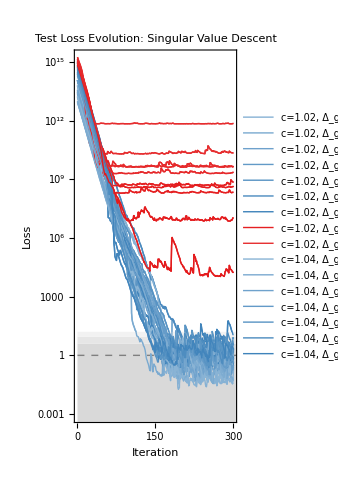

```mathematica
PlotLossVersusIterationOf["Test Loss Evolution: Singular Value Descent",ColorOf/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], RenameOf[MyCampaignResult[#],PrettyNameOf[#]]&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], PlotRange ->Automatic(*{{0,Automatic}, {10^-2, 10^17}}*)]
(*Export[MyCampaignPrefix<>"all_loss_vs_iter.pdf",%]*)

(* These are just for validation *)
(*PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: c=1.09 Candidate", {ColorForNaiveLoss,ColorForImprovedLoss},{MyCampaignGradResult[#],MyCampaignSVResult[#]},1.0]&[MyCampaignDefaultName]

PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: Singular Value Descent",ColorOf/@MyCampaignNames, RenameOf[MyCampaignSVResult[#],PrettyNameOf[#]]&/@MyCampaignNames,1]*)
```

### Computing Refined Losses

```mathematica
Monitor[{currentname = #;MyCampaignBestLossRefined[#]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
```

General::munfl: Exp[-1141.65] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1397.26] is too small to represent as a normalized machine number; precision may be lost.

### Plotting

```mathematica
largeNumber = 10000;

DATA = Monitor[{CentralChargeOf[MyCampaignBestModel[#]],
Sort[DeltaOf/@PrimariesOf[MyCampaignBestModel[#]]][[2]],If[NumIterationsOf[MyCampaignResult[#]]>=MyNumEpochs || Log[10,MyCampaignBestLoss[#]] < lowYESthresh,currentname = #;Log[10,MyCampaignBestLossRefined[#]],largeNumber + NumIterationsOf[MyCampaignResult[#]]/MyNumEpochs]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
defaultsize = 1/16;
highYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(#[[3]]<=highYESthresh)&];
mediumYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(highYESthresh<#[[3]]<=mediumYESthresh)&];
lowYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(mediumYESthresh<#[[3]]<=lowYESthresh)&];
weakNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(lowYESthresh<#[[3]]<=weakNOthresh)&];
intermediateNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(weakNOthresh<#[[3]]<=intermediateNOthresh)&];
strongNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(intermediateNOthresh<#[[3]]<largeNumber)&];
UNKNOWN = {#[[1]],#[[2]],defaultsize/3}&/@Select[DATA,(largeNumber<= #[[3]])&];

N1MMexamples = {CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]], defaultsize}&/@{N1MM[5,MyMaxDelta],N1MM[6,MyMaxDelta],N1MM[7,MyMaxDelta],N1MM[8,MyMaxDelta]};

FBCBexamples = Join[{{1,0,defaultsize}},{CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]],defaultsize}&/@Table[FBCB[1/Sqrt[x],MyMaxDelta],{x,0.04,1,.04}]];

ADDexample = {(*Z5 parafermion*){8/7,4/35,defaultsize},(*Ising x tricritical Ising*){6/5,1/5,defaultsize},(*Z6 parafermion*){5/4,1/12,defaultsize}};
BOUNDS =  {{1, 0,1},{1.2,0.6,1}};

PLOT0 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[Lighter[ColorForPositiveValues,0],EdgeForm[GrayLevel[0]]],
Directive[Lighter[ColorForPositiveValues,0.4],EdgeForm[GrayLevel[0.4]]],Directive[Lighter[ColorForPositiveValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.4],EdgeForm[GrayLevel[0.4]]],
Directive[Lighter[ColorForNegativeValues,0.0],EdgeForm[GrayLevel[0.0]]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Non-Integer Degeneracy, Δ_max=4"],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT4= Plot[{c/6+1/3,0}, {c,1,10}, PlotStyle -> Directive[Black,Dashed]];
PLOT5= ParametricPlot[{1,d}, {d,0,0.5}, PlotStyle -> Directive[Black,Dashed]];

Show[PLOT0,PLOT4,PLOT5]
Export[PathForPlots<>"survey_deltamax4_flexdegen.pdf",%]
```

General::munfl: Exp[-1141.65] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1397.26] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1141.65] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

plots/survey_deltamax_4_flexdegen.pdf

### Stats

(ⅇ^(-2^(-1+a) 5^a ν) (2^(-1+a) 5^a ν)^(ν/2) Log[10])/Gamma[ν/2]

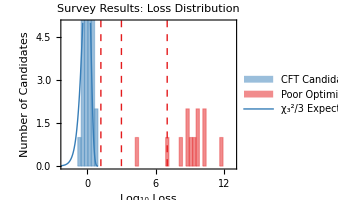

```mathematica
binwidth = (Log[9]+2 Log[10])/(n Log[10])/. n-> 10;
plot1 = Histogram[{
Select[DATA[[All,3]], (#<lowYESthresh)&],
Select[DATA[[All,3]], (lowYESthresh<=#<weakNOthresh)&],
Select[DATA[[All,3]], (weakNOthresh<=#<intermediateNOthresh)&],
Select[DATA[[All,3]], (intermediateNOthresh<=#)&]
}, 
{-2,13,binwidth}, 
ChartStyle-> {ColorForPositiveValues,ColorForNegativeValues,ColorForNegativeValues,ColorForNegativeValues}, Evaluate[DefaultPlotOptions], AspectRatio-> 0.8,PlotRange -> {0,5},
PlotLabel->NiceTitle["Survey Results: Loss Distribution"], FrameLabel-> {"Log_10 Loss","Number of Candidates"},ChartLegends-> Placed[{"  CFT Candidates","  Poor Optimization"},{Scaled[{0.72,0.74}], {1, 1}}]];
plot2 = ParametricPlot[{(*{0,t},{Log[10,4],t}*),{lowYESthresh,t},{weakNOthresh,t},{intermediateNOthresh,t}}, {t,0,17}, PlotStyle-> Directive[Dashed, ColorForNegativeValues,Thickness[Medium]]];
D[GammaRegularized[ν/2,0,2^(-1+a) 5^a ν], a]//Simplify
plot3 =  Plot[{((ⅇ^(-2^(-1+a) 5^a ν) (2^(-1+a) 5^a ν)^(ν/2) Log[10])/Gamma[ν/2]/. ν -> 3)*Length[Select[DATA[[All,3]], (#<0)&]]/0.6083748237289106*binwidth}, {a,-10,Log[10,9]}, PlotRange -> {0,5}, PlotStyle -> {Directive[ColorForPositiveValues,Thickness[Large]]}, Evaluate[DefaultPlotOptions],PlotLegends-> Placed[{"χ_3^2/3 Expectation"},{Scaled[{0.93,0.96}], {1, 1}}]];
Show[plot1,plot2,plot3]
```

## For Paper: Optimization Campaign (Survey With DeltaMax = 3)

## Setting Up Optimization Campaign

### Optimization Settings & Starting Models

```mathematica
MyMaxDelta = 3;

(* Defaults have Tau2Max of 6*)
MyCampaignDeterministicTaus[_] := DefaultCoarseDeterministicTausFor[MyMaxDelta];
MyCampaignRefinedDeterministicTaus[_] := DefaultFineDeterministicTausFor[MyMaxDelta];
MyCampaignTauSamplerData[_] := TauSamplerData[24,MyMaxDelta+2]

(* These values will certainly need to be adjusted *)
MyNumEpochs = 300;
MyLearningRate = 0.1;
MyMaxSVRatio = 10^-12;

MySpinValues = {0,1,2};
MyNumSpin[0] = 18;
MyNumSpin[1] = 12;
MyNumSpin[2] = 6;

Clear[MyPrimaries]
MyPrimaries[pseudogap_] := Flatten[
{{DSD[0, 0,1]},{DSD[pseudogap, 0,1]},
Table[Table[
DSD[SigmoidEsque[FlexDelta[s,i],Max[s,pseudogap],2*MyMaxDelta - Max[s,pseudogap]], 
s,
1],
 {i,1,MyNumSpin[s]}], {s,MySpinValues }]
}];
MyVariables = Flatten[Table[Table[FlexDelta[s,i], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];
MyInitialValues = Flatten[Table[Table[Log[(i/(MyNumSpin[s]+1))/(2-i/(MyNumSpin[s]+1))], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];

MyCampaignPrefix = "survey_max3_sv12_";
MyCampaignSingularValue = 12;
MyRValue = Sqrt[2];
MyCampaignCentralCharges =Table[i,{i,1.0,1.10,0.02}] ;
MyCampaignDeltaGaps =  Table[i,{i,0.24,0.56,0.04}] ;

(* Things that have to be defined model specifically *)
MyCampaignNames = {};
For[cc = 1, cc <= Length[MyCampaignCentralCharges], cc++,
For[dg = 1, dg <= Length[MyCampaignDeltaGaps], dg++,
ThisCC = MyCampaignCentralCharges[[cc]];
ThisDG = MyCampaignDeltaGaps[[dg]];
MyLongName = MyCampaignPrefix <>"c"<>ToString[Round[ThisCC*100]]<>"_dg"<>ToString[Round[ThisDG*100]];
AppendTo[MyCampaignNames, MyLongName];
PrettyNameOf[MyLongName] = "c="<>ToString[SetAccuracy[ThisCC,3]]<>", Δ_gap="<>ToString[SetAccuracy[ThisDG,3]];
ColorOf[MyLongName] = If[ThisCC/6+1/3>ThisDG,Lighter[ColorForPositiveValues,1.5*(ThisCC/6+1/3-ThisDG)],Lighter[ColorForNegativeValues,-1.5*(ThisCC/6+1/3-ThisDG)]];
MyCampaignPrimaries[MyLongName] = MyPrimaries[ThisDG];
MyCampaignFlexibleModel[MyLongName] = CFTData[MyLongName,ThisCC,MyCampaignPrimaries[MyLongName], MyMaxDelta, MyVariables];
MyCampaignReferenceModel[MyLongName] = DefaultReferenceModelFor[MyCampaignFlexibleModel[MyLongName]];
MyCampaignStartingReplacement[MyLongName] = ReplacementData[MyVariables,MyInitialValues,{}];

MyCampaignAlgorithmDetails[MyLongName] = If[MyCampaignSingularValue==0,GradientDescentData[], SingularValueDescentData[MyCampaignSingularValue,MyMaxSVRatio]];
MyCampaignAlgorithm[MyLongName] =AlgorithmData[MyNumEpochs,MyLearningRate,MyCampaignAlgorithmDetails[MyLongName]];
]
]

highYESthresh = Log[10,4];
mediumYESthresh = Log[10,9];
lowYESthresh = Log[10,16];
weakNOthresh = Log[10,10^3];
intermediateNOthresh = Log[10,10^5];
LossColorOf[loss_]:= Which[
Log[10,loss] < highYESthresh, Lighter[ColorForPositiveValues,0],
Log[10,loss] < mediumYESthresh, Lighter[ColorForPositiveValues,0.4],
Log[10,loss] < lowYESthresh,Lighter[ColorForPositiveValues,0.8],
Log[10,loss] < weakNOthresh,Lighter[ColorForNegativeValues,0.8],
Log[10,loss] < intermediateNOthresh,Lighter[ColorForNegativeValues,0.4],
True,Lighter[ColorForNegativeValues,0]
]


(* Outputting names to make sure they look right*)
MyCampaignNames
ColorOf/@MyCampaignNames
MyCampaignDefaultName= MyCampaignNames[[1]]
```

{survey_max3_sv12_c100_dg24,survey_max3_sv12_c100_dg28,survey_max3_sv12_c100_dg32,survey_max3_sv12_c100_dg36,survey_max3_sv12_c100_dg40,survey_max3_sv12_c100_dg44,survey_max3_sv12_c100_dg48,survey_max3_sv12_c100_dg52,survey_max3_sv12_c100_dg56,survey_max3_sv12_c102_dg24,survey_max3_sv12_c102_dg28,survey_max3_sv12_c102_dg32,survey_max3_sv12_c102_dg36,survey_max3_sv12_c102_dg40,survey_max3_sv12_c102_dg44,survey_max3_sv12_c102_dg48,survey_max3_sv12_c102_dg52,survey_max3_sv12_c102_dg56,survey_max3_sv12_c104_dg24,survey_max3_sv12_c104_dg28,survey_max3_sv12_c104_dg32,survey_max3_sv12_c104_dg36,survey_max3_sv12_c104_dg40,survey_max3_sv12_c104_dg44,survey_max3_sv12_c104_dg48,survey_max3_sv12_c104_dg52,survey_max3_sv12_c104_dg56,survey_max3_sv12_c106_dg24,survey_max3_sv12_c106_dg28,survey_max3_sv12_c106_dg32,survey_max3_sv12_c106_dg36,survey_max3_sv12_c106_dg40,survey_max3_sv12_c106_dg44,survey_max3_sv12_c106_dg48,survey_max3_sv12_c106_dg52,survey_max3_sv12_c106_dg56,survey_max3_sv12_c108_dg24,survey_max3_sv12_c108_dg28,survey_max3_sv12_c108_dg32,survey_max3_sv12_c108_dg36,survey_max3_sv12_c108_dg40,survey_max3_sv12_c108_dg44,survey_max3_sv12_c108_dg48,survey_max3_sv12_c108_dg52,survey_max3_sv12_c108_dg56,survey_max3_sv12_c110_dg24,survey_max3_sv12_c110_dg28,survey_max3_sv12_c110_dg32,survey_max3_sv12_c110_dg36,survey_max3_sv12_c110_dg40,survey_max3_sv12_c110_dg44,survey_max3_sv12_c110_dg48,survey_max3_sv12_c110_dg52,survey_max3_sv12_c110_dg56}

{RGBColor[0.5215686274509804, 0.6914117647058824, 0.830156862745098],RGBColor[0.4745098039215687, 0.6610588235294118, 0.8134509803921569],RGBColor[0.4274509803921569, 0.6307058823529412, 0.7967450980392157],RGBColor[0.38039215686274513, 0.6003529411764706, 0.7800392156862745],RGBColor[0.3333333333333333, 0.57, 0.7633333333333333],RGBColor[0.28627450980392155, 0.5396470588235295, 0.7466274509803922],RGBColor[0.23921568627450984, 0.5092941176470589, 0.729921568627451],RGBColor[0.8972941176470588, 0.12890196078431376, 0.13650980392156864],RGBColor[0.9036470588235294, 0.18278431372549028, 0.18992156862745105],RGBColor[0.5254901960784314, 0.6939411764705883, 0.8315490196078431],RGBColor[0.4784313725490196, 0.6635882352941176, 0.814843137254902],RGBColor[0.43137254901960775, 0.633235294117647, 0.7981372549019607],RGBColor[0.38431372549019605, 0.6028823529411764, 0.7814313725490196],RGBColor[0.3372549019607843, 0.5725294117647058, 0.7647254901960784],RGBColor[0.2901960784313725, 0.5421764705882353, 0.7480196078431373],RGBColor[0.24313725490196078, 0.5118235294117647, 0.731313725490196],RGBColor[0.8967647058823529, 0.12441176470588242, 0.13205882352941184],RGBColor[0.9031176470588235, 0.17829411764705894, 0.18547058823529422],RGBColor[0.5294117647058822, 0.6964705882352941, 0.8329411764705882],RGBColor[0.4823529411764706, 0.6661176470588235, 0.8162352941176471],RGBColor[0.4352941176470588, 0.6357647058823529, 0.7995294117647058],RGBColor[0.388235294117647, 0.6054117647058823, 0.7828235294117647],RGBColor[0.3411764705882352, 0.5750588235294117, 0.7661176470588235],RGBColor[0.2941176470588235, 0.5447058823529412, 0.7494117647058823],RGBColor[0.24705882352941172, 0.5143529411764706, 0.7327058823529411],RGBColor[0.896235294117647, 0.1199215686274511, 0.127607843137255],RGBColor[0.9025882352941176, 0.17380392156862762, 0.18101960784313742],RGBColor[0.5333333333333333, 0.6990000000000001, 0.8343333333333334],RGBColor[0.4862745098039216, 0.6686470588235295, 0.8176274509803921],RGBColor[0.43921568627450985, 0.6382941176470589, 0.800921568627451],RGBColor[0.3921568627450981, 0.6079411764705883, 0.7842156862745098],RGBColor[0.34509803921568627, 0.5775882352941176, 0.7675098039215686],RGBColor[0.2980392156862745, 0.547235294117647, 0.7508039215686274],RGBColor[0.2509803921568628, 0.5168823529411765, 0.7340980392156863],RGBColor[0.8957058823529411, 0.11543137254901963, 0.12315686274509804],RGBColor[0.9020588235294117, 0.16931372549019613, 0.17656862745098045],RGBColor[0.5372549019607843, 0.7015294117647058, 0.8357254901960784],RGBColor[0.49019607843137253, 0.6711764705882353, 0.8190196078431372],RGBColor[0.4431372549019607, 0.6408235294117647, 0.8023137254901961],RGBColor[0.396078431372549, 0.6104705882352941, 0.7856078431372548],RGBColor[0.3490196078431372, 0.5801176470588235, 0.7689019607843137],RGBColor[0.30196078431372547, 0.5497647058823529, 0.7521960784313725],RGBColor[0.2549019607843137, 0.5194117647058824, 0.7354901960784314],RGBColor[0.8951764705882352, 0.11094117647058829, 0.11870588235294123],RGBColor[0.9015294117647058, 0.1648235294117648, 0.17211764705882363],RGBColor[0.5411764705882353, 0.7040588235294117, 0.8371176470588235],RGBColor[0.4941176470588235, 0.6737058823529412, 0.8204117647058824],RGBColor[0.44705882352941173, 0.6433529411764706, 0.8037058823529412],RGBColor[0.39999999999999997, 0.613, 0.7869999999999999],RGBColor[0.35294117647058815, 0.5826470588235294, 0.7702941176470588],RGBColor[0.3058823529411764, 0.5522941176470588, 0.7535882352941176],RGBColor[0.2588235294117647, 0.5219411764705882, 0.7368823529411764],RGBColor[0.8946470588235294, 0.10645098039215696, 0.11425490196078442],RGBColor[0.9009999999999999, 0.1603333333333335, 0.16766666666666682]}

survey_max3_sv12_c100_dg24

### Plotting Starting Model

```mathematica
Validate[MyCampaignStartingModel[#]]&/@MyCampaignNames
(*MyCampaignStartingLoss/@ MyCampaignNames*)

MyCampaignStartingPlot[MyCampaignDefaultName]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

-Graphics-

### Checking For Existing Files

```mathematica
{Unset[MyCampaignResult[#]];#,FileExistsQ[MyCampaignFilename[#]], NumIterationsOf[MyCampaignResult[#]]}&/@MyCampaignNames
```

{{survey_max3_sv12_c100_dg24,True,301},{survey_max3_sv12_c100_dg28,True,301},{survey_max3_sv12_c100_dg32,True,301},{survey_max3_sv12_c100_dg36,True,301},{survey_max3_sv12_c100_dg40,True,301},{survey_max3_sv12_c100_dg44,True,301},{survey_max3_sv12_c100_dg48,True,301},{survey_max3_sv12_c100_dg52,True,301},{survey_max3_sv12_c100_dg56,True,301},{survey_max3_sv12_c102_dg24,True,301},{survey_max3_sv12_c102_dg28,True,301},{survey_max3_sv12_c102_dg32,True,301},{survey_max3_sv12_c102_dg36,True,301},{survey_max3_sv12_c102_dg40,True,301},{survey_max3_sv12_c102_dg44,True,301},{survey_max3_sv12_c102_dg48,True,301},{survey_max3_sv12_c102_dg52,True,301},{survey_max3_sv12_c102_dg56,True,301},{survey_max3_sv12_c104_dg24,True,301},{survey_max3_sv12_c104_dg28,True,301},{survey_max3_sv12_c104_dg32,True,301},{survey_max3_sv12_c104_dg36,True,301},{survey_max3_sv12_c104_dg40,True,301},{survey_max3_sv12_c104_dg44,True,301},{survey_max3_sv12_c104_dg48,True,301},{survey_max3_sv12_c104_dg52,True,301},{survey_max3_sv12_c104_dg56,True,301},{survey_max3_sv12_c106_dg24,True,301},{survey_max3_sv12_c106_dg28,True,301},{survey_max3_sv12_c106_dg32,True,301},{survey_max3_sv12_c106_dg36,True,301},{survey_max3_sv12_c106_dg40,True,301},{survey_max3_sv12_c106_dg44,True,301},{survey_max3_sv12_c106_dg48,True,301},{survey_max3_sv12_c106_dg52,True,301},{survey_max3_sv12_c106_dg56,True,301},{survey_max3_sv12_c108_dg24,True,301},{survey_max3_sv12_c108_dg28,True,301},{survey_max3_sv12_c108_dg32,True,301},{survey_max3_sv12_c108_dg36,True,301},{survey_max3_sv12_c108_dg40,True,301},{survey_max3_sv12_c108_dg44,True,301},{survey_max3_sv12_c108_dg48,True,301},{survey_max3_sv12_c108_dg52,True,301},{survey_max3_sv12_c108_dg56,True,301},{survey_max3_sv12_c110_dg24,True,301},{survey_max3_sv12_c110_dg28,True,301},{survey_max3_sv12_c110_dg32,True,301},{survey_max3_sv12_c110_dg36,True,301},{survey_max3_sv12_c110_dg40,True,301},{survey_max3_sv12_c110_dg44,True,301},{survey_max3_sv12_c110_dg48,True,301},{survey_max3_sv12_c110_dg52,True,301},{survey_max3_sv12_c110_dg56,True,301}}

## Running Optimization (Will pick up from where it left off if file present)

### Running Optimization

```mathematica
MyRemainingNames = Select[MyCampaignNames,(Not[FileExistsQ[MyCampaignFilename[#]]]||NumIterationsOf[MyCampaignResult[#]]<MyNumEpochs)&];
(*The core optimization is here!*)
ParallelTable[
RunOptimizationFor[MyRemainingNames[[i]]];
,{i,1,Length[MyRemainingNames]}
]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of A front end is not available; certain operations require a front end. will be suppressed during this calculation.

General::munfl: 4.96 1.1918429034×10^-675 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.96 2.70705652802×10^-1320 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.96 5.47749584769×10^-829 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.88 3.98247216693×10^-904 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.0365439-0.00379585 ⅈ)^(1.293602471927×10^-323) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of `1` is too small to represent as a normalized machine number; precision may be lost. will be suppressed during this calculation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,1.03829×10^7,9.15051×10^6}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,1.19011,0.194235}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,0.714069,0.102056}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,0.0380841,0.0642141}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,0.0333231,0.251055}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,0.061925,0.0663287}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,0.0229759,0.0238083}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,0.0106743,0.00155366}

{AlgorithmData[300,0.1,SingularValueDescentData[12,1/1000000000000]],301,8.85111×10^7,1.28412×10^8}

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Analysis of Results

### Loss Function Evolution

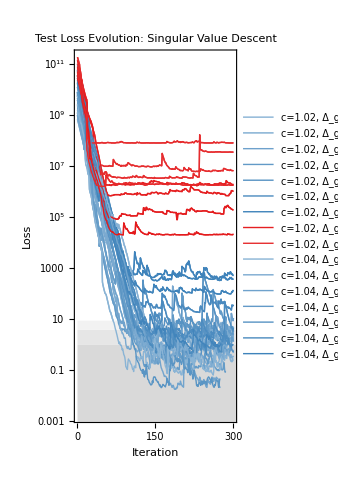

```mathematica
PlotLossVersusIterationOf["Test Loss Evolution: Singular Value Descent",ColorOf/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], RenameOf[MyCampaignResult[#],PrettyNameOf[#]]&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], PlotRange ->Automatic(*{{0,Automatic}, {10^-2, 10^17}}*)]
(*Export[MyCampaignPrefix<>"all_loss_vs_iter.pdf",%]*)

(* These are just for validation *)
(*PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: c=1.09 Candidate", {ColorForNaiveLoss,ColorForImprovedLoss},{MyCampaignGradResult[#],MyCampaignSVResult[#]},1.0]&[MyCampaignDefaultName]

PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: Singular Value Descent",ColorOf/@MyCampaignNames, RenameOf[MyCampaignSVResult[#],PrettyNameOf[#]]&/@MyCampaignNames,1]*)
```

### Computing Refined Losses

```mathematica
Monitor[{currentname = #;MyCampaignBestLossRefined[#]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
```

General::munfl: 4.96 2.17371080222×10^-1319 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.96 7.75696630338×10^-1871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1290.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Plotting

```mathematica
largeNumber = 10000;

DATA = Monitor[{CentralChargeOf[MyCampaignBestModel[#]],
Sort[DeltaOf/@PrimariesOf[MyCampaignBestModel[#]]][[2]],If[NumIterationsOf[MyCampaignResult[#]]>=MyNumEpochs || Log[10,MyCampaignBestLoss[#]] < lowYESthresh,currentname = #;Log[10,MyCampaignBestLossRefined[#]],largeNumber + NumIterationsOf[MyCampaignResult[#]]/MyNumEpochs]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
defaultsize = 1/16;
highYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(#[[3]]<=highYESthresh)&];
mediumYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(highYESthresh<#[[3]]<=mediumYESthresh)&];
lowYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(mediumYESthresh<#[[3]]<=lowYESthresh)&];
weakNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(lowYESthresh<#[[3]]<=weakNOthresh)&];
intermediateNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(weakNOthresh<#[[3]]<=intermediateNOthresh)&];
strongNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(intermediateNOthresh<#[[3]]<largeNumber)&];
UNKNOWN = {#[[1]],#[[2]],defaultsize/3}&/@Select[DATA,(largeNumber<= #[[3]])&];

N1MMexamples = {CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]], defaultsize}&/@{N1MM[5,MyMaxDelta],N1MM[6,MyMaxDelta],N1MM[7,MyMaxDelta],N1MM[8,MyMaxDelta]};

FBCBexamples = Join[{{1,0,defaultsize}},{CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]],defaultsize}&/@Table[FBCB[1/Sqrt[x],MyMaxDelta],{x,0.04,1,.04}]];

ADDexample = {(*Z5 parafermion*){8/7,4/35,defaultsize},(*Ising x tricritical Ising*){6/5,1/5,defaultsize},(*Z6 parafermion*){5/4,1/12,defaultsize}};
BOUNDS =  {{1, 0,1},{1.2,0.6,1}};

PLOT0 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[Lighter[ColorForPositiveValues,0],EdgeForm[GrayLevel[0]]],
Directive[Lighter[ColorForPositiveValues,0.4],EdgeForm[GrayLevel[0.4]]],Directive[Lighter[ColorForPositiveValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.4],EdgeForm[GrayLevel[0.4]]],
Directive[Lighter[ColorForNegativeValues,0.0],EdgeForm[GrayLevel[0.0]]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Integer Degeneracy, Δ_max=3"],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT4= Plot[{c/6+1/3,0}, {c,1,10}, PlotStyle -> Directive[Black,Dashed]];
PLOT5= ParametricPlot[{1,d}, {d,0,0.5}, PlotStyle -> Directive[Black,Dashed]];

Show[PLOT0,PLOT4,PLOT5]
Export[PathForPlots<>"survey_deltamax3.pdf",%]
```

General::munfl: 4.96 2.17371080222×10^-1319 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.96 7.75696630338×10^-1871 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1290.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

plots/survey_deltamax3.pdf

### Stats

(ⅇ^(-2^(-1+a) 5^a ν) (2^(-1+a) 5^a ν)^(ν/2) Log[10])/Gamma[ν/2]

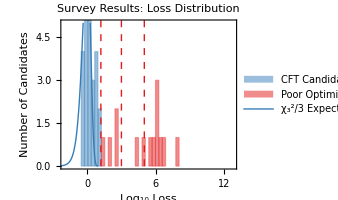

```mathematica
binwidth = (Log[9]+2 Log[10])/(n Log[10])/. n-> 10;
plot1 = Histogram[{
Select[DATA[[All,3]], (#<lowYESthresh)&],
Select[DATA[[All,3]], (lowYESthresh<=#<weakNOthresh)&],
Select[DATA[[All,3]], (weakNOthresh<=#<intermediateNOthresh)&],
Select[DATA[[All,3]], (intermediateNOthresh<=#)&]
}, 
{-2,13,binwidth}, 
ChartStyle-> {ColorForPositiveValues,ColorForNegativeValues,ColorForNegativeValues,ColorForNegativeValues}, Evaluate[DefaultPlotOptions], AspectRatio-> 0.8,PlotRange -> {0,5},
PlotLabel->NiceTitle["Survey Results: Loss Distribution"], FrameLabel-> {"Log_10 Loss","Number of Candidates"},ChartLegends-> Placed[{"  CFT Candidates","  Poor Optimization"},{Scaled[{0.72,0.74}], {1, 1}}]];
plot2 = ParametricPlot[{(*{0,t},{Log[10,4],t}*),{lowYESthresh,t},{weakNOthresh,t},{intermediateNOthresh,t}}, {t,0,17}, PlotStyle-> Directive[Dashed, ColorForNegativeValues,Thickness[Medium]]];
D[GammaRegularized[ν/2,0,2^(-1+a) 5^a ν], a]//Simplify
plot3 =  Plot[{((ⅇ^(-2^(-1+a) 5^a ν) (2^(-1+a) 5^a ν)^(ν/2) Log[10])/Gamma[ν/2]/. ν -> 3)*Length[Select[DATA[[All,3]], (#<0)&]]/0.6083748237289106*binwidth}, {a,-10,Log[10,9]}, PlotRange -> {0,5}, PlotStyle -> {Directive[ColorForPositiveValues,Thickness[Large]]}, Evaluate[DefaultPlotOptions],PlotLegends-> Placed[{"χ_3^2/3 Expectation"},{Scaled[{0.93,0.96}], {1, 1}}]];
Show[plot1,plot2,plot3]
```

## For Paper: Optimization Campaign (Survey With DeltaMax = 5)

## Setting Up Optimization Campaign

### Optimization Settings & Starting Models

```mathematica
MyMaxDelta = 5;

(* Defaults have Tau2Max of 6*)
MyCampaignDeterministicTaus[_] := DefaultCoarseDeterministicTausFor[MyMaxDelta];
MyCampaignRefinedDeterministicTaus[_] := DefaultFineDeterministicTausFor[MyMaxDelta];
MyCampaignTauSamplerData[_] := TauSamplerData[48,MyMaxDelta+2];

(* These values will certainly need to be adjusted *)
MyNumEpochs = 500;
MyLearningRate = 0.1;
MyMaxSVRatio = 10^-12;

MySpinValues = {0,1,2,3,4};
MyNumSpin[0] = 30;
MyNumSpin[1] = 24;
MyNumSpin[2] = 18;
MyNumSpin[3] = 12;
MyNumSpin[4] = 6;

Clear[MyPrimaries]
MyPrimaries[pseudogap_] := Flatten[
{{DSD[0, 0,1]},{DSD[pseudogap, 0,1]},
Table[Table[
DSD[SigmoidEsque[FlexDelta[s,i],Max[s,pseudogap],2*MyMaxDelta - Max[s,pseudogap]], 
s,
1],
 {i,1,MyNumSpin[s]}], {s,MySpinValues }]
}];
MyVariables = Flatten[Table[Table[FlexDelta[s,i], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];
MyInitialValues = Flatten[Table[Table[Log[(i/(MyNumSpin[s]+1))/(2-i/(MyNumSpin[s]+1))], {i,1,MyNumSpin[s]}], {s,MySpinValues }]];

MyCampaignPrefix = "survey_max5_sv24_";
MyCampaignSingularValue = 24;
MyRValue = Sqrt[2];
MyCampaignCentralCharges =Table[i,{i,1.02,1.20,0.04}] ;
MyCampaignDeltaGaps =  Table[i,{i,0.04,0.52,0.08}] ;

(* Things that have to be defined model specifically *)
MyCampaignNames = {};
For[cc = 1, cc <= Length[MyCampaignCentralCharges], cc++,
For[dg = 1, dg <= Length[MyCampaignDeltaGaps], dg++,
ThisCC = MyCampaignCentralCharges[[cc]];
ThisDG = MyCampaignDeltaGaps[[dg]];
MyLongName = MyCampaignPrefix <>"c"<>ToString[Round[ThisCC*100]]<>"_dg"<>ToString[Round[ThisDG*100]];
AppendTo[MyCampaignNames, MyLongName];
PrettyNameOf[MyLongName] = "c="<>ToString[SetAccuracy[ThisCC,3]]<>", Δ_gap="<>ToString[SetAccuracy[ThisDG,3]];
ColorOf[MyLongName] = If[ThisCC/6+1/3>ThisDG,Lighter[ColorForPositiveValues,1.5*(ThisCC/6+1/3-ThisDG)],Lighter[ColorForNegativeValues,-1.5*(ThisCC/6+1/3-ThisDG)]];
MyCampaignPrimaries[MyLongName] = MyPrimaries[ThisDG];
MyCampaignFlexibleModel[MyLongName] = CFTData[MyLongName,ThisCC,MyCampaignPrimaries[MyLongName], MyMaxDelta, MyVariables];
MyCampaignReferenceModel[MyLongName] = DefaultReferenceModelFor[MyCampaignFlexibleModel[MyLongName]];
MyCampaignStartingReplacement[MyLongName] = ReplacementData[MyVariables,MyInitialValues,{}];

MyCampaignAlgorithmDetails[MyLongName] = If[MyCampaignSingularValue==0,GradientDescentData[], SingularValueDescentData[MyCampaignSingularValue,MyMaxSVRatio]];
MyCampaignAlgorithm[MyLongName] =AlgorithmData[MyNumEpochs,MyLearningRate,MyCampaignAlgorithmDetails[MyLongName]];
]
]

highYESthresh = Log[10,4];
mediumYESthresh = Log[10,9];
lowYESthresh = Log[10,16];
weakNOthresh = Log[10,10^3];
intermediateNOthresh = Log[10,10^10];
LossColorOf[loss_]:= Which[
Log[10,loss] < highYESthresh, Lighter[ColorForPositiveValues,0],
Log[10,loss] < mediumYESthresh, Lighter[ColorForPositiveValues,0.4],
Log[10,loss] < lowYESthresh,Lighter[ColorForPositiveValues,0.8],
Log[10,loss] < weakNOthresh,Lighter[ColorForNegativeValues,0.8],
Log[10,loss] < intermediateNOthresh,Lighter[ColorForNegativeValues,0.4],
True,Lighter[ColorForNegativeValues,0]
]


(* Outputting names to make sure they look right*)
MyCampaignNames
ColorOf/@MyCampaignNames
MyCampaignDefaultName= MyCampaignNames[[1]]
```

{survey_max5_sv24_c102_dg4,survey_max5_sv24_c102_dg12,survey_max5_sv24_c102_dg20,survey_max5_sv24_c102_dg28,survey_max5_sv24_c102_dg36,survey_max5_sv24_c102_dg44,survey_max5_sv24_c102_dg52,survey_max5_sv24_c106_dg4,survey_max5_sv24_c106_dg12,survey_max5_sv24_c106_dg20,survey_max5_sv24_c106_dg28,survey_max5_sv24_c106_dg36,survey_max5_sv24_c106_dg44,survey_max5_sv24_c106_dg52,survey_max5_sv24_c110_dg4,survey_max5_sv24_c110_dg12,survey_max5_sv24_c110_dg20,survey_max5_sv24_c110_dg28,survey_max5_sv24_c110_dg36,survey_max5_sv24_c110_dg44,survey_max5_sv24_c110_dg52,survey_max5_sv24_c114_dg4,survey_max5_sv24_c114_dg12,survey_max5_sv24_c114_dg20,survey_max5_sv24_c114_dg28,survey_max5_sv24_c114_dg36,survey_max5_sv24_c114_dg44,survey_max5_sv24_c114_dg52,survey_max5_sv24_c118_dg4,survey_max5_sv24_c118_dg12,survey_max5_sv24_c118_dg20,survey_max5_sv24_c118_dg28,survey_max5_sv24_c118_dg36,survey_max5_sv24_c118_dg44,survey_max5_sv24_c118_dg52}

{RGBColor[0.7607843137254902, 0.8457058823529412, 0.915078431372549],RGBColor[0.6666666666666666, 0.785, 0.8816666666666666],RGBColor[0.5725490196078431, 0.7242941176470589, 0.8482549019607843],RGBColor[0.4784313725490195, 0.6635882352941176, 0.814843137254902],RGBColor[0.38431372549019605, 0.6028823529411764, 0.7814313725490196],RGBColor[0.2901960784313725, 0.5421764705882353, 0.7480196078431373],RGBColor[0.8967647058823529, 0.12441176470588242, 0.13205882352941184],RGBColor[0.7686274509803922, 0.850764705882353, 0.9178627450980392],RGBColor[0.6745098039215686, 0.7900588235294117, 0.8844509803921569],RGBColor[0.580392156862745, 0.7293529411764705, 0.8510392156862745],RGBColor[0.48627450980392156, 0.6686470588235294, 0.8176274509803921],RGBColor[0.3921568627450981, 0.6079411764705883, 0.7842156862745098],RGBColor[0.2980392156862745, 0.547235294117647, 0.7508039215686274],RGBColor[0.8957058823529411, 0.11543137254901963, 0.12315686274509804],RGBColor[0.7764705882352941, 0.8558235294117646, 0.9206470588235294],RGBColor[0.6823529411764706, 0.7951176470588235, 0.887235294117647],RGBColor[0.588235294117647, 0.7344117647058823, 0.8538235294117646],RGBColor[0.49411764705882344, 0.6737058823529412, 0.8204117647058823],RGBColor[0.39999999999999997, 0.613, 0.7869999999999999],RGBColor[0.3058823529411764, 0.5522941176470588, 0.7535882352941176],RGBColor[0.8946470588235294, 0.10645098039215696, 0.11425490196078442],RGBColor[0.7843137254901961, 0.8608823529411764, 0.9234313725490196],RGBColor[0.6901960784313725, 0.8001764705882353, 0.8900196078431373],RGBColor[0.596078431372549, 0.7394705882352941, 0.8566078431372549],RGBColor[0.5019607843137255, 0.6787647058823529, 0.8231960784313725],RGBColor[0.40784313725490196, 0.6180588235294118, 0.7897843137254902],RGBColor[0.3137254901960784, 0.5573529411764706, 0.7563725490196078],RGBColor[0.21960784313725487, 0.4966470588235294, 0.7229607843137255],RGBColor[0.7921568627450981, 0.8659411764705883, 0.9262156862745098],RGBColor[0.6980392156862745, 0.805235294117647, 0.8928039215686274],RGBColor[0.6039215686274509, 0.7445294117647059, 0.8593921568627451],RGBColor[0.5098039215686274, 0.6838235294117647, 0.8259803921568627],RGBColor[0.415686274509804, 0.6231176470588236, 0.7925686274509804],RGBColor[0.3215686274509804, 0.5624117647058824, 0.7591568627450981],RGBColor[0.2274509803921569, 0.5017058823529412, 0.7257450980392157]}

survey_max5_sv24_c102_dg4

### Plotting Starting Model

```mathematica
Validate[MyCampaignStartingModel[#]]&/@MyCampaignNames
(*MyCampaignStartingLoss/@ MyCampaignNames*)

MyCampaignStartingPlot[MyCampaignDefaultName]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

-Graphics-

### Checking For Existing Files

```mathematica
{Unset[MyCampaignResult[#]];#,FileExistsQ[MyCampaignFilename[#]], NumIterationsOf[MyCampaignResult[#]]}&/@MyCampaignNames
```

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[survey_max5_sv24_c102_dg4] not found.

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[survey_max5_sv24_c102_dg12] not found.

Unset::norep: Assignment on MyCampaignResult for MyCampaignResult[survey_max5_sv24_c102_dg20] not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{{survey_max5_sv24_c102_dg4,True,501},{survey_max5_sv24_c102_dg12,True,501},{survey_max5_sv24_c102_dg20,True,501},{survey_max5_sv24_c102_dg28,True,501},{survey_max5_sv24_c102_dg36,True,501},{survey_max5_sv24_c102_dg44,True,501},{survey_max5_sv24_c102_dg52,True,501},{survey_max5_sv24_c106_dg4,True,501},{survey_max5_sv24_c106_dg12,True,501},{survey_max5_sv24_c106_dg20,True,501},{survey_max5_sv24_c106_dg28,True,501},{survey_max5_sv24_c106_dg36,True,501},{survey_max5_sv24_c106_dg44,True,501},{survey_max5_sv24_c106_dg52,True,501},{survey_max5_sv24_c110_dg4,True,501},{survey_max5_sv24_c110_dg12,True,501},{survey_max5_sv24_c110_dg20,True,501},{survey_max5_sv24_c110_dg28,True,501},{survey_max5_sv24_c110_dg36,True,501},{survey_max5_sv24_c110_dg44,True,501},{survey_max5_sv24_c110_dg52,True,501},{survey_max5_sv24_c114_dg4,True,501},{survey_max5_sv24_c114_dg12,True,501},{survey_max5_sv24_c114_dg20,True,501},{survey_max5_sv24_c114_dg28,True,501},{survey_max5_sv24_c114_dg36,True,501},{survey_max5_sv24_c114_dg44,True,501},{survey_max5_sv24_c114_dg52,True,501},{survey_max5_sv24_c118_dg4,True,501},{survey_max5_sv24_c118_dg12,True,501},{survey_max5_sv24_c118_dg20,True,501},{survey_max5_sv24_c118_dg28,True,501},{survey_max5_sv24_c118_dg36,True,501},{survey_max5_sv24_c118_dg44,True,501},{survey_max5_sv24_c118_dg52,True,501}}

## Running Optimization (Will pick up from where it left off if file present)

### Running Optimization

```mathematica
MyRemainingNames = Select[MyCampaignNames,(Not[FileExistsQ[MyCampaignFilename[#]]]||NumIterationsOf[MyCampaignResult[#]]<MyNumEpochs)&];
(*The core optimization is here!*)
ParallelTable[
RunOptimizationFor[MyRemainingNames[[i]]];
,{i,1,Length[MyRemainingNames]}
]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

General::stop: Further output of A front end is not available; certain operations require a front end. will be suppressed during this calculation.

General::munfl: 1.40936×10^-199 (-7.08716×10^-140+5.23474×10^-140 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.40936×10^-199 (-7.08716×10^-140-5.23474×10^-140 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.29513×10^-301 (-1.6269×10^-122+2.29568×10^-122 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,6.11676×10^6,8.5794×10^6}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,1.64725×10^8,1.54214×10^8}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,3.34557,0.829273}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,4.439×10^13,currentTrainLoss$10034932}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,0.254872,0.124534}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,12.2717,5.55749}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,0.0261257,0.0271085}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,505.048,28.286}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,0.177983,0.0402247}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,2.06412,2.60029}

{AlgorithmData[500,0.1,SingularValueDescentData[24,1/1000000000000]],501,0.473488,0.159438}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Analysis of Results

### Loss Function Evolution

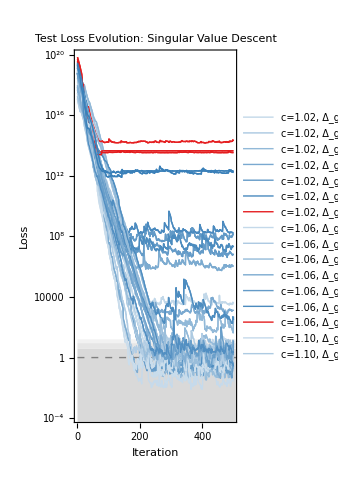

```mathematica
PlotLossVersusIterationOf["Test Loss Evolution: Singular Value Descent",ColorOf/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], RenameOf[MyCampaignResult[#],PrettyNameOf[#]]&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&], PlotRange ->Automatic(*{{0,Automatic}, {10^-2, 10^17}}*)]
(*Export[MyCampaignPrefix<>"all_loss_vs_iter.pdf",%]*)

(* These are just for validation *)
(*PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: c=1.09 Candidate", {ColorForNaiveLoss,ColorForImprovedLoss},{MyCampaignGradResult[#],MyCampaignSVResult[#]},1.0]&[MyCampaignDefaultName]

PlotBothLossesVersusIterationOf["Train/Test Loss Evolution: Singular Value Descent",ColorOf/@MyCampaignNames, RenameOf[MyCampaignSVResult[#],PrettyNameOf[#]]&/@MyCampaignNames,1]*)
```

### Computing Refined Losses

```mathematica
Monitor[{currentname = #;MyCampaignBestLossRefined[#]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
```

General::munfl: Exp[-21604.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1566.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3945.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Plotting

```mathematica
largeNumber = 10000;

DATA = Monitor[{CentralChargeOf[MyCampaignBestModel[#]],
Sort[DeltaOf/@PrimariesOf[MyCampaignBestModel[#]]][[2]],If[NumIterationsOf[MyCampaignResult[#]]>=MyNumEpochs || Log[10,MyCampaignBestLoss[#]] < lowYESthresh,currentname = #;Log[10,MyCampaignBestLossRefined[#]],largeNumber + NumIterationsOf[MyCampaignResult[#]]/MyNumEpochs]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
defaultsize = 1/16;
highYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(#[[3]]<=highYESthresh)&];
mediumYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(highYESthresh<#[[3]]<=mediumYESthresh)&];
lowYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(mediumYESthresh<#[[3]]<=lowYESthresh)&];
weakNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(lowYESthresh<#[[3]]<=weakNOthresh)&];
intermediateNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(weakNOthresh<#[[3]]<=intermediateNOthresh)&];
strongNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(intermediateNOthresh<#[[3]]<largeNumber)&];
UNKNOWN = {#[[1]],#[[2]],defaultsize/3}&/@Select[DATA,(largeNumber<= #[[3]])&];

N1MMexamples = {CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]], defaultsize}&/@{N1MM[5,MyMaxDelta],N1MM[6,MyMaxDelta],N1MM[7,MyMaxDelta],N1MM[8,MyMaxDelta]};

FBCBexamples = Join[{{1,0,defaultsize}},{CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]],defaultsize}&/@Table[FBCB[1/Sqrt[x],MyMaxDelta],{x,0.04,1,.04}]];

ADDexample = {(*Z5 parafermion*){8/7,4/35,defaultsize},(*Ising x tricritical Ising*){6/5,1/5,defaultsize},(*Z6 parafermion*){5/4,1/12,defaultsize}};
BOUNDS =  {{1, 0,1},{1.2,0.6,1}};

PLOT0 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[Lighter[ColorForPositiveValues,0],EdgeForm[GrayLevel[0]]],
Directive[Lighter[ColorForPositiveValues,0.4],EdgeForm[GrayLevel[0.4]]],Directive[Lighter[ColorForPositiveValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.4],EdgeForm[GrayLevel[0.4]]],
Directive[Lighter[ColorForNegativeValues,0.0],EdgeForm[GrayLevel[0.0]]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Integer Degeneracy, Δ_max=5"],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT4= Plot[{c/6+1/3,0}, {c,1,10}, PlotStyle -> Directive[Black,Dashed]];
PLOT5= ParametricPlot[{1,d}, {d,0,0.5}, PlotStyle -> Directive[Black,Dashed]];

Show[PLOT0,PLOT4,PLOT5]
Export[PathForPlots<>"survey_deltamax5.pdf",%]
```

General::munfl: Exp[-21604.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1566.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3945.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

survey_deltamax5.pdf

### Stats

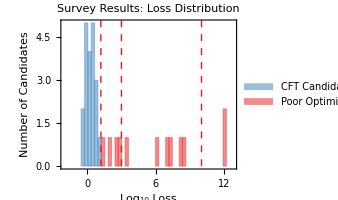

```mathematica
binwidth = (Log[9]+2 Log[10])/(n Log[10])/. n-> 10;
plot1 = Histogram[{
Select[DATA[[All,3]], (#<lowYESthresh)&],
Select[DATA[[All,3]], (lowYESthresh<=#<weakNOthresh)&],
Select[DATA[[All,3]], (weakNOthresh<=#<intermediateNOthresh)&],
Select[DATA[[All,3]], (intermediateNOthresh<=#)&]
}, 
{-2,13,binwidth}, 
ChartStyle-> {ColorForPositiveValues,ColorForNegativeValues,ColorForNegativeValues,ColorForNegativeValues}, Evaluate[DefaultPlotOptions], AspectRatio-> 0.8,PlotRange -> {0,5},
PlotLabel->NiceTitle["Survey Results: Loss Distribution"], FrameLabel-> {"Log_10 Loss","Number of Candidates"},ChartLegends-> Placed[{"  CFT Candidates","  Poor Optimization"},{Scaled[{0.72,0.74}], {1, 1}}]];
plot2 = ParametricPlot[{(*{0,t},{Log[10,4],t}*){lowYESthresh,t},{weakNOthresh,t},{intermediateNOthresh,t}}, {t,0,17}, PlotStyle-> Directive[Dashed, ColorForNegativeValues,Thickness[Medium]]];
Show[plot1,plot2]
```

### Plotting With Lower Cuts (Delta_max = 5 to 4)

```mathematica
highYESthresh = Log[10,4];
mediumYESthresh = Log[10,9];
lowYESthresh = Log[10,16];
weakNOthresh = Log[10,10^3];
intermediateNOthresh = Log[10,10^7];

largeNumber = 10000;
NewDeltaMax = 4;
DATA = Monitor[{CentralChargeOf[MyCampaignBestModel[#]],
Sort[DeltaOf/@PrimariesOf[MyCampaignBestModel[#]]][[2]],If[NumIterationsOf[MyCampaignResult[#]]>=MyNumEpochs || Log[10,MyCampaignBestLoss[#]] < lowYESthresh,currentname = #;Log[10,MyCampaignBestLossRefinedWithAltMax[#,NewDeltaMax]],largeNumber + NumIterationsOf[MyCampaignResult[#]]/MyNumEpochs]}&/@Select[MyCampaignNames, FileExistsQ[MyCampaignFilename[#]]&],
currentname];
defaultsize = 1/16;
highYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(#[[3]]<=highYESthresh)&];
mediumYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(highYESthresh<#[[3]]<=mediumYESthresh)&];
lowYES = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(mediumYESthresh<#[[3]]<=lowYESthresh)&];
weakNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(lowYESthresh<#[[3]]<=weakNOthresh)&];
intermediateNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(weakNOthresh<#[[3]]<=intermediateNOthresh)&];
strongNO = {#[[1]],#[[2]],defaultsize}&/@Select[DATA,(intermediateNOthresh<#[[3]]<largeNumber)&];
UNKNOWN = {#[[1]],#[[2]],defaultsize/3}&/@Select[DATA,(largeNumber<= #[[3]])&];

N1MMexamples = {CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]], defaultsize}&/@{N1MM[5,MyMaxDelta],N1MM[6,MyMaxDelta],N1MM[7,MyMaxDelta],N1MM[8,MyMaxDelta]};

FBCBexamples = Join[{{1,0,defaultsize}},{CentralChargeOf[#], Sort[DeltaOf/@PrimariesOf[#]][[2]],defaultsize}&/@Table[FBCB[1/Sqrt[x],MyMaxDelta],{x,0.04,1,.04}]];

ADDexample = {(*Z5 parafermion*){8/7,4/35,defaultsize},(*Ising x tricritical Ising*){6/5,1/5,defaultsize},(*Z6 parafermion*){5/4,1/12,defaultsize}};
BOUNDS =  {{1, 0,1},{1.2,0.6,1}};

PLOT0 = BubbleChart[{
highYES,
mediumYES,
lowYES,
weakNO,
intermediateNO,
strongNO,
UNKNOWN,
N1MMexamples,
ADDexample,
FBCBexamples
},ChartStyle->{
Directive[Lighter[ColorForPositiveValues,0],EdgeForm[GrayLevel[0]]],
Directive[Lighter[ColorForPositiveValues,0.4],EdgeForm[GrayLevel[0.4]]],Directive[Lighter[ColorForPositiveValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.8],EdgeForm[GrayLevel[0.8]]],
Directive[Lighter[ColorForNegativeValues,0.4],EdgeForm[GrayLevel[0.4]]],
Directive[Lighter[ColorForNegativeValues,0.0],EdgeForm[GrayLevel[0.0]]],
Directive[LightGray,EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]],
Directive[FaceForm[None],EdgeForm[None]]},BubbleSizes->{0.035,0.035},
Evaluate[DefaultPlotOptions],AspectRatio->(60/0.02)/(20/0.01),  FrameLabel->{{"Spectral Gap:  Δ_gap",None}, {"Central Charge:  c",None}},PlotLabel-> NiceTitle["Δ_max=5 Spectra Truncated to Δ_max="<>ToString[NewDeltaMax]],RotateLabel->True ,PlotRange-> {{1-.01, 1.20+.01},{0 - .01,0.6 + .01}}];
PLOT4= Plot[{c/6+1/3,0}, {c,1,10}, PlotStyle -> Directive[Black,Dashed]];
PLOT5= ParametricPlot[{1,d}, {d,0,0.5}, PlotStyle -> Directive[Black,Dashed]];

Show[PLOT0,PLOT4,PLOT5]
Export[PathForPlots<>"survey_deltamax5_trunc4.pdf",%]
```

General::munfl: Exp[-21604.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1566.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3945.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

survey_deltamax_5to4.pdf

## Scratch Work

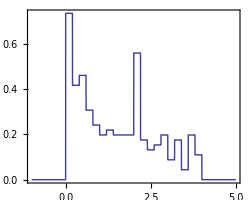

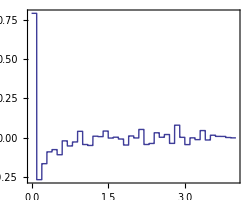

General::munfl: 6.96 3.4526799235×10^-421 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.96 5.14119859313×10^-421 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-76510.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
PointsWeightsOf[model_]:= {DeltaOf[#],DegeneracyOf[#]}&/@Select[PrimariesOf[model], (SpinOf[#]==0)&]
CrossedPointsWeightsOf[pw_]:= 
Flatten[Outer[{Abs[#1[[1]]-#2[[1]]],#1[[2]]*#2[[2]]}&,pw,pw,1],1];

MyModels = Table[FBCB[1/Sqrt[x],4],{x,0.03,1,.03}];
MyPointsWeights = Flatten[PointsWeightsOf/@MyModels,1];
MyCrossedPointsWeights = Flatten[CrossedPointsWeightsOf[PointsWeightsOf[#]]&/@MyModels,1];
MyBackgroundCrossedPointsWeights = CrossedPointsWeightsOf[MyPointsWeights];

PW = HistogramDistribution[WeightedData@@Transpose[MyPointsWeights],20];
Plot[PDF[PW,x], {x,-1,5}, Evaluate[DefaultPlotOptions], PlotRange-> {0, All}, Exclusions->None, AspectRatio-> 0.8]

XPW = HistogramDistribution[WeightedData@@Transpose[MyCrossedPointsWeights],{0,4,0.1}];
BXPW = HistogramDistribution[WeightedData@@Transpose[MyBackgroundCrossedPointsWeights],{0,4,0.1}];
Plot[{PDF[XPW,x]-PDF[BXPW,x]}, {x,0,4}, Evaluate[DefaultPlotOptions], PlotRange-> All,Exclusions->None, AspectRatio-> 0.8]
```

General::munfl: 6.96 3.4526799235×10^-421 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.96 5.14119859313×10^-421 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-76510.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

42

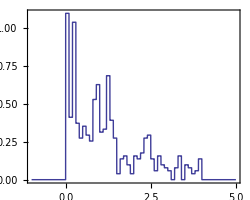

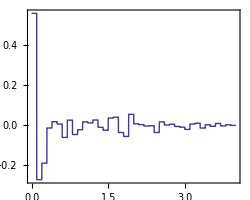

```mathematica
MyFoundModels = MyCampaignBestModel/@MyCampaignNames;
MyModels = HardTruncateOf/@Select[MyFoundModels, (CentralChargeOf[#]<1.15 && Sort[DeltaOf/@PrimariesOf[#]][[2]]<0.25)&];
Length[MyModels]
MyPointsWeights = Flatten[PointsWeightsOf/@MyModels,1];
MyCrossedPointsWeights = Flatten[CrossedPointsWeightsOf[PointsWeightsOf[#]]&/@MyModels,1];
MyBackgroundCrossedPointsWeights = CrossedPointsWeightsOf[MyPointsWeights];

PW = HistogramDistribution[WeightedData@@Transpose[MyPointsWeights],50];
Plot[PDF[PW,x], {x,-1,5}, Evaluate[DefaultPlotOptions], PlotRange-> {0, All}, Exclusions->None, AspectRatio-> 0.8]

XPW = HistogramDistribution[WeightedData@@Transpose[MyCrossedPointsWeights],{0,4,0.1}];
BXPW = HistogramDistribution[WeightedData@@Transpose[MyBackgroundCrossedPointsWeights],{0,4,0.1}];
Plot[{PDF[XPW,x]-PDF[BXPW,x]}, {x,0,4}, Evaluate[DefaultPlotOptions], PlotRange-> All,Exclusions->None, AspectRatio-> 0.8]
```